## Jecco Output Reader

Let’s define the initial number step, the final one, and the interval between each step that is going to be imported.
The Table FNames contained the names of the output files up to the location in your laptop.
You can choose “constrained”, “bulk”, “boundary” or “gauge” depending which kind of file you want to read.
Don’t forget the “_” after.

```mathematica
init=0;
end=25000;
each=10;
FNames=Table[StringJoin["bulk_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
Name1=Table[StringJoin["/home/giulio/University/PhD/Simulations/BB_TC_Lx10_Ly10_0d55ui24_1uo24_x50_y50_A0d1_2ov/",
FNames[[i]],".h5"],{i,FNames//Length}];
dt=Import[Name1[[-1]],"Attributes"][[3,1]];
Timing[Obj=Table[Import[Name1[[i]],"Data"](*[[1]]*),{i,1,Name1//Length}]];//AbsoluteTiming
FNames//Length
(*"/home/giulio/University/PhD/JeccoGt2/examples/BB_QNM_1D_4p1_Vchannel_xpert/"*)
times=Table[tim dt each+init dt,{tim,1,Obj//Length}];
(*snapshots=Table[(tim-1)  each+init ,{tim,1,Obj//Length}];*)
nt=times//Length;
Print["dt = "<>ToString[dt]]
Print["final time = "<>ToString[Import[Name1[[-1]],"Attributes"][[3,2]]//FullForm]]
```

{30.2423,Null}

2501

dt = 0.0005

final time = 12.500000000003785`

#### Grid

It’s usefull to have the XY grid explicitly in order to make more understandable plots.
Usually, I just import it from the initialdata notebook, but the X and Y grids are cartesian and equally spaced, so if you know the domain used it will be straightforward to create the grid calling a function like Range or Table (this information and also the number of points are contained in the parameter file that is usually in the output folder, together with the actual output data).
Note! In the grid, the last point is not considered!!!
This because of the periodic boundary conditions.

```mathematica
ay=Abs[Import[Name1[[1]],"Attributes"][[5,3,1]]];
by=-Abs[Import[Name1[[1]],"Attributes"][[5,3,1]]];
Ly=ay-by;
ax=Abs[Import[Name1[[1]],"Attributes"][[5,3,2]]];
bx=-Abs[Import[Name1[[1]],"Attributes"][[5,3,2]]];
Lx=ax-bx;
NPoints=Obj[[1,1,;;]]//Length
```

50

```mathematica
Import[Name1[[1]],"Attributes"][[5,3]]
```

{-5000.,-5000.,3.3}

```mathematica
xValues=Range[bx,ax,(ax 2)/(Obj[[1,1,1,;;]]//Length)][[1;;-2]];
yValues=Range[by,ay,(ay 2)/(Obj[[1,1,;;]]//Length)][[1;;-2]];
nx=xValues//Length;
ny=yValues//Length;
dx=xValues[[2]]-xValues[[1]];
dy=yValues[[2]]-yValues[[1]];
```

```mathematica
nx
ny
```

50

50

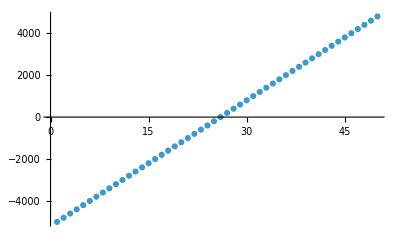

```mathematica
ListPlot[xValues]
```

```mathematica
prec=20
uOuterMin=7/10;(*The boundary of the inner subdomain*)
uOuterMax= 11/10;(*The boundary of the last outer subdomain, should be close to the horizon*)
uOuterDomains=1;(*Number of outer subdomain*)
uOuterNodes=12;(*Number of points in each outer subdomains*)
uInnerNodes=20;(*Number of points in the inner subdomains*)
InterfaceNodes=Table[uOuterMin+i(uOuterMax-uOuterMin)/uOuterDomains,{i,0,uOuterDomains,1}];(*This gives the nodes where the subdomains meet*)
```

20

```mathematica
GetuDomain2[uOutMin_,uOutmax_,uOutDomains_,uOutNodes_,uInnNodes_,IntfaceNodes_]:=Module[{uu=uOutMin},
XInn=Table[-Cos[Pi i/(uInnNodes-1)],{i,0,uInnNodes-1}];
uInner=N[Table[(IntfaceNodes[[1]]+0)/2+(IntfaceNodes[[1]]-0)/2 XInn[[i]],{i,1,uInnNodes}],prec];
XOut=Table[-Cos[Pi i/(uOutNodes-1)],{i,0,uOutNodes-1}];
uOut=N[Table[Table[1/2(IntfaceNodes[[j]]+IntfaceNodes[[j-1]])+1/2(IntfaceNodes[[j]]-IntfaceNodes[[j-1]])XOut[[i]],{i,1,uOutNodes}],{j,2,IntfaceNodes//Length}],prec];
(*Print[Flatten[uOut,{1}]//Dimensions];*)
Insert[Flatten[uOut,{1}],uInner,1]
]
```

```mathematica
uValues=GetuDomain2[uOuterMin,uOuterMax,uOuterDomains,uOuterNodes,uInnerNodes,InterfaceNodes];
```

```mathematica
{uValues1,uValues2(*,uValues3,uValues4*)}=uValues;
```

#### Derivatives

```mathematica
Clear[d];
d[1,0]=NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xValues,yValues},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,1]=NDSolve`FiniteDifferenceDerivative[Derivative[0,1],{xValues,yValues},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
(*d[2,0]=NDSolve`FiniteDifferenceDerivative[Derivative[2,0],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,1]=NDSolve`FiniteDifferenceDerivative[Derivative[0,1],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,2]=NDSolve`FiniteDifferenceDerivative[Derivative[0,2],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,6]=NDSolve`FiniteDifferenceDerivative[Derivative[0,6],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[6,0]=NDSolve`FiniteDifferenceDerivative[Derivative[6,0],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];*)
```

```mathematica
15
```

15

#### Inhomogeneous BBB Data Analysis

```mathematica
Obj[[1]]//Keys
```

{/data/0/fields/Sd c=2,/data/0/fields/S c=2,/data/0/fields/A c=2,/data/0/fields/Fx c=2,/data/0/fields/Fx c=1,/data/0/fields/Fy c=1,/data/0/fields/Sd c=1,/data/0/fields/Gd c=2,/data/0/fields/Gd c=1,/data/0/fields/Bd c=1,/data/0/fields/Bd c=2,/data/0/fields/Fy c=2,/data/0/fields/A c=1,/data/0/fields/S c=1}

Here I want to visualize the functions at a certain time and at a certain radius, hence in the XY plane.
I define the table SpecificFunction, where for each time (first entry, the “i” of the cycle), I just specify an object among the keys that we printed before (2nd entry), and I take a specific value of the radius. The GridSF is just the same but associates each value to the relative grid point, so that we will be able to print it.

```mathematica
(*ss=-10;*)
ClearAll[ss]
fy=Table[Obj[[ss,6,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
fx=Table[Obj[[ss,5,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
a3=Table[Obj[[ss,-2,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
(*dya3=d[0,1][a3];
dxa3=d[1,0][a3];
uy=(fy-dya3)/a3;
ux=(fx-dxa3)/a3;*)
u0=(-a3)^(1/2);
ux=Table[(fx[[tt]]-d[1,0][a3[[tt]]])/a3[[tt]],{tt,1,a3//Length}](*-fx u0*);
uy=Table[(fy[[tt]]-d[0,1][a3[[tt]]])/a3[[tt]],{tt,1,a3//Length}](*-fy u0*);
a=1;
b=ux[[1]]//Length;
c=1;
dd=uy[[1,1]]//Length;
x0=0;
y0=0;
ellipse[θ_,sigmax_,sigmay_]:={x0+sigmax Cos[θ],y0+sigmay Sin[θ]};
```

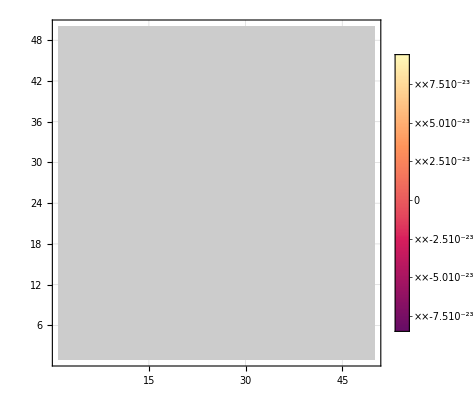

```mathematica
ListContourPlot[fy[[1]]//Transpose,PlotRange->All,PlotLegends->Automatic,GridLines->Automatic
]
```

-18480.

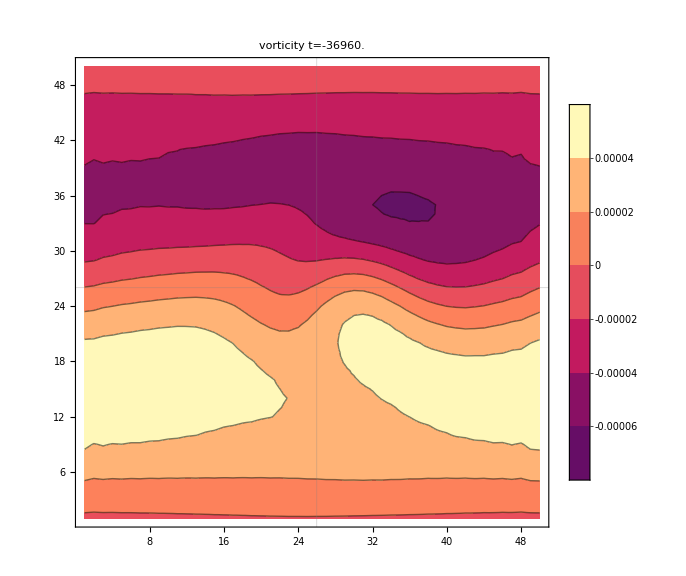

```mathematica
ss=-1;
ss dt each+init dt
Show[ListContourPlot[(d[1,0][uy[[ss]]]-d[0,1][ux[[ss]]])//Transpose,PlotRange->{All,All,All}, PlotLegends->True,
PlotLabel->"vorticity t="<>ToString[(ss-1) dt each+init dt],ImageSize->Large,AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]]),GridLines->{{26},{26}}](*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)]
```

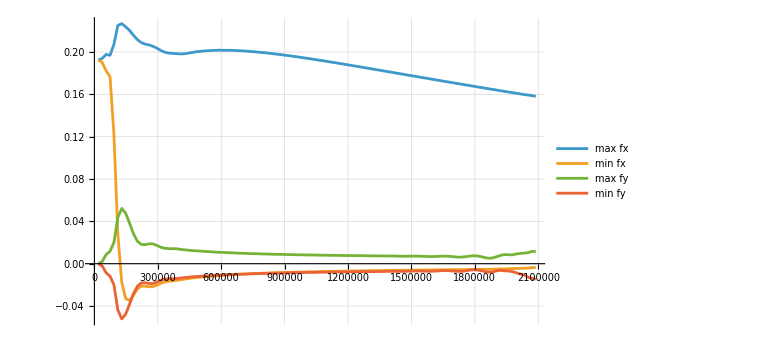

```mathematica
ListPlot[{{times,Map[Max,ux,2]}//Transpose,{times,Map[Min,ux,2]}//Transpose,{times,Map[Max,uy,2]}//Transpose,{times,Map[Min,uy,2]}//Transpose},ImageSize->Large(*,PlotRange->All*),PlotLegends->{"max fx","min fx","max fy","min fy"},Joined->True,GridLines->{Automatic, Table[i,{i,-1,1,0.01}]},PlotRange->All]
```

```mathematica
ux//Length
```

23

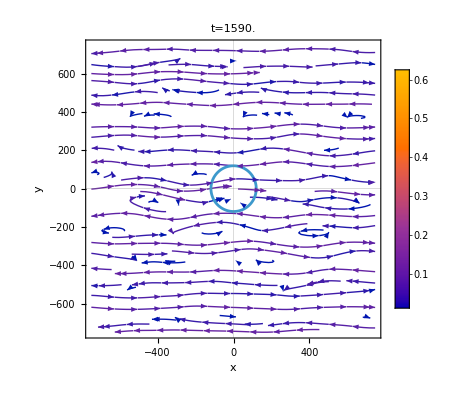

```mathematica
t=(*(ux//Length)*)23;
a=1;
b=ux[[1]]//Length;
c=1;
dd=uy[[1,1]]//Length;
Show[Table[{{xValues[[i]],yValues[[j]]},{ux[[t,i,j]],uy[[t,i,j]]}},{i,a,b
},{j,c,dd}]//
ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)PlotLegends->Automatic,ImageSize->Full,GridLines->{{0}, {0}},PlotLabel->"t="<>ToString[t dt each+init dt](*,10->10[0.01]*),StreamStyle->{Arrowheads[0.007],Thick[0.05]},AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]])(*,StreamPoints->50000*),LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16},FrameLabel->{"x","y"}]&(*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)]
```

```mathematica
xValues[[20]]
```

-1200.

```mathematica
ux[[1,1]]//Length
```

50

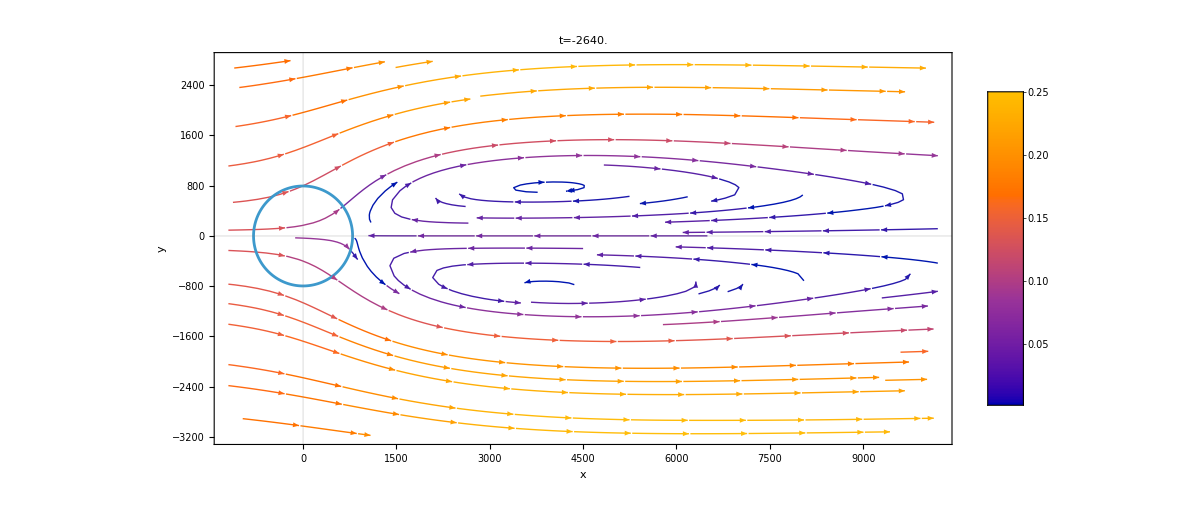

```mathematica
t=-1;
a=1(ux[[1]]//Length)/2-5//Floor;
b=(ux[[1]]//Length)/2+52//Floor;
c=(ux[[1,1]]//Length)/2-15//Floor;
dd=(ux[[1,1]]//Length)/2+15//Floor;
Show[Table[{{xValues[[i]],yValues[[j]]},{ux[[t,i,j]],uy[[t,i,j]]}},{i,a,b
},{j,c,dd}]//
ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)StreamPoints->100000,PlotLegends->Automatic,ImageSize->{1000,1000},GridLines->{{0}, {0}},PlotLabel->"t="<>ToString[t dt each+init dt](*,10->10[0.01]*),StreamStyle->{Arrowheads[0.008],Thick[0.05]},AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]])(*,StreamPoints->50000*),LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16},FrameLabel->{"x","y"}]&,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]]
```

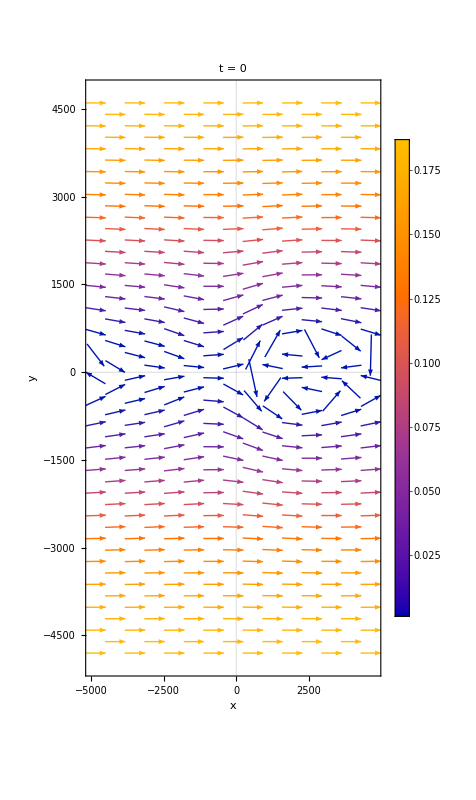

```mathematica
t=-1;
(*xLineInd=150;*)
Table[{{xValues[[i]],yValues[[j]]},{ux[[t,i,j]],1uy[[t,i,j]]}},{i,1,xValues//Length
},{j,1,yValues//Length}]//ListVectorPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)PlotLegends->Automatic,ImageSize->Full,GridLines->{{0}, {0}},PlotLabel->"t = 0"(*<>ToString[t dt each+init dt]*),VectorStyle->Arrowheads[0.008],VectorPoints->Fine ,AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]]),ImageSize->Large,LabelStyle->Directive[FontSize->20],BaseStyle->{FontSize->16},FrameLabel->{"x","y"},ColorFunction->"ColorBlindTones"]&
```

```mathematica
ux//Length
```

242

```mathematica
frames=Table[Show[Table[{{xValues[[i]],yValues[[j]]},{ux[[tt,i,j]],1uy[[tt,i,j]]}},{i,a,b
},{j,c,dd}]//ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)PlotLegends->Automatic,ImageSize->{1000,500},GridLines->{{0}, {0}},PlotLabel->"t="<>ToString[tt dt each+init dt],VectorStyle->Arrowheads[0.007](*,VectorPoints->60*) ,AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]]),ImageSize->Large]&,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]],{tt,1,ux//Length}];//AbsoluteTiming
```

{50.5997,Null}

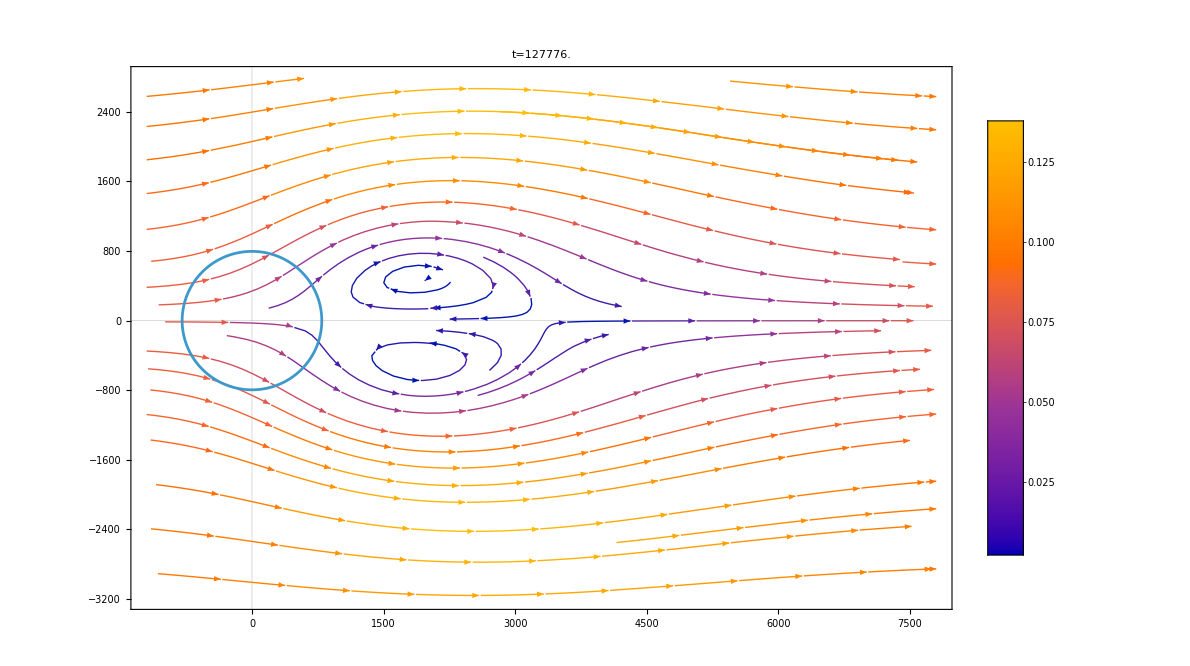

```mathematica
frames[[-1]]
```

```mathematica
NBB_gaussian_Lx1500_Ly500_0d55iu10_1u010_Nx150_Ny50_u0d01_tzero5000_tau2000_A0d8_s62d5
```

```mathematica
Export["/home/giulio/Videos/velocity_stream_field_Nx100_Ny100_L1500_u0d1_s0d25_t05000_tau2000_A0d925.mp4",frames,"DisplayDurations"->0.8];//AbsoluteTiming
```

{37.9488,Null}

```mathematica
x+Log[y]
```

x+Log[y]

#### Boundary Stress Tensor

gauge

```mathematica
init=0;
end=1627000;
each=10000;
FNames=Table[StringJoin["gauge_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
Name1=Table[StringJoin["/home/giulio/University/PhD/Simulations/NBB_gaussian_L500_0d55iu10_1u010_N100_u0d01_tzero5000_tau2000_A0d675_s0d125/",
FNames[[i]],".h5"],{i,FNames//Length}];
dt=Import[Name1[[2]],"Attributes"][[3,1]];
Timing[xi=Table[Import[Name1[[i]],"Data"][[1,;;,;;,1]],{i,1,Name1//Length}]];//AbsoluteTiming
FNames//Length
snapshots=Table[(tim-1)  each+init ,{tim,1,Obj//Length}];
(*"/home/giulio/University/PhD/JeccoGt2/examples/BB_QNM_1D_4p1_Vchannel_xpert/"*)
times=Table[tim dt each+init dt,{tim,1,Obj//Length}];
nt=times//Length;
Print["dt = "<>ToString[dt]]
Print["final time = "<>ToString[Import[Name1[[-1]],"Attributes"][[3,2]]//FullForm]]
```

Import::nffil: File /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx1500_Ly1500_0d55iu10_1u010_Nx50_Ny50_u0d05_tzero5000_tau2000_A0d8_s0d125_noise_boundary/gauge_00010000.h5 not found during Import.

Part::partd: Part specification $Failed⟦3,1⟧ is longer than depth of object.

Import::nffil: File /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx1500_Ly1500_0d55iu10_1u010_Nx50_Ny50_u0d05_tzero5000_tau2000_A0d8_s0d125_noise_boundary/gauge_00000000.h5 not found during Import.

Part::partd: Part specification $Failed⟦1,1;;All,1;;All,1⟧ is longer than depth of object.

Import::nffil: File /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx1500_Ly1500_0d55iu10_1u010_Nx50_Ny50_u0d05_tzero5000_tau2000_A0d8_s0d125_noise_boundary/gauge_00010000.h5 not found during Import.

Part::partd: Part specification $Failed⟦1,1;;All,1;;All,1⟧ is longer than depth of object.

Import::nffil: File /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx1500_Ly1500_0d55iu10_1u010_Nx50_Ny50_u0d05_tzero5000_tau2000_A0d8_s0d125_noise_boundary/gauge_00020000.h5 not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1,1;;All,1;;All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{0.148125,Null}

163

dt = $Failed[[3,1]]

Import::nffil: File /home/giulio/University/PhD/Simulations/NBB_gaussian_Lx1500_Ly1500_0d55iu10_1u010_Nx50_Ny50_u0d05_tzero5000_tau2000_A0d8_s0d125_noise_boundary/gauge_01620000.h5 not found during Import.

Part::partd: Part specification $Failed⟦3,2⟧ is longer than depth of object.

final time = Part[$Failed, 3, 2]

B at boundary

```mathematica
file="NBB_gaussian_Lx1500_Ly1500_0d55iu10_1u010_Nx50_Ny50_u0d05_tzero5000_tau2000_A0d8_s0d125_noise_boundary";
init=990000;
end=1000000;
each=1000;
(*FNamesBulk=Table[StringJoin["bulk_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
NamesBulk=Table[StringJoin["/home/giulio/University/PhD/Simulations/"<>file<>"/",
FNamesBulk[[i]],".h5"],{i,FNamesBulk//Length}];
FNamesConstrained=Table[StringJoin["constrained_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
NamesConstrained=Table[StringJoin["/home/giulio/University/PhD/Simulations/"<>file<>"/",
FNamesConstrained[[i]],".h5"],{i,FNamesConstrained//Length}];*)
FNamesBoundary=Table[StringJoin["boundary_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
NamesBoundary=Table[StringJoin["/home/giulio/University/PhD/Simulations/"<>file<>"/",
FNamesBoundary[[i]],".h5"],{i,FNamesBoundary//Length}];
dt=Import[NamesBoundary[[2]],"Attributes"][[3,1]];
times=Table[tim dt each+init dt,{tim,0,(FNamesBoundary//Length)-1}];
nt=times//Length;
Print["dt = "<>ToString[dt]]
Print["final time = "<>ToString[Import[NamesBoundary[[-1]],"Attributes"][[3,2]]//FullForm]]
snapshots=Table[(tim-1)  each+init ,{tim,1,times//Length}];
b3=Table[Import[NamesBoundary[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/b13"][[;;,;;,1]]//Transpose,{i,1,NamesBoundary//Length}];
g3=Table[Import[NamesBoundary[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/g3"][[;;,;;,1]]//Transpose,{i,1,NamesBoundary//Length}];
fx=Table[Import[NamesBoundary[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/fx1"][[;;,;;,1]]//Transpose,{i,1,NamesBoundary//Length}];
fy=Table[Import[NamesBoundary[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/fy1"][[;;,;;,1]]//Transpose,{i,1,NamesBoundary//Length}];
a3=Table[Import[NamesBoundary[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/a3"][[;;,;;,1]]//Transpose,{i,1,NamesBoundary//Length}];
(*Fxh=Table[Import[NamesConstrained[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/Fx c=2"][[;;,;;,-1]],{i,1,NamesBulk//Length}];
Fyh=Table[Import[NamesConstrained[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/Fy c=2"][[;;,;;,-1]],{i,1,NamesBulk//Length}];*)
```

dt = 0.0244444

final time = 24444.44444429339`

```mathematica
times[[1]]
```

0.

```mathematica
b3//Dimensions
```

{101,50,50}

```mathematica
times//Length
```

123

```mathematica
Import[NamesBoundary[[-1]],"Attributes"][[3,2]]
```

39600.

```mathematica
Obj[[1]]//Keys
```

{/data/0/fields/fy1,/data/0/fields/fx1,/data/0/fields/b13,/data/0/fields/a3,/data/0/fields/g3}

```mathematica
Tdd=Table[{{a3[[tt]],fx[[tt]],fy[[tt]]},{fx[[tt]],E^(-b3[[tt]])Cosh[g3[[tt]]],Sinh[g3[[tt]]]},{fy[[tt]],Sinh[g3[[tt]]],E^b3[[tt]] Cosh[g3[[tt]]]}},{tt,1,times//Length}];
```

source

```mathematica
S0tilt[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_,phi_]:=1-1/2 (1+Tanh[(t-t0)/tau])*A*Exp[-1/2*((((x-x0) Cos[phi]+(y-y0) Sin[phi])^2)/(L sigmax)^2+((-(x-x0) Sin[phi]+(y-y0) Cos[phi])^2)/(L sigmay)^2)]//FullSimplify;
```

```mathematica
tzero=5000;
τ=2000;
Subscript[σ, x]=1/8 1500;
Subscript[σ, x]=1/8 1500;
Subscript[σ, y]=1/8 1500;
ϕ=0;
L=1500;
Amp=0.8;
```

```mathematica
σ=Table[S0tilt[times[[tt]],tzero,τ,Amp,xValues[[xx]],0,Subscript[σ, x],yValues[[yy]],0,Subscript[σ, y],ϕ],{tt,1,times//Length},{xx,1,xValues//Length},{yy,1,yValues//Length}];
```

```mathematica
gbdyuu=Table[DiagonalMatrix[{-1,σ[[tt,xx,yy]],σ[[tt,xx,yy]]}],{tt,1,times//Length},{xx,1,xValues//Length},{yy,1,yValues//Length}];
```

```mathematica
gbdydd=Table[Inverse[gbdyuu[[tt,xx,yy]]],{tt,1,times//Length},{xx,1,xValues//Length},{yy,1,yValues//Length}];
```

```mathematica
Tdd//Dimensions
Inverse[gbdyuu[[1,1,1]]]//Dimensions
gbdydd//Dimensions
```

{163,3,3,50,50}

{3,3}

{163,50,50,3,3}

```mathematica
Tud=Table[gbdydd[[tt,xx,yy]].Tdd[[tt,;;,;;,xx,yy]],{tt,1,times//Length},{xx,1,xValues//Length},{yy,1,yValues//Length}];
```

```mathematica
Tud[[1,1,1]]//MatrixForm
```

(1.00375 | 0.0484234 | 0.000183251
-0.0487562 | 1.00813 | 0.
-0.00018451 | 0. | 1.00561)

```mathematica
({{1.0085441512899103, 0.00997226868745104, 3.049476349842428*^-7}, {-0.03053769237288054, 3.062412445855567, 6.13882116020775*^-9}, {-9.338293380226364*^-7, 6.13882116020775*^-9, 3.0621101411680796}})
```

{{1.00854,0.00997227,3.04948×10^-7},{-0.0305377,3.06241,6.13882×10^-9},{-9.33829×10^-7,6.13882×10^-9,3.06211}}

```mathematica
Tdd//Dimensions
Tud//Dimensions
```

{163,3,3,50,50}

{163,50,50,3,3}

```mathematica
AllVecs=Table[Eigenvectors[Tud[[tt,xx,yy,;;,;;]]],{tt,1,times//Length},{xx,1,xValues//Length},{yy,1,yValues//Length}];
```

```mathematica
AllVecs[[1,;;,;;]]//Dimensions
```

{50,50,3,3}

```mathematica
AllVecs[[10,;;,;;,3,3]]
```

```mathematica
ϵ//Dimensions
```

{163,50,50,3}

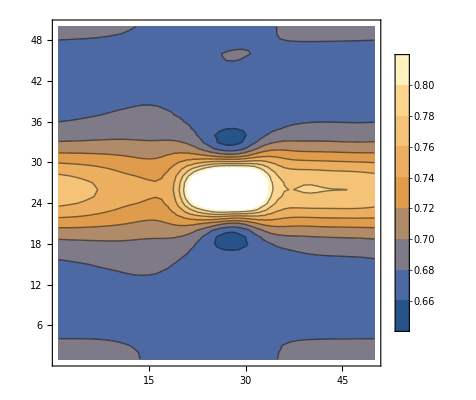

```mathematica
ListContourPlot[ϵ[[-20,;;,;;,3]],PlotLegends->Automatic]
```

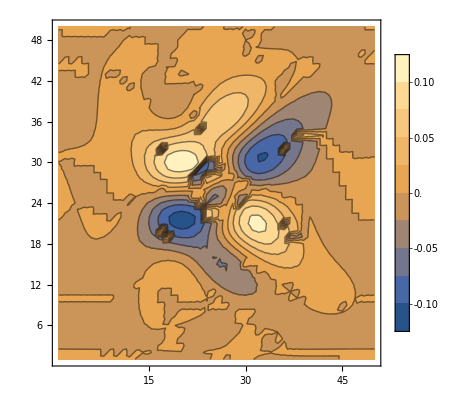

```mathematica
ListContourPlot[AllVecs[[-1,;;,;;,3,3]],PlotLegends->Automatic,PlotRange->All]
```

```mathematica
vecs=Table[Select[Eigenvectors[Tud[[tt,xx,yy,;;,;;]]](*//Re*),FreeQ[#,Complex](*Module[{u=#,norm},norm=u.gbdydd[[tt,xx,yy]].u;
Re[norm]<0  (*Pick only timelike ones*)]*)&],{tt,1,times//Length},{xx,1,xValues//Length},{yy,1,yValues//Length}];
```

```mathematica
Eigen=Table[Select[Eigensystem[Tud[[tt,xx,yy,;;,;;]]](*//Re*),FreeQ[#[[2]],Complex](*Module[{u=#,norm},norm=u.gbdydd[[tt,xx,yy]].u;
Re[norm]<0  (*Pick only timelike ones*)]*)&],{tt,1,times//Length},{xx,1,xValues//Length},{yy,1,yValues//Length}]
```

```mathematica
vecs//Dimensions
```

{163,50,50}

```mathematica
u0=vecs[[14;;150,;;,;;,1,1]];
uxx=vecs[[14;;150,;;,;;,1,2]];
uyy=vecs[[14;;150,;;,;;,1,3]];
```

```mathematica
ϵ=Table[Eigenvalues[Tud[[tt,xx,yy,;;,;;]]],{tt,1,times//Length},{xx,1,xValues//Length},{yy,1,yValues//Length}];
```

```mathematica
ListContourPlot[ϵ[[1,;;,;;]],PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

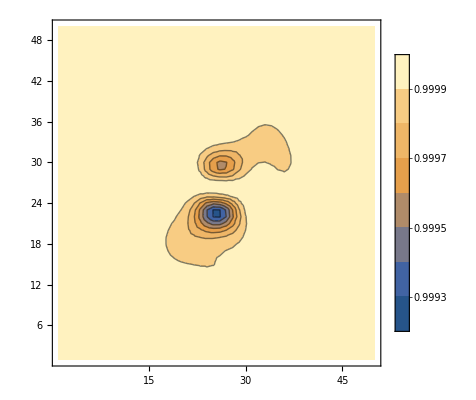

```mathematica
ListContourPlot[uyy[[1,;;,;;]],PlotLegends->Automatic,PlotRange->All]
```

```mathematica
each
```

2000

```mathematica
uxx//Dimensions
```

{244,50,50}

```mathematica
ListContourPlot
```

246.009

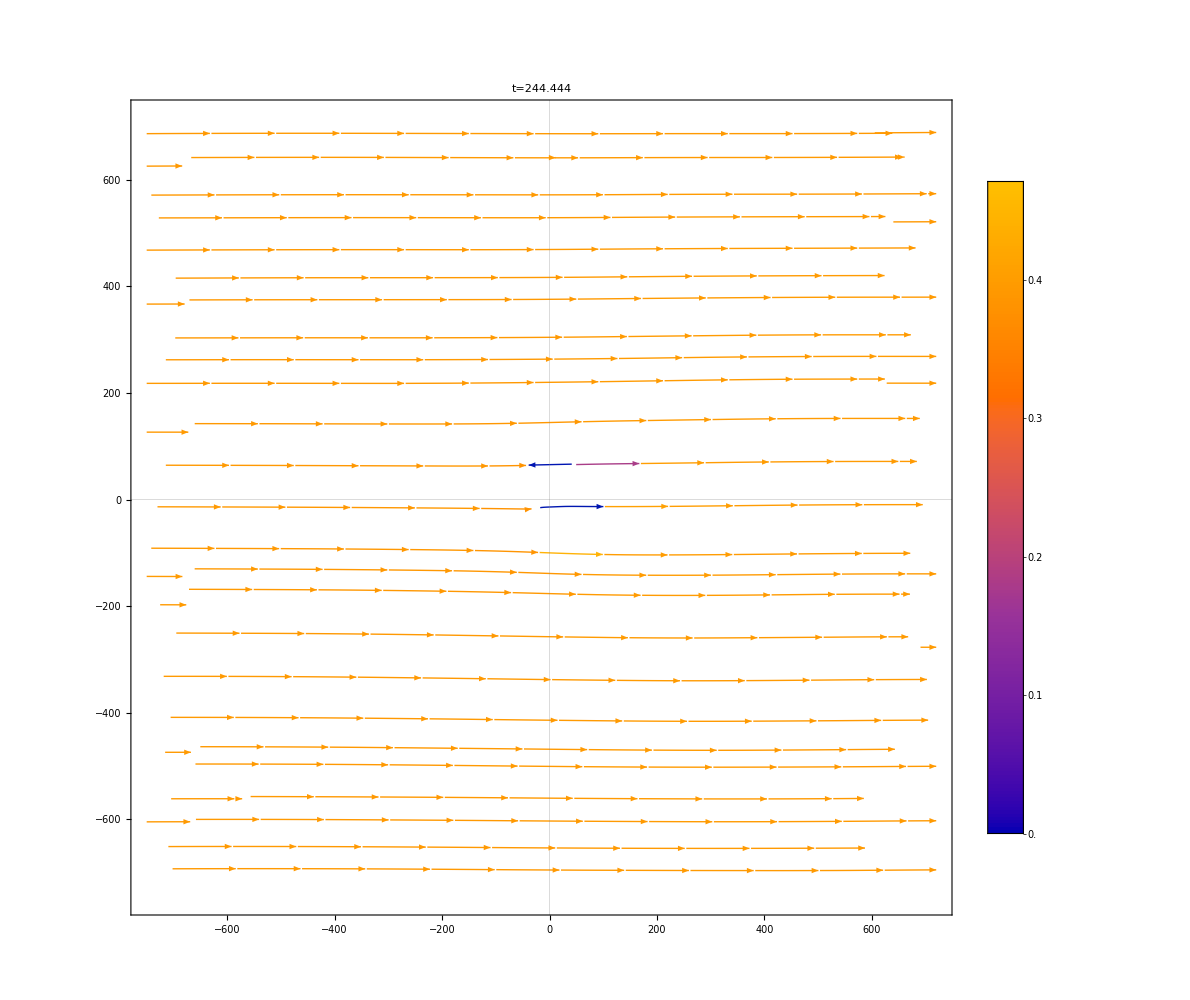

```mathematica
t=1;
t dt each+(init +64)dt
(*xLineInd=150;*)
Table[{{xValues[[i]],yValues[[j]]},{uxx[[t,j,i]],1uyy[[t,j,i]]}},{i,1,xValues//Length
},{j,1,yValues//Length}]//ListStreamPlot[#,StreamPoints->100000,(*PlotRange->{{-200,200},{-200,200}},*)PlotLegends->Automatic,ImageSize->{1000,500},GridLines->{{0}, {0}},PlotLabel->"t="<>ToString[t dt each+init dt],VectorStyle->Arrowheads[0.01](*,VectorPoints->80*) ,StreamStyle->Arrowheads[0.01],AspectRatio->1/1,ImageSize->Large]&
```

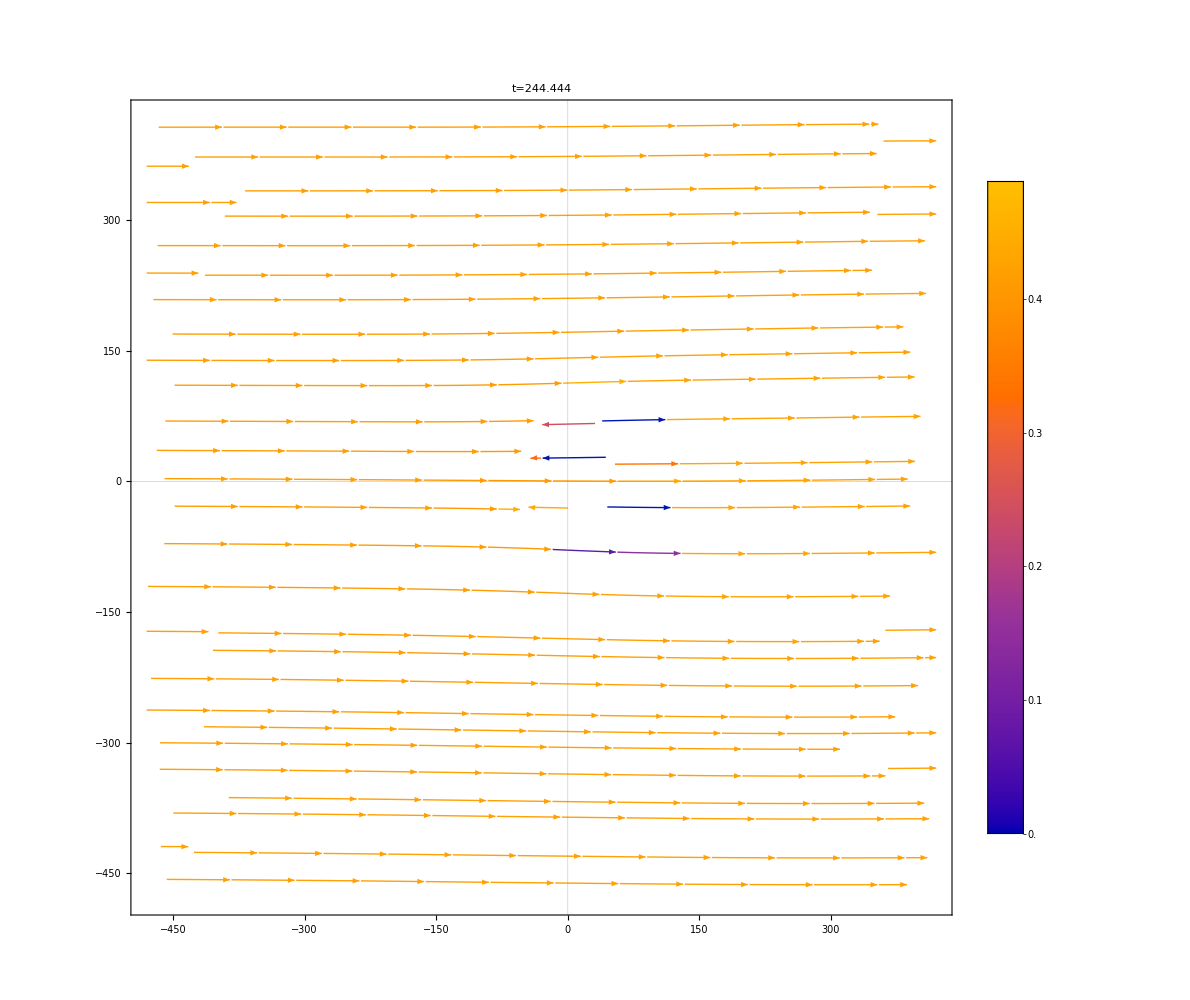

```mathematica
t=1;
a=10;
b=40;
c=10;
dd=40;
Table[{{xValues[[i]],yValues[[j]]},{uxx[[t,j,i]],uyy[[t,j,i]]}},{i,a,b
},{j,c,dd}]//
ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)PlotLegends->Automatic,ImageSize->{1000,500},GridLines->{{0}, {0}},PlotLabel->"t="<>ToString[t dt each+init dt],VectorStyle->Arrowheads[0.01],StreamStyle->Arrowheads[0.01],AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]])(*,StreamPoints->50000*),ImageSize->Large]&
```

#### Drag Forces

```mathematica
L
```

1500.

```mathematica
{157,45,55}
```

{157,45,55}

```mathematica
uy//Dimensions
```

{149,45,55}

```mathematica
DragForceFromTtiRing[ux_,uy_,xGrid_,yGrid_,x0_,y0_,sigmax_,sigmay_,epsilonInner_:0.6^2,epsilonOuter_:1.4^2]:=Module[{nt=Length[ux],nx=Length[xGrid],ny=Length[yGrid],dragForceList,dx,dy,ds,ringMask,normal,forceAtTime},(*Grid spacing*)
dx=xGrid[[2]]-xGrid[[1]];
dy=yGrid[[2]]-yGrid[[1]];
ds=Sqrt[dx^2+dy^2];(*Approximate arc element*)
(*Compute the mask over the grid*)ringMask=Table[If[epsilonInner<((x-x0)^2/sigmax^2+(y-y0)^2/sigmay^2)<epsilonOuter,1,0],{x,xGrid},{y,yGrid}];
normal[x_,y_]:=Module[{nnx,nny,norm},nnx=2 (x-x0)/sigmax^2;
nny=2 (y-y0)/sigmay^2;
norm=Sqrt[nnx^2+nny^2];
If[norm==0,{0,0},{nnx,nny}/norm]];
(*Compute force at each time step*)
dragForceList=Table[Module[{Fx=0.0,Fy=0.0,nvec,Tti},Do[If[ringMask[[i,j]]==1,nvec=normal[xGrid[[i]],yGrid[[j]]];
Tti={ux[[t,i,j]],uy[[t,i,j]]};
{Fx,Fy}+=-Tti*(nvec.{dx,dy});],{i,nx},{j,ny}];
{Fx,Fy}],{t,nt}];
{dragForceList,ringMask}];
```

```mathematica
{forces,rm}=DragForceFromTtiRing[ux,uy,xValues,yValues,0,0,(0.125L)/(2Pi),(0.125 L)/(2Pi)];
```

```mathematica
xValues
```

{-2250.,-2160.,-2070.,-1980.,-1890.,-1800.,-1710.,-1620.,-1530.,-1440.,-1350.,-1260.,-1170.,-1080.,-990.,-900.,-810.,-720.,-630.,-540.,-450.,-360.,-270.,-180.,-90.,0.,90.,180.,270.,360.,450.,540.,630.,720.,810.,900.,990.,1080.,1170.,1260.,1350.,1440.,1530.,1620.,1710.,1800.,1890.,1980.,2070.,2160.}

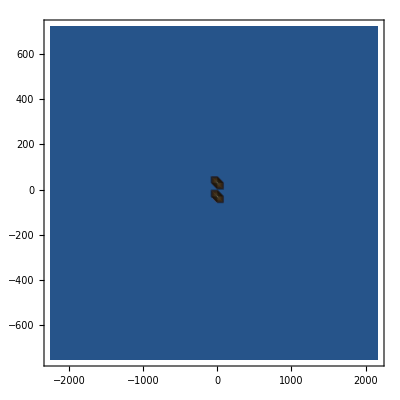

```mathematica
ListContourPlot[Flatten[Table[{xValues[[i]],yValues[[j]],rm[[i,j]]},{i,nx},{j,ny}],1](*,PlotRange->{{-40,40},{-40,40}}*)]
```

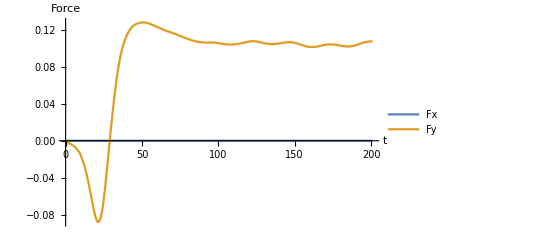

```mathematica
ListLinePlot[{forces[[All,1]],forces[[All,2]]},PlotLegends->{"Fx","Fy"},AxesLabel->{"t","Force"},PlotRange->All,ImageSize->Full]
```

Now let’s try with continous functions

```mathematica
uxInterp=Table[ListInterpolation[ux[[t]],{xValues,yValues}],{t,nt}];
uyInterp=Table[ListInterpolation[uy[[t]],{xValues,yValues}],{t,nt}];
```

```mathematica
x0=0;
y0=0;
```

```mathematica
ellipse[θ_,sigmax_,sigmay_]:={x0+sigmax Cos[θ],y0+sigmay Sin[θ]};

(*Tangent and normal*)
tangent[θ_,sigmax_,sigmay_]:={-sigmax Sin[θ],sigmay Cos[θ]};

normal[θ_,sigmax_,sigmay_]:=Normalize@{Cos[θ]/sigmax,Sin[θ]/sigmay};

(*Arc element*)
ds[θ_,sigmax_,sigmay_]:=Norm[tangent[θ]] dθ;
```

```mathematica
L=-2yValues[[1]]
```

1500.

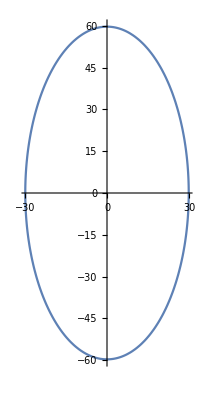

```mathematica
ParametricPlot[ellipse[θ,(0.125 L)/(2Pi),(0.25 L)/(2Pi)],{θ,0,2Pi}]
```

```mathematica
computeDragForce[t_,σx_,σy_]:=Module[{uxf,uyf,Fx,Fy,sigmax=σx,sigmay=σy},
uxf=uxInterp[[t]];
uyf=uyInterp[[t]];
Fx=-NIntegrate[Module[{x,y,n},{x,y}=ellipse[θ,sigmax,sigmay];
n=normal[θ,sigmax,sigmay];
uxf[x,y]*n[[1]]*Norm[tangent[θ,sigmax,sigmay]]],{θ,0,2 Pi}];
Fy=-NIntegrate[Module[{x,y,n},{x,y}=ellipse[θ,sigmax,sigmay];
n=normal[θ,sigmax,sigmay];
uyf[x,y]*n[[2]]*Norm[tangent[θ,sigmax,sigmay]]],{θ,0,2 Pi}];
{Fx,Fy}];
```

```mathematica
dragForceList=Table[computeDragForce[t,(0.07Lx)/(2Pi),(0.25 Ly)/(2Pi)],{t,1,nt}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.16604}. NIntegrate obtained -1.69503×10^-13 and 2.39797×10^-15 for the integral and error estimates.

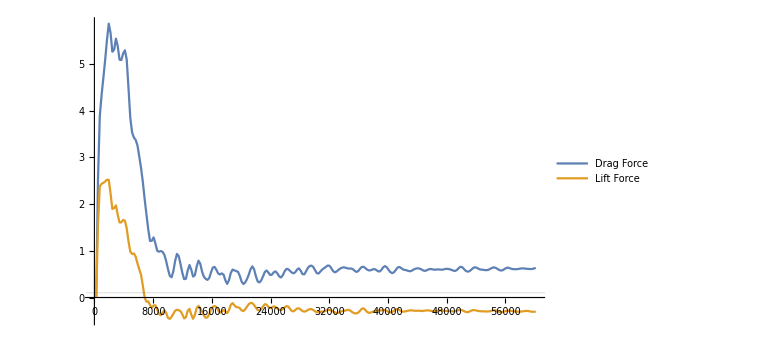

```mathematica
ListLinePlot[{{times,dragForceList[[;;,1]]}//Transpose,{times,dragForceList[[;;,2]]}//Transpose},PlotRange->All,ImageSize->Large,PlotLegends->{"Drag Force","Lift Force"},GridLines->{{},{0.1,0.1^2}}]
```

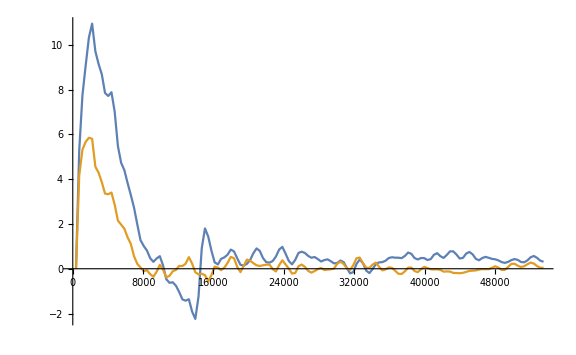

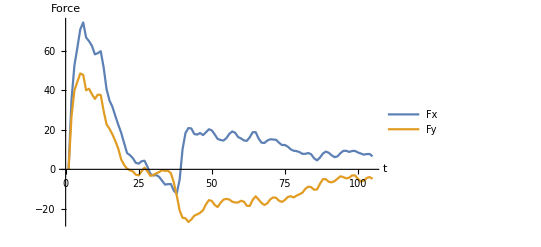

```mathematica
ListLinePlot[{forces[[All,1]],forces[[All,2]]},PlotLegends->{"Fx","Fy"},AxesLabel->{"t","Force"},PlotRange->All]
```

#### Mode Analysis

```mathematica
uyMeanx=Mean/@Transpose[uy//Abs,{1,3,2}];
uxMeanx=Mean/@Transpose[ux,{1,3,2}];
```

```mathematica
ListContourPlot[uxMeanx,PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
uyFFT=Fourier/@uyMeanX;
```

```mathematica
uyAmps=Abs[uyFFT];
```

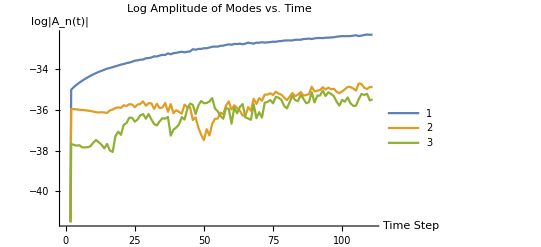

```mathematica
ListLinePlot[Log[uyAmps[[All,#]]]&/@Range[1,3],PlotLegends->Placed[Range[1,10],Above],PlotLabel->"Log Amplitude of Modes vs. Time",AxesLabel->{"Time Step","log|A_n(t)|"}]
```

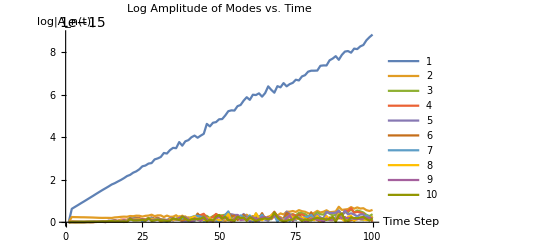

```mathematica
ListLinePlot[uyAmps[[;;100,#]]&/@Range[1,10],PlotLegends->Placed[Range[1,10],Above],PlotLabel->"Log Amplitude of Modes vs. Time",AxesLabel->{"Time Step","log|A_n(t)|"},PlotRange->All]
```

```mathematica
modeN=uyAmps[[All,1]];
fit=LinearModelFit[Transpose[{Range[Length[modeN]],Log[modeN]}],x,x];
growthRate=fit["BestFitParameters"][[1]]
```

-35.868

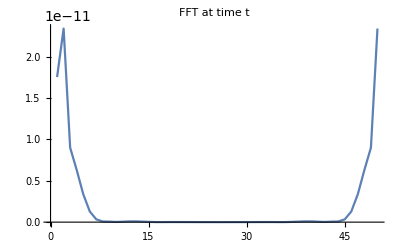

```mathematica
ListLinePlot[Abs[Fourier[uyMeanX[[-1]]]],PlotLabel->"FFT at time t",PlotRange->All]
```

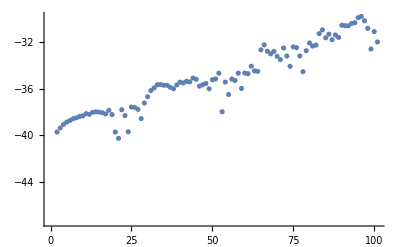

```mathematica
ListPlot[Log[uyAmps[[All,1]]]]  (*Primary mode amplitude*)
```

```mathematica
fit=LinearModelFit[Transpose[{Range[300],Log[uyAmps[[All,1]]]}],x,x];
growthRate=fit["BestFitParameters"][[1]]
```

Transpose::nmtx: The first two levels of {{1,2,3,4,5,6,7,8,9,10,«290»},{-56.0698,-38.7597,-38.5651,-38.398,-38.2706,-38.1442,-38.035,-37.9364,-37.8433,-37.7617,«675»}} cannot be transposed.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

BestFitParameters

#### QNM Data Analysis

This section is about a superficial QNM analysis but is not commented!

```mathematica
Obj[[1]]//Keys
```

{/data/0/fields/xi}

```mathematica
aa=200;
AreaFit=NonlinearModelFit[Transpose[{times[[;;aa]],(1+Obj[[;;aa,-1,1,1,1]])}],Ain+da(1-Exp[-t (2w1i)]),{Ain,da},{t}];
```

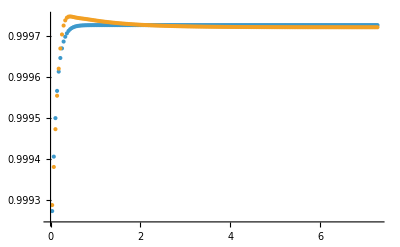

```mathematica
ListPlot[{Transpose[{times[[;;aa]],Table[AreaFit[times[[tind]]],{tind,1,aa}]}],Transpose[{times[[;;aa]],(1+Obj[[;;aa,-1,1,1,1]])}]},PlotRange->All]
```

```mathematica
AreaFit["BestFitParameters"]
AreaFit[10]
```

{Ain→0.999085,da→0.000641026}

0.999726

```mathematica
(*fy1=Obj[[;;,1,;;,;;,1]];
fx1=Obj[[;;,2,;;,;;,1]];
g3=Obj[[;;,-1,;;,;;,1]];*)
a4=Obj[[;;,2,;;,;;,1]];
```

```mathematica
a4[[-1,1,1]]//FullForm
```

```mathematica
-0.9499999996305506
```

-0.95

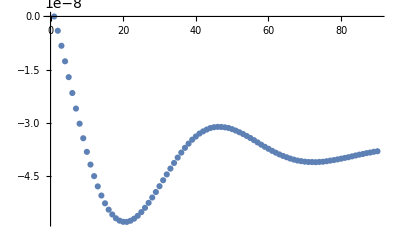

```mathematica
ListPlot[a4[[;;,1,1]]-a4[[1,1,1]]]
```

```mathematica
fy1[[-1,1,1]]
fx1[[-1,1,1]]
```

9.80632×10^-15

-6.26397×10^-15

```mathematica
2.934078881559211*^-14
```

2.93408×10^-14

```mathematica
7.958018822646281*^-15
```

7.95802×10^-15

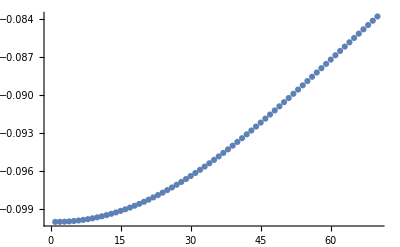

```mathematica
fy1[[;;,1,1]]//ListPlot
```

```mathematica
a4Horizon=Obj[[;;,-10,;;,;;,-1]];
```

```mathematica
Lastg3=Obj[[-1,-1,1,1,1]];
```

```mathematica
fx1=Obj[[;;,2,;;,;;,1]];
fy1=Obj[[;;,4,;;,;;,1]];
g3=Obj[[;;,5,;;,;;,1]];
b1=Obj[[;;,1,;;,;;,1]];
b2=Obj[[;;,3,;;,;;,1]];
a4=Obj[[;;,2,;;,;;,1]];
```

```mathematica
1-(-a4Horizon[[-1,10,1]])^(1/4)//FullForm
```

0.553899

```mathematica
a4Horizon[[2,10,1]]/a4Horizon[[1,10,1]]
```

0.992191

```mathematica
E^-30//N
```

```mathematica
g3[[1,1,1]]^4
```

0.0000488899

```mathematica
Timess[[5000]]
```

150.

```mathematica
10 10 0.003
```

0.3

```mathematica
a4Horizon//Length
```

1001

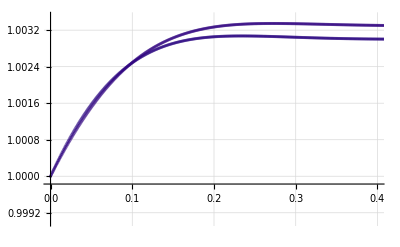

```mathematica
Timess=Table[(*dt*)dt (1(*each*) i),{i,0,(a4Horizon//Length)-1}];
Show[Table[ListPlot[Transpose[{Timess,a4Horizon[[;;,xx,1]]^(-1/4)/a4Horizon[[1,xx,1]]^(-1/4)}],PlotStyle->{RGBColor[xx/(a4Horizon[[1,;;,1]]//Length),0.01,0.5],Opacity[0.5]},(*Joined->True,*)PlotRange->All,GridLines->{Automatic}],{xx,5,(*a4Horizon[[1,;;,1]]//Length*)6}],PlotRange->{{0,0.4},{0.999,1.0035}}, PlotRange->All]
```

```mathematica
Table[1+g3[[t,1,1]] (E^(2 0.1 Timess[[t]])-1),{t,1,999}];
```

```mathematica
g3[[;;,1,1]]//Length
```

5000

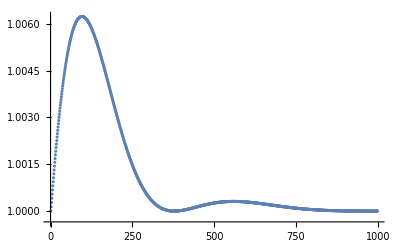

```mathematica
ListPlot[Table[1+g3[[t,1,1]]^2 (E^(2 0.1 Timess[[t]])-1),{t,1,999}]]
```

```mathematica
( 2 4.75424828181694102162317308916543566812627111042109822299035709775135175404699`55.)^-1
```

0.1051690972708126957478928121644224979862742346551882409

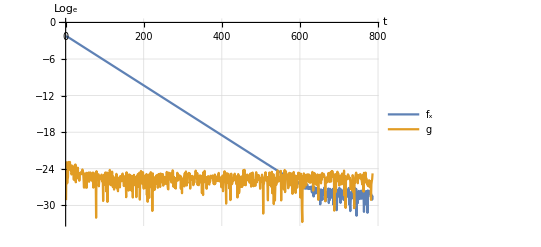

```mathematica
ListPlot[{fy1[[;;,1,1]]-fy1[[-1,1,1]]//Abs//Log,g3[[;;,1,1]]-g3[[-1,1,1]]//Abs//Log},AxesLabel->{"t","Log_e"},PlotLegends->{"f_x","g"},PlotRange->All,Joined->True,GridLines->{Automatic},GridLinesStyle->Dashed]
```

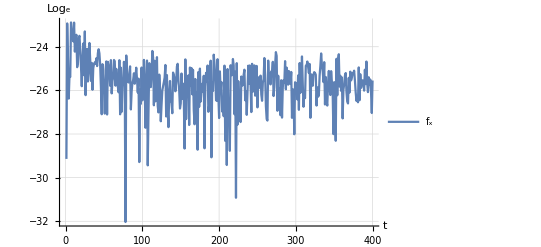

```mathematica
ListPlot[{g3[[;;400,1,1]]-g3[[-1,1,1]]//Abs//Log},AxesLabel->{"t","Log_e"},PlotLegends->{"f_x","g"},PlotRange->All,Joined->True,GridLines->{Automatic},GridLinesStyle->Dashed]
```

```mathematica
(SeriesCoefficient[u^-2 Sinh[u^4 g3[[1,1,10]]],{u,0,2}])^4//Normal
fx1[[1,1,1]]^4
```

0.0000488899

1.37861×10^-10

```mathematica
tInd=200;
Solve[E^(-b2[[tInd,1,1]])Sinh[g3[[tInd,1,1]]]==Ag E^(- 0.10(Timess[[tInd]])),Ag]
Solve[E^(-b2[[tInd,1,1]])Sinh[fx1[[tInd,1,1]]]==Afx E^(- 0.10(Timess[[tInd]])),Afx]
```

{{Ag→6.0857×10^-8}}

{{Afx→-1.74399×10^-7}}

```mathematica
aaa=1;
bbb=250;
```

```mathematica
fx1[[;;,1,1]]//Length
```

251

```mathematica
Timess=Table[(*dt*)dt (each i),{i,1,Obj//Length}];
FitResfx=Fit[Transpose[{Timess[[aaa;;bbb]],(fx1[[aaa;;bbb,1,1]]-fx1[[-1,1,1]])//Abs//Log}],{1,tt},tt]
```

-2.05169-0.136008 tt

```mathematica
Timess=Table[(*dt*)dt (each i),{i,1,Obj//Length}];
FitResg=Fit[Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb,1,1]]-g3[[-1,1,1]])//Abs//Log}],{1,tt},tt]
```

-3.11604-2.8505 tt

#### g Fits

```mathematica
w0r=3.11945159116590140667726984186100634853095499472948675543440431717732681278292`55.;
w0i=2.74667574434060639673424074409714552362302736020758738193586675171449584142752`55.;
w1r=5.16952097576222954940461885889722499194572185535488411636773071714438971882811`55.;
w1i=4.76357011692046086364514648370905218950138549522150190381951475957642922361821`55.;
w2r=7.1879308259996117388`10.;
w2i=6.7695649090762023235`10.;
w10r=21.213025329117309941952636088323838764;
w10i=20.7772323845847696293696401231951973538;
```

```mathematica
A0oft[t_]:=1-E^(1/2(w0i-w2i)(t))Cos[(w0r-w2r)t];
A1oft[t_]:=1-E^((w1i-4.817343912819517)t)Cos[(w1r-5.10630467802839)t];
(*A1inoft[t_]:=E^((w1i-4.817343912819517)t)Cos[(w1r-5.10630467802839)t]*)(*Sin[-(w0r-w1r)(t-t0)+ϕ1]*)
```

```mathematica
Obj[[1]]//Keys
```

{/data/0/fields/B1 c=2,/data/0/fields/G c=2,/data/0/fields/B1 c=1,/data/0/fields/G c=3,/data/0/fields/B2 c=2,/data/0/fields/phi c=1,/data/0/fields/G c=1,/data/0/fields/B2 c=3,/data/0/fields/phi c=2,/data/0/fields/phi c=3,/data/0/fields/B2 c=1,/data/0/fields/B1 c=3}

2501

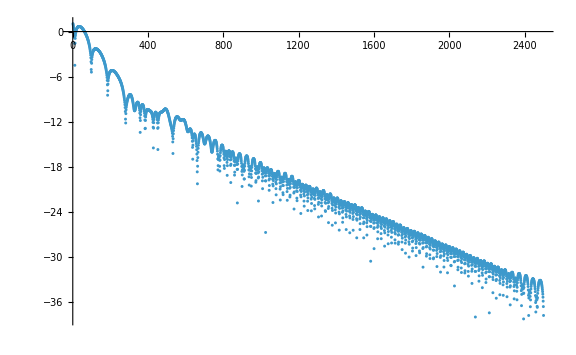

```mathematica
g3=Obj[[;;,2,;;,;;,1]];
g3//Length
ListPlot[g3[[;;,1,1]]-g3[[-1,1,1]]//Abs//Log,PlotRange->All,ImageSize->Large]
```

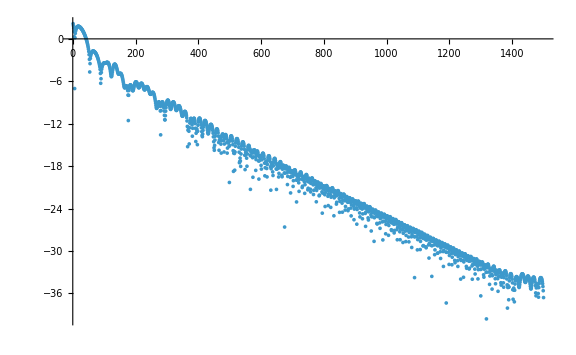

```mathematica
(w0i -w1i)
(w0r -w1r)
```

-2.01689437257985446691090573961190666587835813501391452

-2.05006938459632814272734901703621864341476686062539736

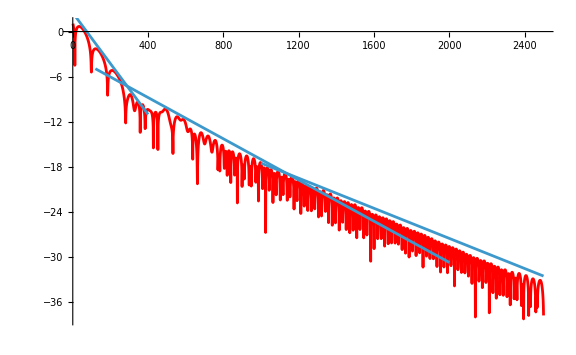

```mathematica
Show[ListPlot[g3[[;;,1,1]]-g3[[-1,1,1]]//Abs//Log,PlotRange->All,ImageSize->Large,PlotStyle->Red,Joined->True],Plot[-w2i (times[[2]]-times[[1]])t+2.5,{t,0,400}],Plot[-w0i (times[[2]]-times[[1]])t-3.3,{t,120,2000}],Plot[-(w2i -w1i)(times[[2]]-times[[1]])t-7.5,{t,1000,2500}]]
```

```mathematica
aaa=500;
bbb=1500;
Timess=times;(*Table[(*dt*)dt (each i),{i,0,g3[[;;,1,1]]//Length}];*)
Lastg3=g3[[-1,1,1]];
Datag3=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb,1,1]]-Lastg3(*Lastg3[[1,1]]*))(*//Abs//Log*)}];
Datag3Log=Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb,1,1]]-(*g3[[-1,1,1]]*)Lastg3)//Abs//Log}];
```

```mathematica
ClearAll[t];
FitResgWr=NonlinearModelFit[Datag3,(*0.1 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]*)(*+ 0.1 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]*)(*+A10 E^(-w10i (t-t0))Cos[w10r (t-t0)+ϕ2]*)(*+A0  E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0]*)(*A0oft[t]*)+0.001 E^(-w0i (t-t0))Cos[w0r(t-t0)+ϕ1g]+(*+0.1  E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2]+*)a2g E^(-0.5w2gi(t-t0))Cos[10 3.3970178726584144(t-t0)+ϕ2g] (*/.t0->0.6562487038340443*)
,{a1g,a2g,A2,A1,A10,A0,A1in,ϕ1g,ϕ2g,w1gi,w1gr,w2gi,w2gr,ϕ2,ϕ0,t0},{t(*,Timess[[aaa]],Timess[[bbb]]*)},MaxIterations->10000,ConfidenceLevel->0.9999999999];
```

```mathematica
FitResgWr["BestFitParameters"]
```

{a1g→1.,a2g→1.93145×10^18,A2→1.,A1→1.,A10→1.,A0→1.,A1in→1.,ϕ1g→0.180025,ϕ2g→6.57046,w1gi→1.,w1gr→1.,w2gi→77.6836,w2gr→1.,ϕ2→1.,ϕ0→1.,t0→1.15783}

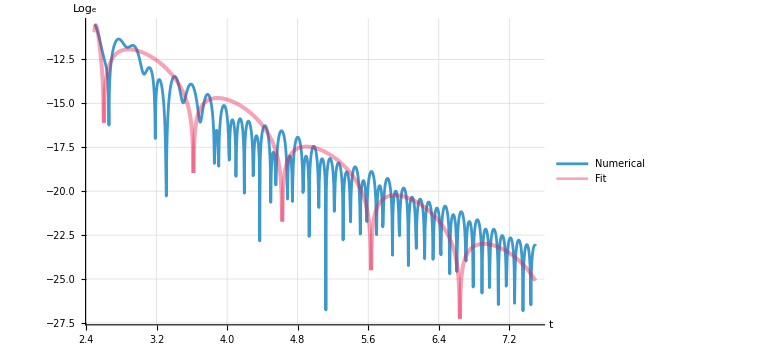

```mathematica
Timess=Table[(*dt*)dt (each i),{i,0,Obj//Length}];
Show[ListPlot[Datag3Log,PlotStyle->PointSize[0.01],PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large,Joined->True],Plot[FitResgWr[t]//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.006],Thickness[0.005],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

```mathematica
E^-15//N
```

3.05902×10^-7

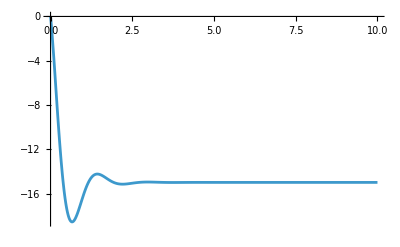

```mathematica
Plot[{A0 A0oft[t]/.FitResgWr["BestFitParameters"](*,A1 A1oft[t]/.FitResgWr["BestFitParameters"],A1in A1inoft[t]/.FitResgWr["BestFitParameters"]*)},{t,0,10},PlotRange->All]
```

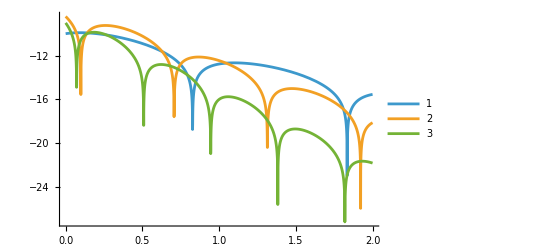

```mathematica
Plot[{A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0] A0oft[t]/.FitResgWr["BestFitParameters"]//Abs//Log,(*A0 E^(-w0i (t-times[[aaa]]))Cos[w0r (t-times[[aaa]])+ϕ0] A0oft[t]/.FitResgWr["BestFitParameters"]//Abs//Log*)0.2 A1 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1] (*A0oft[t]*)/.FitResgWr["BestFitParameters"]//Abs//Log,0.2 A2 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2] (*A0oft[t]*)/.FitResgWr["BestFitParameters"]//Abs//Log(*,A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0] A0oft[t]/.FitResgWr["BestFitParameters"]//Abs//Log,0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]/.FitResgWr["BestFitParameters"]//Abs//Log*)},{t,0,2},PlotLegends->Automatic]
```

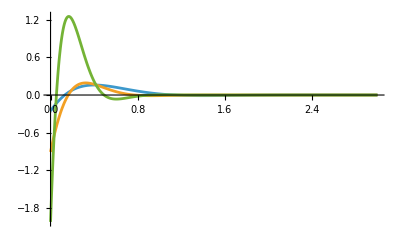

```mathematica
Plot[{A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0] (*A0oft[t]*)/.FitResgWr["BestFitParameters"],0.2 A1 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1] (*A0oft[t]*)/.FitResgWr["BestFitParameters"],0.2 A2 E^(-w2i (t-t0))Cos[w2r (t-t0)+ϕ2] (*A0oft[t]*)/.FitResgWr["BestFitParameters"](*,0.25 E^(-w1i (t-times[[aaa]]))Cos[w1r (t-times[[aaa]])+ϕ1]/.FitResgWr["BestFitParameters"]*)(*,0.1 E^(-w2i (t-times[[aaa]]))Cos[w2r (t-times[[aaa]])+ϕ2] (*A0oft[t]*)/.FitResgWr["BestFitParameters"]//Abs//Log*)(*,A0 E^(-w0i (t-t0))Cos[w0r (t-t0)+ϕ0] A0oft[t]/.FitResgWr["BestFitParameters"]//Abs//Log,0.05 E^(-w1i (t-t0))Cos[w1r (t-t0)+ϕ1]/.FitResgWr["BestFitParameters"]//Abs//Log*)},{t,0,3},PlotRange->All]
```

```mathematica
A0oft[0]
```

0

```mathematica
aaa
```

6

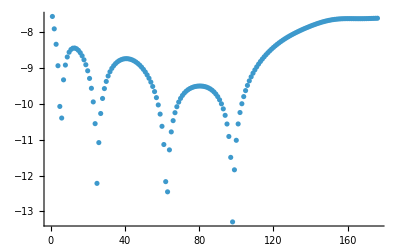

```mathematica
ListPlot[FitResgWr["FitResiduals"]//Abs//Log,PlotRange->All]
```

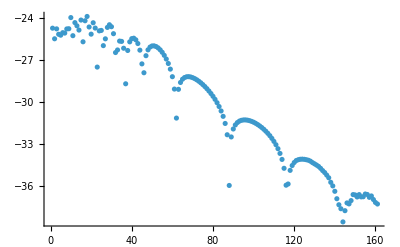

```mathematica
ListPlot[(g3[[aaa;;bbb,1,1]]-g3[[-1,1,1]]-Map[FitResgWr,times[[aaa;;bbb]]])//Abs//Log,PlotRange->All]
```

```mathematica
aaaPost=aaa+60;
bbbPost=aaa+130;
```

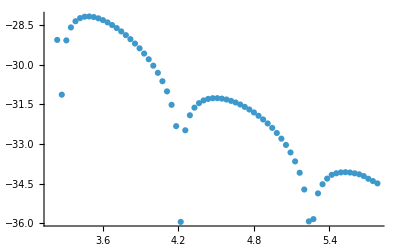

```mathematica
Datag3Post=Transpose[{Timess[[aaaPost;;bbbPost]],((g3[[aaaPost;;bbbPost,1,1]]-g3[[-1,1,1]]-Map[FitResgWr,times[[aaaPost;;bbbPost]]]))(*//Abs//Log*)}];
Datag3LogPost=Transpose[{Timess[[aaaPost;;bbbPost]],((g3[[aaaPost;;bbbPost,1,1]]-g3[[-1,1,1]]-Map[FitResgWr,times[[aaaPost;;bbbPost]]]))//Abs//Log}];
ListPlot[Datag3LogPost]
```

```mathematica
FitResgWrPost=NonlinearModelFit[Datag3Post(*Post*),A 0.1 E^(-wi (t-t0))Cos[wr(t-t0)+ϕ],{A,t0,wi,wr,ϕ},{t(*,Timess[[aaa]],Timess[[bbb]]*)}];
```

```mathematica
FitResgWrPost["BestFitParameters"]
```

{A→-10.1477,t0→-3.92034,wi→3.74895,wr→-3.30255,ϕ→6.46047}

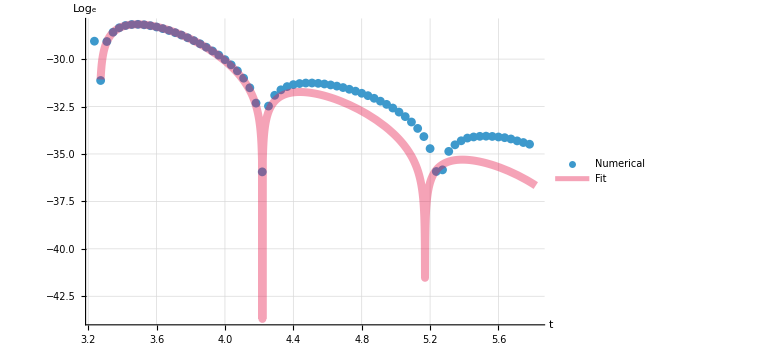

```mathematica
Timess=Table[(*dt*)dt (each i),{i,1,Obj//Length}];
Show[ListPlot[Datag3LogPost,PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large],Plot[FitResgWrPost[t]//Abs//Log,{t,Timess[[aaaPost]],Timess[[bbbPost]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.012],Thickness[0.01],Opacity[0.4],RGBColor[0.9,.1,0.3]},PlotRange->All],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

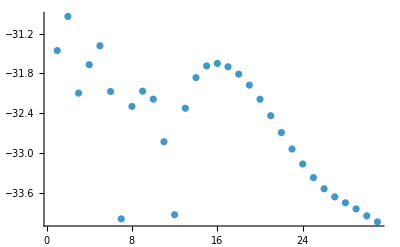

```mathematica
ListPlot[FitResgWrPost["FitResiduals"]//Abs//Log,PlotRange->All]
```

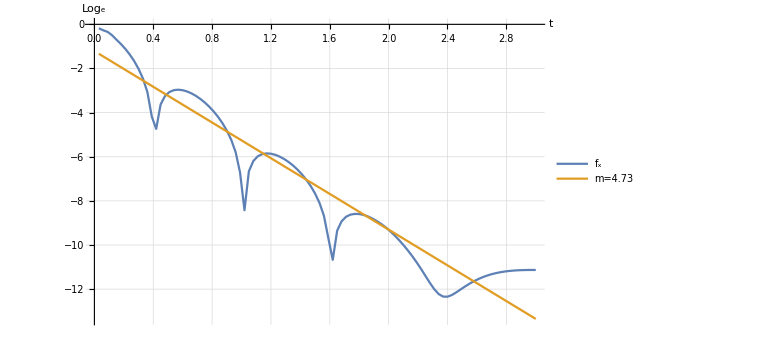

```mathematica
ListPlot[{Transpose[{Timess[[aaa;;bbb]],(g3[[aaa;;bbb,1,1]]-g3[[-1,1,1]])//Abs//Log}](*,Transpose[{Timess[[aaa;;bbb]],g3[[1]]+g3[[2,1]]  Timess[[aaa;;bbb]]}]*),Transpose[{Timess[[aaa;;bbb]],FitResg[[1]]+FitResg[[2,1]]  Timess[[aaa;;bbb]]}]},AxesLabel->{"t","Log_e"},PlotLegends->{"f_x","m=4.73"}(*,PlotRange->All*),Joined->True,GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large]
```

I subtract the initial data mode solution to the data

```mathematica
OTSol=Table[A E^(- wi(Timess[[t]]-t0))Cos[wr(Timess[[t]]-t0)]/.FitResgWr["BestFitParameters"],{t,1,Timess(*[[1;;100]]*)//Length}];
```

```mathematica
Timess(*[[1;;100]]*)//Length
```

102

```mathematica
aaaSub=90;
bbbSub=250;
```

```mathematica
90
```

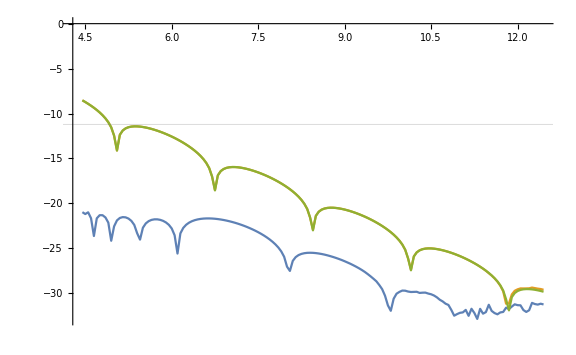

```mathematica
ListPlot[{{Timess[[aaaSub;;bbbSub]],(g3[[aaaSub;;bbbSub,1,1]]-(*g3[[-1,1,1]]*)Lastg3
)-OTSol[[aaaSub;;bbbSub]]//Abs//Log}//Transpose,Transpose[{Timess[[aaaSub;;bbbSub]],g3[[aaaSub;;bbbSub,1,1]]-(*g3[[-1,1,1]]*)Lastg3//Abs//Log}],{Timess[[aaaSub;;bbbSub]],(*(g3[[aaaSub;;bbbSub,1,1]]-g3[[-1,1,1]])-*)OTSol[[aaaSub;;bbbSub]]//Abs//Log}//Transpose},Joined->True,ImageSize->Large,GridLines->{{},{-11.2}}]
```

```mathematica
Data3gSub={Timess[[aaaSub;;bbbSub]],(g3[[aaaSub;;bbbSub,1,1]]-(*g3[[-1,1,1]]*)Lastg3[[1,1]])-OTSol[[aaaSub;;bbbSub]]}//Transpose;
Data3gLogSub={Timess[[aaaSub;;bbbSub]],(g3[[aaaSub;;bbbSub,1,1]]-(*g3[[-1,1,1]]*)Lastg3[[1,1]])-OTSol[[aaaSub;;bbbSub]]//Abs//Log}//Transpose;
```

```mathematica
FitResgWrSub=NonlinearModelFit[Data3gSub,(A E^(-wi(t-t0))Cos[wr(t-t0)])(*A2 +wi2 (t-t0)*)+A2 E^(-0.1 (t-t0))(*0.0001*)(*A3 E^(- wi3(t-t000))Cos[-wr3(t-t000)]*)(*/.t0->-0.2709949114246018*)(*/.DominantFit*),{A,wr,wi,t0,A2,wi2,t00,A3,wr3,wi3,t000},{t},ConfidenceLevel->.9999,MaxIterations->100000];
```

```mathematica
FitResgWrSub["BestFitParameters"]
```

{A→0.0000918635,wr→-10.6146,wi→12.3218,t0→0.161172,A2→-0.0000925724,wi2→1.,t00→1.,A3→1.,wr3→1.,wi3→1.,t000→1.}

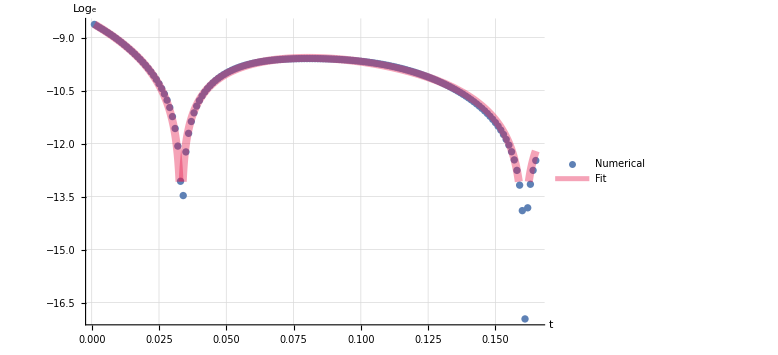

```mathematica
Show[ListPlot[Data3gLogSub,PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large],Plot[FitResgWrSub[t]//Abs//Log,{t,Timess[[aaaSub]],Timess[[bbbSub]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.012],Thickness[0.01],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

```mathematica
FitResgWrSub["BestFitParameters"]
```

{A→0.0000918635,wr→-10.6146,wi→12.3218,t0→0.161172,A2→-0.0000925724,wi2→1.,t00→1.,A3→1.,wr3→1.,wi3→1.,t000→1.}

```mathematica
OTSol2=Table[FitResgWrSub[Timess[[t]]],{t,1,Timess(*[[1;;100]]*)//Length}];
```

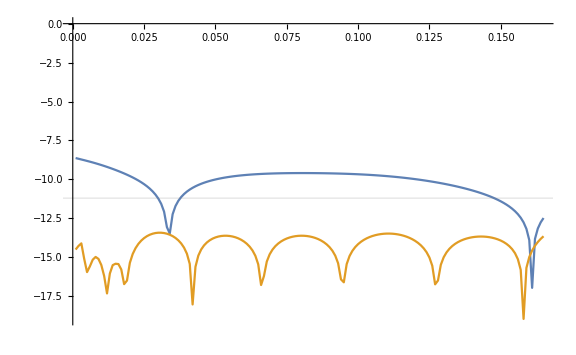

```mathematica
ListPlot[{(*{Timess[[aaaSub;;bbbSub]],(g3[[aaaSub;;bbbSub,1,1]]-(*g3[[-1,1,1]]*)Lastg3[[1,1]])//Abs//Log}//Transpose*){Timess[[aaaSub;;bbbSub]],(g3[[aaaSub;;bbbSub,1,1]]-Lastg3[[1,1]])-OTSol[[aaaSub;;bbbSub]]//Abs//Log}//Transpose,{Timess[[aaaSub;;bbbSub]],(g3[[aaaSub;;bbbSub,1,1]]-Lastg3[[1,1]])-OTSol[[aaaSub;;bbbSub]]-OTSol2[[aaaSub;;bbbSub]]//Abs//Log}//Transpose},Joined->True,ImageSize->Large,GridLines->{{},{-11.2}},PlotRange->All]
```

#### fx Fits

```mathematica
Timess=Table[(*dt*)dt (each i),{i,0,fx1[[;;,1,1]]//Length}];
Timess//Length
aaa=10;
bbb=200;
```

395

```mathematica
Datafx=Transpose[{Timess[[aaa;;bbb]],(fx1[[aaa;;bbb,1,1]]-fx1[[-1,1,1]])(*//Abs//Log*)}];
DatafxLog=Transpose[{Timess[[aaa;;bbb]],(fx1[[aaa;;bbb,1,1]]-fx1[[-1,1,1]])//Abs//Log}];
```

```mathematica
fxFit=NonlinearModelFit[DatafxLog,A -wi(t) (* A- wi(t(*-t0*))*)(*(A E^(- wi(t-t0))Cos[wr(t-t0)](*//Abs//Log*))*),{A,wr,t0,wi},{t(*,Timess[[aaa]],Timess[[bbb]]*)},ConfidenceLevel->0.9999999];
```

```mathematica
fxFit["BestFitParameters"]
```

{A→-2.19667,wr→0.,t0→0.,wi→0.136235}

```mathematica
Bands[t_]=fxFit["MeanPredictionBands"];
```

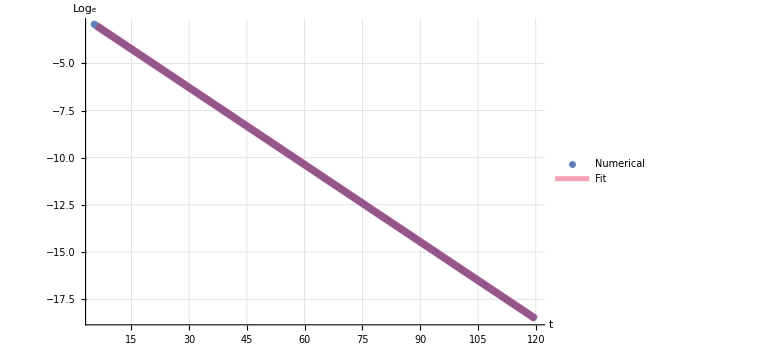

```mathematica
Timess=Table[(*dt*)dt (each i),{i,1,Obj//Length}];
Show[ListPlot[DatafxLog,PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large],Plot[{fxFit[t](*,Bands[t]*)}(*//Abs//Log*),{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{{PointSize[0.012],Thickness[0.01],Opacity[0.4],RGBColor[0.9,.1,0.3]},{Thickness[0.001]}},Filling->{2->{1}}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

I subtract the initial data mode solution to the data

```mathematica
fxFitVec=Table[A E^(-wi(Timess[[t]]))/.fxFit["BestFitParameters"],{t,1,Timess(*[[1;;100]]*)//Length}];
fxFitVecLog=Table[A+ (-  wi(Timess[[t]]))/.fxFit["BestFitParameters"],{t,1,Timess(*[[1;;100]]*)//Length}];
```

```mathematica
Timess(*[[1;;100]]*)//Length
```

787

```mathematica
E^-5//N
```

0.00673795

```mathematica
aaaSub=1;
bbbSub=50;
```

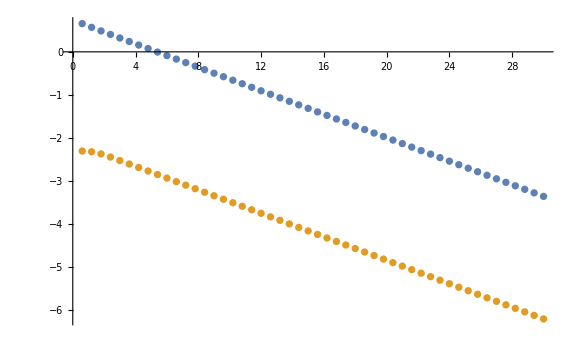

```mathematica
ListPlot[{{Timess[[aaaSub;;bbbSub]],(((fx1[[aaaSub;;bbbSub,1,1]]-fx1[[-1,1,1]]))-fxFitVec[[aaaSub;;bbbSub]])//Abs//Log}//Transpose(*,{Timess[[aaaSub;;bbbSub]],fyFitVec[[aaaSub;;bbbSub]]}//Transpose*),Transpose[{Timess[[aaaSub;;bbbSub]],fx1[[aaaSub;;bbbSub,1,1]]-fx1[[-1,1,1]]//Abs//Log}]},(*Joined->True,*)ImageSize->Large,GridLines->{{},{-11.2}},PlotRange->All]
```

```mathematica
Data3fxSub={Timess[[aaaSub;;bbbSub]],(fy1[[aaaSub;;bbbSub,1,1]]-fy1[[-1,1,1]])-fyFitVec[[aaaSub;;bbbSub]]}//Transpose;
Data3fyLogSub={Timess[[aaaSub;;bbbSub]],(fy1[[aaaSub;;bbbSub,1,1]]-fy1[[-1,1,1]])-fyFitVec[[aaaSub;;bbbSub]]//Abs//Log}//Transpose;
```

```mathematica
FitResfyWrSub=NonlinearModelFit[Data3fyLogSub,(A E^(wi(t-t0))+Cos[3(t-t0)])(*A2 +wi2 (t-t0)*)(*+A2 E^(-0.1 (t-t0))*)(*0.0001*)(*A3 E^(- wi3(t-t000))Cos[-wr3(t-t000)]*)(*/.t0->-0.2709949114246018*)(*/.DominantFit*),{A,wr,wi,t0},{t},ConfidenceLevel->.9,MaxIterations->100000];
```

```mathematica
FitResfyWrSub["BestFitParameters"]
```

{A→-8.08584,wr→1.,wi→0.0154088,t0→20.9726}

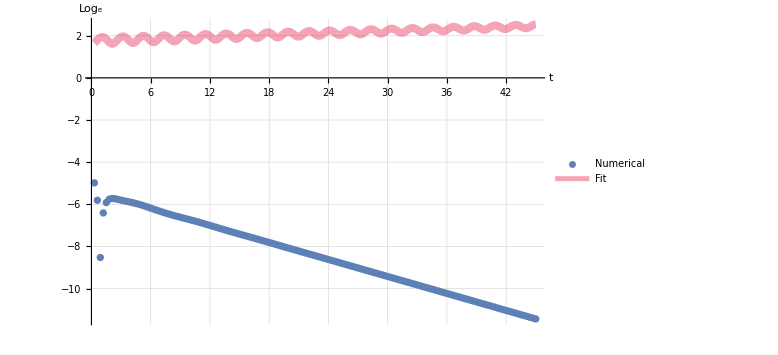

```mathematica
Show[ListPlot[Data3fyLogSub,PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large],Plot[FitResfyWrSub[t](*//Abs//Log*),{t,Timess[[aaaSub]],Timess[[bbbSub]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.012],Thickness[0.01],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

#### fy Fits

```mathematica
Timess=Table[(*dt*)dt (each i),{i,0,fy1[[;;,1,1]]//Length}];
Timess//Length
aaa=10;
bbb=1600;
```

1602

```mathematica
Lastfy1=7.958018822646281*^-15;
```

```mathematica
Datafy=Transpose[{Timess[[aaa;;bbb]],(fy1[[aaa;;bbb,1,1]]-Lastfy1)(*//Abs//Log*)}];
DatafyLog=Transpose[{Timess[[aaa;;bbb]],(fy1[[aaa;;bbb,1,1]]-Lastfy1)//Abs//Log}];
```

```mathematica
fyFit=NonlinearModelFit[Datafy,A E^( -wi(t)) (* A- wi(t(*-t0*))*)(*(A E^(- wi(t-t0))Cos[wr(t-t0)](*//Abs//Log*))*),{A,wr,t0,wi},{t(*,Timess[[aaa]],Timess[[bbb]]*)},ConfidenceLevel->0.9999999];
```

```mathematica
fyFit["BestFitParameters"]
```

{A→-0.109274,wr→1.,t0→1.,wi→0.134072}

```mathematica
{A->-2.198660223143842,wr->0.,t0->0.,wi->0.13621032907945899}
```

{A→-2.19866,wr→0.,t0→0.,wi→0.13621}

```mathematica
Bands[t_]=fyFit["MeanPredictionBands"];
```

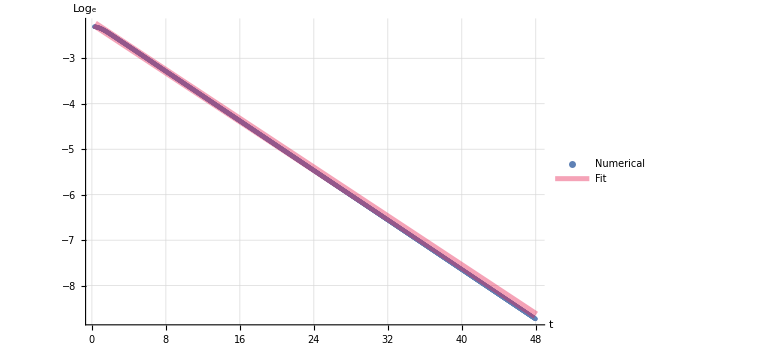

```mathematica
Timess=Table[(*dt*)dt (each i),{i,1,Obj//Length}];
Show[ListPlot[DatafyLog,PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large],Plot[{fyFit[t](*,Bands[t]*)}//Abs//Log,{t,Timess[[aaa]],Timess[[bbb]]},PlotLegends->{"Fit"},PlotStyle->{{PointSize[0.012],Thickness[0.01],Opacity[0.4],RGBColor[0.9,.1,0.3]},{Thickness[0.001]}},Filling->{2->{1}}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

I subtract the initial data mode solution to the data

```mathematica
fyFitVec=Table[A E^(-wi(Timess[[t]]))/.fyFit["BestFitParameters"],{t,1,Timess(*[[1;;100]]*)//Length}];
fyFitVecLog=Table[A+ (-  wi(Timess[[t]]))/.fyFit["BestFitParameters"],{t,1,Timess(*[[1;;100]]*)//Length}];
```

```mathematica
Timess(*[[1;;100]]*)//Length
```

1601

```mathematica
E^-5//N
```

0.00673795

```mathematica
aaaSub=1;
bbbSub=1599;
```

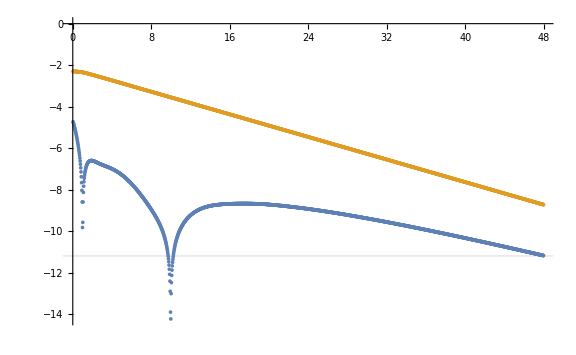

```mathematica
ListPlot[{{Timess[[aaaSub;;bbbSub]],(((fy1[[aaaSub;;bbbSub,1,1]]-Lastfy1))-fyFitVec[[aaaSub;;bbbSub]])//Abs//Log}//Transpose(*,{Timess[[aaaSub;;bbbSub]],fyFitVec[[aaaSub;;bbbSub]]}//Transpose*),Transpose[{Timess[[aaaSub;;bbbSub]],fy1[[aaaSub;;bbbSub,1,1]]-Lastfy1//Abs//Log}]},(*Joined->True,*)ImageSize->Large,GridLines->{{},{-11.2}},PlotRange->All]
```

```mathematica
Data3fySub={Timess[[aaaSub;;bbbSub]],(fy1[[aaaSub;;bbbSub,1,1]]-Lastfy1)-fyFitVec[[aaaSub;;bbbSub]]}//Transpose;
Data3fyLogSub={Timess[[aaaSub;;bbbSub]],(fy1[[aaaSub;;bbbSub,1,1]]-Lastfy1)-fyFitVec[[aaaSub;;bbbSub]]//Abs//Log}//Transpose;
```

```mathematica
FitResfyWrSub=NonlinearModelFit[Data3fySub,(A E^(-wi(t-t0))Cos[100wr(t-t0)])(*A2 +wi2 (t-t0)*)(*+A2 E^(-0.1 (t-t0))*)(*0.0001*)(*A3 E^(- wi3(t-t000))Cos[-wr3(t-t000)]*)(*/.t0->-0.2709949114246018*)(*/.DominantFit*),{A,wr,wi,t0},{t},ConfidenceLevel->.9,MaxIterations->100000];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100000 iterations.

```mathematica
FitResfyWrSub["BestFitParameters"]
```

{A→-3.51346×10^-129,wr→0.0000401047,wi→0.754306,t0→392.512}

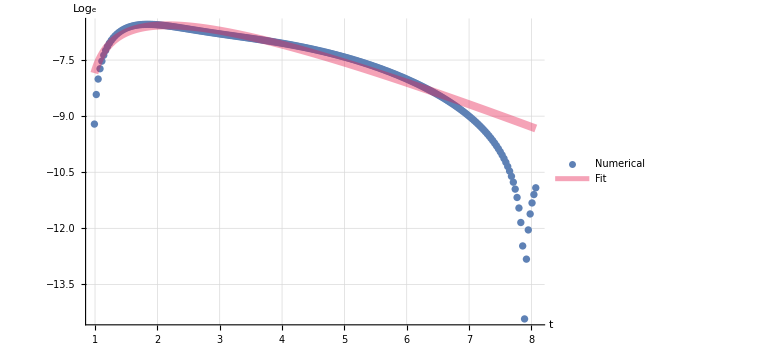

```mathematica
Show[ListPlot[Data3fyLogSub,PlotLegends->{"Numerical"},GridLines->{Automatic},GridLinesStyle->Dashed,AxesStyle->{{Thick,10},{Thick,10}},ImageSize->Large],Plot[FitResfyWrSub[t]//Abs//Log,{t,Timess[[aaaSub]],Timess[[bbbSub]]},PlotLegends->{"Fit"},PlotStyle->{PointSize[0.012],Thickness[0.01],Opacity[0.4],RGBColor[0.9,.1,0.3]}],PlotRange->All,AxesLabel->{"t","Log_e"}]
```

#### Convergence Analysis

```mathematica
precision=50;
```

```mathematica
init=0;
end=2744;
each=28;
FNames=Table[StringJoin["gauge_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
Name1=Table[StringJoin["/home/giulio/University/PhD/JeccoGt2/examples/convergence_tests/t10_Nx16/",
FNames[[i]],".h5"],{i,FNames//Length}];
Name2=Table[StringJoin["/home/giulio/University/PhD/JeccoGt2/examples/convergence_tests/t10_Nx32/",
FNames[[i]],".h5"],{i,FNames//Length}];
(*Name3=Table[StringJoin["/home/giulio/University/PhD/Simulations/convergence_tests/t10_Nx64/",
FNames[[i]],".h5"],{i,FNames//Length}]*)
dt=N[Import[Name1[[2]],"Attributes"][[3,1]],precision];
times=Table[tim dt each+init dt,{tim,1,Name1//Length}];
```

```mathematica
dt//FullForm
```

0.00363636

```mathematica
DataL=Table[Import[Name1[[i]],"Data"](*[[1]]*),{i,1,Name1//Length}];
```

```mathematica
DataM=Table[Import[Name2[[i]],"Data"](*[[1]]*),{i,1,Name2//Length}];
```

```mathematica
DataH=Table[Import[Name3[[i]],"Data"](*[[1]]*),{i,1,Name3//Length}];
```

```mathematica
ay=Abs[Import[Name1[[1]],"Attributes"][[5,3,1]]];
by=-Abs[Import[Name1[[1]],"Attributes"][[5,3,1]]];
Ly=ay-by;
ax=Abs[Import[Name1[[1]],"Attributes"][[5,3,2]]];
bx=-Abs[Import[Name1[[1]],"Attributes"][[5,3,2]]];
Lx=ax-bx;
```

```mathematica
DataL[[1,1,1]]//Precision
```

MachinePrecision

```mathematica
xValues[[1]]//Precision
```

MachinePrecision

```mathematica
xValues=Range[bx,ax,(ax 2)/(DataL[[1,1,1]]//Length)][[1;;-2]];
yValues=Range[by,ay,(ay 2)/(DataL[[1,1]]//Length)][[1;;-2]];
nx=xValues//Length;
ny=yValues//Length;
```

```mathematica
xValues
```

{-5.,-4.375,-3.75,-3.125,-2.5,-1.875,-1.25,-0.625,0.,0.625,1.25,1.875,2.5,3.125,3.75,4.375}

```mathematica
(ax 2)/(DataL[[1,1,1]]//Length)//FullForm
```

0.625

```mathematica
AL=Join[DataL[[;;,-3]],DataL[[;;,4]],DataL[[;;,-4]],DataL[[;;,-9]],4];
AM=Join[DataM[[;;,-3]],DataM[[;;,4]],DataM[[;;,-4]],DataM[[;;,-9]],4];
AH=Join[DataH[[;;,-3]],DataH[[;;,4]],DataH[[;;,-4]],DataH[[;;,-9]],4];
```

Part::partw: Part -3 of <|/data/0/fields/xi→{{{-2.44929×10^-17},{-0.0382683},{-0.0707107},{-0.092388},{-0.1},{-0.092388},{-0.0707107},{-0.0382683},{1.22465×10^-17},{0.0382683},{0.0707107},{0.092388},{0.1},{0.092388},{0.0707107},{0.0382683}},{«1»},«12»,{«1»},{{-2.44929×10^-17},{-0.0382683},{-0.0707107},{-0.092388},«8»,{0.1},{0.092388},{0.0707107},{0.0382683}}}|> does not exist.

Part::partw: Part 4 of <|/data/0/fields/xi→{{{-2.44929×10^-17},{-0.0382683},{-0.0707107},{-0.092388},{-0.1},{-0.092388},{-0.0707107},{-0.0382683},{1.22465×10^-17},{0.0382683},{0.0707107},{0.092388},{0.1},{0.092388},{0.0707107},{0.0382683}},{«1»},«12»,{«1»},{{-2.44929×10^-17},{-0.0382683},{-0.0707107},{-0.092388},«8»,{0.1},{0.092388},{0.0707107},{0.0382683}}}|> does not exist.

Part::partw: Part -4 of <|/data/0/fields/xi→{{{-2.44929×10^-17},{-0.0382683},{-0.0707107},{-0.092388},{-0.1},{-0.092388},{-0.0707107},{-0.0382683},{1.22465×10^-17},{0.0382683},{0.0707107},{0.092388},{0.1},{0.092388},{0.0707107},{0.0382683}},{«1»},«12»,{«1»},{{-2.44929×10^-17},{-0.0382683},{-0.0707107},{-0.092388},«8»,{0.1},{0.092388},{0.0707107},{0.0382683}}}|> does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Join::normal1: Expression {<|/data/0/fields/xi→{{{-2.44929×10^-17},{-0.0382683},{-0.0707107},{-0.092388},{-0.1},{-0.092388},{-0.0707107},{-0.0382683},{1.22465×10^-17},{0.0382683},{0.0707107},{0.092388},{0.1},{0.092388},{0.0707107},{0.0382683}},«14»,{{-2.44929×10^-17},{-0.0382683},{-0.0707107},{-0.092388},«8»,{0.1},{0.092388},{0.0707107},{0.0382683}}}|>,«10»}⟦«1»⟧ at position 1 is expected to have nonatomic subexpression at level 4.

Part::partw: Part -3 of <|/data/0/fields/xi→{«1»}|> does not exist.

Part::partw: Part 4 of <|/data/0/fields/xi→{«1»}|> does not exist.

Part::partw: Part -4 of <|/data/0/fields/xi→{«1»}|> does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Join::normal1: Expression {«1»}⟦1;;All,-3⟧ at position 1 is expected to have nonatomic subexpression at level 4.

Part::partw: Part -3 of <|/data/0/fields/xi→{{{-2.44929×10^-17},{-0.00980171},{-0.019509},{-0.0290285},{-0.0382683},{-0.0471397},{-0.055557},{-0.0634393},{-0.0707107},{-0.077301},{-0.083147},«42»,{0.0881921},{0.083147},{0.077301},{0.0707107},{0.0634393},{0.055557},{0.0471397},{0.0382683},{0.0290285},{0.019509},{0.00980171}},«62»,{«1»}}|> does not exist.

Part::partw: Part 4 of <|/data/0/fields/xi→{{{-2.44929×10^-17},{-0.00980171},{-0.019509},{-0.0290285},{-0.0382683},{-0.0471397},{-0.055557},{-0.0634393},{-0.0707107},{-0.077301},{-0.083147},«42»,{0.0881921},{0.083147},{0.077301},{0.0707107},{0.0634393},{0.055557},{0.0471397},{0.0382683},{0.0290285},{0.019509},{0.00980171}},«62»,{«1»}}|> does not exist.

Part::partw: Part -4 of <|/data/0/fields/xi→{{{-2.44929×10^-17},{-0.00980171},{-0.019509},{-0.0290285},{-0.0382683},{-0.0471397},{-0.055557},{-0.0634393},{-0.0707107},{-0.077301},{-0.083147},«42»,{0.0881921},{0.083147},{0.077301},{0.0707107},{0.0634393},{0.055557},{0.0471397},{0.0382683},{0.0290285},{0.019509},{0.00980171}},«62»,{«1»}}|> does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Join::normal1: Expression «1» at position 1 is expected to have nonatomic subexpression at level 4.

```mathematica
AL1=DataL[[;;,-3]];
AL2=DataL[[;;,4]];
AL3=DataL[[;;,-4]];
AL4=DataL[[;;,-9]];
```

```mathematica
AM1=DataM[[;;,-3]];
AM2=DataM[[;;,4]];
AM3=DataM[[;;,-4]];
AM4=DataM[[;;,-9]];
```

```mathematica
AH1=DataH[[;;,-3]];
AH2=DataH[[;;,4]];
AH3=DataH[[;;,-4]];
AH4=DataH[[;;,-9]];
```

```mathematica
Ax=0.1;
nx=1;
vx=1;
xMax=5;
Lx=10;
a4=-1;
Lx=10;
Exactxi[t_,x_,y_]:=Ax Sin[2 Pi nx/Lx(xMax-x+vx t)];
ExactA[t_,x_,y_,u_]:=1/u^2+2 Exactxi[t,x,y]/u+Exactxi[t,x,y]^2+a4 u;
ExactAOuter[t_,x_,y_,u_]:=ExactA[t,x,y,u];
ExactAInner[t_,x_,y_,u_]:=1/u(ExactA[t,x,y,u]-(1/u^2+2 Exactxi[t,x,y]/u+Exactxi[t,x,y]^2+a4 u/(1+Exactxi[t,x,y] u-2D[Exactxi[tt,x,y],tt]/.tt->t)));
```

```mathematica
Timess=times;
```

```mathematica
ExactxiVect=Table[Exactxi[Timess[[t]],xValues[[j]],yValues[[i]]] ,{t,1,Timess//Length},{i,xValues//Length},{j,yValues//Length}];
```

```mathematica
ExactAInnerVect=Table[ExactAInner[Timess[[t]],xValues[[j]],yValues[[i]],uValues1[[u]]] ,{t,1,Timess//Length},{i,xValues//Length},{j,yValues//Length},{u,2,uValues1//Length}];
```

```mathematica
ExactAOuter2Vect=Table[ExactAOuter[Timess[[t]],xValues[[j]],yValues[[i]],uValues2[[u]]] ,{t,1,Timess//Length},{i,xValues//Length},{j,yValues//Length},{u,uValues2//Length}];
ExactAOuter3Vect=Table[ExactAOuter[Timess[[t]],xValues[[j]],yValues[[i]],uValues3[[u]]] ,{t,1,Timess//Length},{i,xValues//Length},{j,yValues//Length},{u,uValues3//Length}];
ExactAOuter4Vect=Table[ExactAOuter[Timess[[t]],xValues[[j]],yValues[[i]],uValues4[[u]]] ,{t,1,Timess//Length},{i,xValues//Length},{j,yValues//Length},{u,uValues4//Length}];
```

#### Absolute Convergence

10.08

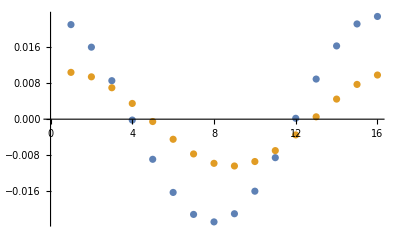

```mathematica
t=-1;
times[[t]]
x=10;
ListPlot[{ExactxiVect[[t,x]]-DataL[[t,1,x,;;,1]],(ExactxiVect[[t,x]]-DataM[[t,1,x,;;;;2,1]])(*,(ExactxiVect[[t,x]]-DataH[[t,1,x,;;;;4,1]])*)}]
```

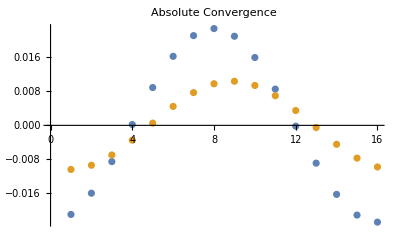

```mathematica
t=-1;
x=8;
(*ListPlot[{DataL[[t,1,;;,x,1]]-DataM[[t,1,;;;;2,x,1]],2^2(DataM[[t,1,;;;;2,x,1]]-DataH[[t,1,;;;;4,x,1]])},PlotLabel->"Self Convergence"]*)
ListPlot[{DataL[[t,1,x,;;,1]]-ExactxiVect[[t,x]],(DataM[[t,1,x,;;;;2,1]]-ExactxiVect[[t,x,;;]])(*,4(DataH[[t,1,x,;;;;4,1]]-ExactxiVect[[t,x,;;]])*)},PlotLabel->"Absolute Convergence"]
```

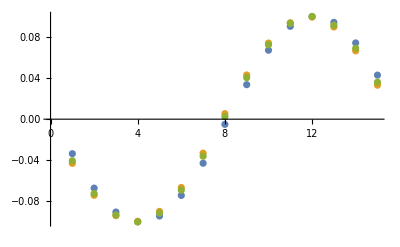

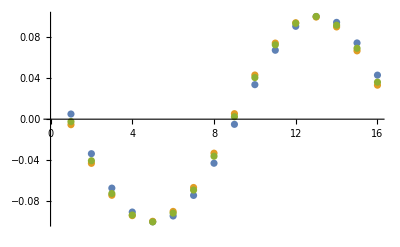

```mathematica
ListPlot[{ExactxiVect[[t,x,2;;]],DataM[[t,1,x,3;;;;2,1]],DataH[[t,1,x,5;;;;4,1]]}]
ListPlot[{ExactxiVect[[t,x,;;]],DataM[[t,1,x,;;;;2,1]],DataH[[t,1,x,;;;;4,1]]}]
```

```mathematica
LminusEInner=AL1[[;;,;;,;;,2;;]]-ExactAInnerVect;
MminusEInner=AM1[[;;,;;;;2,;;;;2,2;;]]-ExactAInnerVect;
HminusEInner=AH1[[;;,;;;;4,;;;;4,2;;]]-ExactAInnerVect;
```

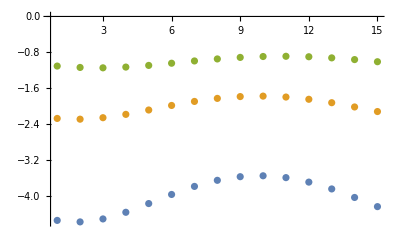

```mathematica
t=10;
ListPlot[{4HminusEInner[[t,x,2;;,-1]],2MminusEInner[[t,x,2;;,u]],LminusEInner[[t,x,;;-2,u]]},PlotRange->All]
```

```mathematica
AM2[[;;,2;;;;2,2;;;;2,;;]]//Dimensions
ExactAOuter2Vect[[;;,;;-2,;;-2]]//Dimensions
```

{99,16,16,28}

{99,15,15,28}

```mathematica
MminusEOuter2=AM2[[;;,;;;;2,;;;;2,;;]]-ExactAOuter2Vect[[;;,;;,;;]];
MminusEOuter3=AM3[[;;,;;;;2,;;;;2,;;]]-ExactAOuter3Vect[[;;,;;,;;]];
MminusEOuter4=AM4[[;;,;;;;2,;;;;2,;;]]-ExactAOuter4Vect[[;;,;;,;;]];
```

```mathematica
HminusEOuter2=AH2[[;;,;;;;4,;;;;4,;;]]-ExactAOuter2Vect[[;;,;;,;;]];
HminusEOuter3=AH3[[;;,;;;;4,;;;;4,;;]]-ExactAOuter3Vect[[;;,;;,;;]];
HminusEOuter4=AH4[[;;,;;;;4,;;;;4,;;]]-ExactAOuter4Vect[[;;,;;,;;]];
```

```mathematica
LminusEOuter2=AL2[[;;,;;,;;,;;]]-ExactAOuter2Vect[[;;,;;,;;]];
LminusEOuter3=AL3[[;;,;;,;;,;;]]-ExactAOuter3Vect[[;;,;;,;;]];
LminusEOuter4=AL4[[;;,;;,;;,;;]]-ExactAOuter4Vect[[;;,;;,;;]];
```

```mathematica
u=1;
x=-1;
y=10;
t=-1;
```

```mathematica
a4
```

-1

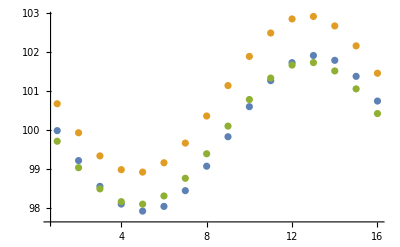

```mathematica
ListPlot[{HminusEOuter2[[t,x,;;,u]],1MminusEOuter2[[t,x,;;,u]],LminusEOuter2[[t,x,;;,u]]},PlotRange->All]
```

```mathematica
SumLinnerSquareSum=Table[Sum[LminusEInner[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,1,uValues1//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
SumLouterSquareSum=Table[Sum[LminusEOuter2[[ti,x,y,u]]^2+LminusEOuter3[[ti,x,y,u]]^2+LminusEOuter4[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,2,uValues2//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
SumMinnerSquareSum=Table[Sum[MminusEInner[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,1,uValues1//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
SumMouterSquareSum=Table[Sum[MminusEOuter2[[ti,x,y,u]]^2+MminusEOuter3[[ti,x,y,u]]^2+MminusEOuter4[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,2,uValues2//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
SumHinnerSquareSum=Table[Sum[HminusEInner[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,1,uValues1//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
SumHouterSquareSum=Table[Sum[HminusEOuter2[[ti,x,y,u]]^2+HminusEOuter3[[ti,x,y,u]]^2+HminusEOuter4[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,2,uValues2//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
```

Part::partw: Part 12 of {{{-1.14338,-1.14337,-1.14335,-1.14333,-1.1433,-1.14328,-1.14325,-1.14323,-1.14321,-1.1432,«1»},{-1.13512,-1.13534,-1.13582,-1.13638,-1.13704,-1.13771,-1.13837,-1.13894,-1.13939,-1.13967,«1»},«8»,«6»},{{-1.14338,-1.14337,-1.14335,«5»,-1.14321,-1.1432,«1»},«9»,«6»},«7»,{«1»},«6»} does not exist.

Part::partw: Part 12 of {-1.14338,-1.14337,-1.14335,-1.14333,-1.1433,-1.14328,-1.14325,-1.14323,-1.14321,-1.1432,«1»} does not exist.

Part::partw: Part 12 of {{{-1.14338,-1.14337,-1.14335,-1.14333,-1.1433,-1.14328,-1.14325,-1.14323,-1.14321,-1.1432,«1»},{-1.13512,-1.13534,-1.13582,-1.13638,-1.13704,-1.13771,-1.13837,-1.13894,-1.13939,-1.13967,«1»},«8»,«6»},{{-1.14338,-1.14337,-1.14335,«5»,-1.14321,-1.1432,«1»},«9»,«6»},«7»,{«1»},«6»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

$Aborted

Part::partw: Part 12 of {{{-1.14338,-1.14337,-1.14335,-1.14333,-1.1433,-1.14328,-1.14325,-1.14323,-1.14321,-1.1432,«1»},{-1.13512,-1.13537,-1.13584,-1.13638,-1.13707,-1.13771,-1.1384,-1.13894,-1.13942,-1.13967,«1»},«8»,«6»},{{-1.14338,-1.14337,-1.14335,«5»,-1.14321,-1.1432,«1»},«9»,«6»},«7»,{«1»},«6»} does not exist.

Part::partw: Part 12 of {-1.14338,-1.14337,-1.14335,-1.14333,-1.1433,-1.14328,-1.14325,-1.14323,-1.14321,-1.1432,«1»} does not exist.

Part::partw: Part 12 of {{{-1.14338,-1.14337,-1.14335,-1.14333,-1.1433,-1.14328,-1.14325,-1.14323,-1.14321,-1.1432,«1»},{-1.13512,-1.13537,-1.13584,-1.13638,-1.13707,-1.13771,-1.1384,-1.13894,-1.13942,-1.13967,«1»},«8»,«6»},{{-1.14338,-1.14337,-1.14335,«5»,-1.14321,-1.1432,«1»},«9»,«6»},«7»,{«1»},«6»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

$Aborted

Part::partw: Part 12 of {{{-1.14338,-1.14337,-1.14335,-1.14333,-1.1433,-1.14328,-1.14325,-1.14323,-1.14321,-1.1432,«1»},{-1.13512,-1.13537,-1.13584,-1.13638,-1.13707,-1.13771,-1.1384,-1.13894,-1.13942,-1.13967,«1»},«8»,«6»},{{-1.14338,-1.14337,-1.14335,«5»,-1.14321,-1.1432,«1»},«9»,«6»},«7»,{«1»},«6»} does not exist.

Part::partw: Part 12 of {-1.14338,-1.14337,-1.14335,-1.14333,-1.1433,-1.14328,-1.14325,-1.14323,-1.14321,-1.1432,«1»} does not exist.

Part::partw: Part 12 of {{{-1.14338,-1.14337,-1.14335,-1.14333,-1.1433,-1.14328,-1.14325,-1.14323,-1.14321,-1.1432,«1»},{-1.13512,-1.13537,-1.13584,-1.13638,-1.13707,-1.13771,-1.1384,-1.13894,-1.13942,-1.13967,«1»},«8»,«6»},{{-1.14338,-1.14337,-1.14335,«5»,-1.14321,-1.1432,«1»},«9»,«6»},«7»,{«1»},«6»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

$Aborted

```mathematica
Lsqrt=Table[Sqrt[SumLinnerSquareSum[[ti]]+SumLouterSquareSum[[ti]]],{ti,1,SumLinnerSquareSum//Length}];
Msqrt=Table[Sqrt[SumMinnerSquareSum[[ti]]+SumMouterSquareSum[[ti]]],{ti,1,SumLinnerSquareSum//Length}];
Hsqrt=Table[Sqrt[SumHinnerSquareSum[[ti]]+SumHouterSquareSum[[ti]]],{ti,1,SumLinnerSquareSum//Length}];
```

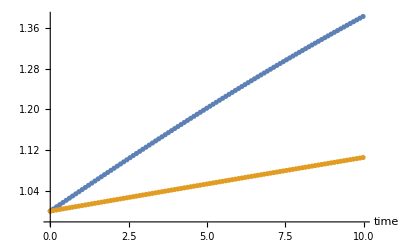

```mathematica
{Table[Lsqrt[[i]]/Msqrt[[i]],{i,1,Msqrt//Length}],Table[Msqrt[[i]]/Hsqrt[[i]],{i,1,Msqrt//Length}]}//ListPlot[{Transpose[{Range[0,dt end,dt each],#[[1]]}],Transpose[{Range[0,dt end,dt each],#[[2]]}]}(*,Joined->True*),PlotRange->All,GridLines->{{},{4,4.4}},AxesLabel->{"time"}(*,PlotLabel->"ξ Convergence test",PlotLegends->{"(| SubscriptBox[ξ, 16] - SubscriptBox[ξ, exact]SuperscriptBox[|, FractionBox[1, 2]])/(| SubscriptBox[ξ, 32] - SubscriptBox[ξ, exact]SuperscriptBox[|, FractionBox[1, 2]])","(| SubscriptBox[ξ, 32] - SubscriptBox[ξ, exact]SuperscriptBox[|, FractionBox[1, 2]])/(| SubscriptBox[ξ, 64] - SubscriptBox[ξ, exact]SuperscriptBox[|, FractionBox[1, 2]])"}*)]&
```

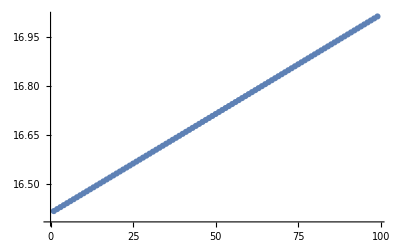

```mathematica
ListPlot[Hsqrt]
```

#### Self Convergence

```mathematica
LminusMInner=AL1[[;;,;;,;;,;;]]-AM1[[;;,;;;;2,;;;;2,;;]];
MminusHInner=AM1[[;;,;;;;2,;;;;2,;;]]-AH1[[;;,;;;;4,;;;;4,;;]];
```

```mathematica
LminusMOuter2=AL2[[;;,;;,;;,;;]]-AM2[[;;,;;;;2,;;;;2,;;]];
MminusHOuter2=AM2[[;;,;;;;2,;;;;2,;;]]-AH2[[;;,;;;;4,;;;;4,;;]];
```

```mathematica
LminusMOuter3=AL3[[;;,;;,;;,;;]]-AM3[[;;,;;;;2,;;;;2,;;]];
MminusHOuter3=AM3[[;;,;;;;2,;;;;2,;;]]-AH3[[;;,;;;;4,;;;;4,;;]];
```

```mathematica
LminusMOuter4=AL4[[;;,;;,;;,;;]]-AM4[[;;,;;;;2,;;;;2,;;]];
MminusHOuter4=AM4[[;;,;;;;2,;;;;2,;;]]-AH4[[;;,;;;;4,;;;;4,;;]];
```

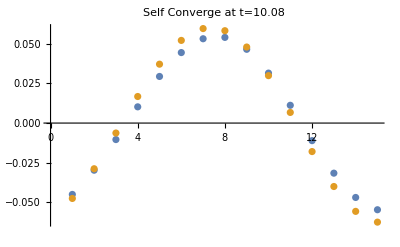

```mathematica
t=-1;
x=10;
y=1;
u=-1;
ListPlot[{4MminusHOuter2[[t,x,2;;,u]],LminusMOuter2[[t,x,;;-2,u]]},PlotLabel->"Self Converge at t="<>ToString[times[[t]]]]
```

```mathematica
Sum[1,{i,1,10}]
```

10

```mathematica
LMInnerTotal=Table[Sum[LminusMInner[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,1,uValues1//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
LMOutTotal=Table[Sum[LminusMOuter2[[ti,x,y,u]]^2+LminusMOuter3[[ti,x,y,u]]^2+LminusMOuter4[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,1,uValues2//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
```

```mathematica
MHInnerTotal=Table[Sum[MminusHInner[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,1,uValues1//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
MHOutTotal=Table[Sum[MminusHOuter2[[ti,x,y,u]]^2+MminusHOuter3[[ti,x,y,u]]^2+MminusHOuter4[[ti,x,y,u]]^2,{x,xValues//Length},{y,yValues//Length},{u,1,uValues2//Length}],{ti,1,AL[[;;, 1, 1, 1]]//Length}];
```

```mathematica
LMsqrt=Table[Sqrt[LMInnerTotal[[ti]]+LMOutTotal[[ti]]],{ti,1,LMOutTotal//Length}];
MHsqrt=Table[Sqrt[MHInnerTotal[[ti]]+MHOutTotal[[ti]]],{ti,1,MHOutTotal//Length}];
```

```mathematica
Table[dt  i,{i,0,end,each}]//Length
MHsqrt//Length
```

99

99

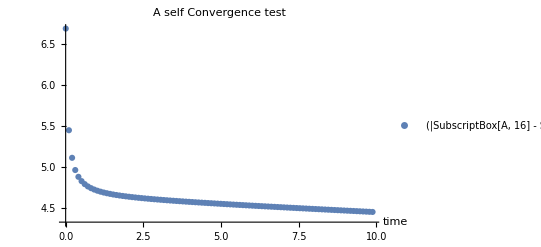

```mathematica
{Table[LMsqrt[[i]]/MHsqrt[[i]],{i,2,MHsqrt//Length}]}//ListPlot[{Transpose[{Table[dt  i,{i,1,end,each}],#[[1]]}](*,Transpose[{Range[0,dt end,dt each],#[[2]]}]}*)}(*,Joined->True*),PlotRange->All,GridLines->{{},{4}},AxesLabel->{"time"},PlotLabel->"A self Convergence test",PlotLegends->{"(| SubscriptBox[A, 16] - SubscriptBox[A, 32]SuperscriptBox[|, FractionBox[1, 2]])/(| SubscriptBox[A, 32] - SubscriptBox[A, 64]SuperscriptBox[|, FractionBox[1, 2]])"(*,"(| SubscriptBox[ξ, 32] - SubscriptBox[ξ, exact]SuperscriptBox[|, FractionBox[1, 2]])/(| SubscriptBox[ξ, 64] - SubscriptBox[ξ, exact]SuperscriptBox[|, FractionBox[1, 2]])"*)}]&
```

```mathematica
LMsqrt[[-1]]/MHsqrt[[-1]]
```

4.43967

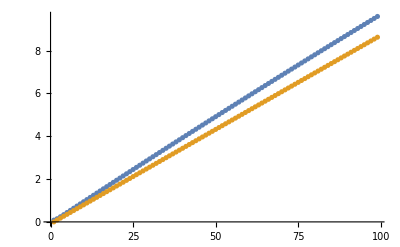

```mathematica
{LMsqrt,4MHsqrt}//ListPlot
```

#### Power Spectra Of The Velocity

```mathematica
ClearAll[t];
fux=Table[Fourier[ux[[t]],FourierParameters->{1,-1}],{t,nt}];
fuy=Table[Fourier[uy[[t]],FourierParameters->{1,-1}],{t,nt}];
```

```mathematica
nt
```

84

```mathematica
power=Table[Abs[fux[[t]]]^2+Abs[fuy[[t]]]^2,{t,nt}];
```

```mathematica
power//Dimensions
```

{115,50,50}

```mathematica
Clear[RadialPowerSpectrum]
RadialPowerSpectrum[ps_,Lx_?NumericQ,Ly_?NumericQ,dk_:Automatic]:=Module[{nx,ny,dkx,dky,dkBin,kx,ky,kxgrid,kygrid,kgrid,binIdxGrid,flat,groups,means,maxBin,kVals,meanVals},{nx,ny}=Dimensions[ps];
dkx=1.0/Lx;dky=1.0/Ly;
dkBin=If[dk===Automatic,Max[dkx,dky],dk];
(*build centered frequency coordinates*)
kx=If[EvenQ[nx],Join[Range[0,nx/2-1],Range[-nx/2,-1]]*dkx,Join[Range[0,Floor[nx/2]],Range[-Floor[nx/2],-1]]*dkx];
ky=If[EvenQ[ny],Join[Range[0,ny/2-1],Range[-ny/2,-1]]*dky,Join[Range[0,Floor[ny/2]],Range[-Floor[ny/2],-1]]*dky];
(*grids and radial wavenumber*)
kxgrid=Table[kx[[i]],{i,nx},{j,ny}];
kygrid=Table[ky[[j]],{i,nx},{j,ny}];
kgrid=Sqrt[kxgrid^2+kygrid^2];
(*assign integer bin indices*)
binIdxGrid=Floor[kgrid/dkBin];
flat=Transpose[{Flatten[binIdxGrid],Flatten[ps]}];
(*group by integer bin index—THIS is the correct form*)
groups=GroupBy[flat,First->Last];
means=Mean/@groups;
(*construct uniform bin centers and fill missing bins*)
maxBin=Max[Keys[means]];
meanVals=Table[Lookup[means,i,0.],{i,0,maxBin}];
kVals=(Range[0,maxBin]+0.5)*dkBin;
{kVals,meanVals}]
```

```mathematica
AA=Table[RadialPowerSpectrum[power[[t]],Lx,Ly],{t,1,nt}];
```

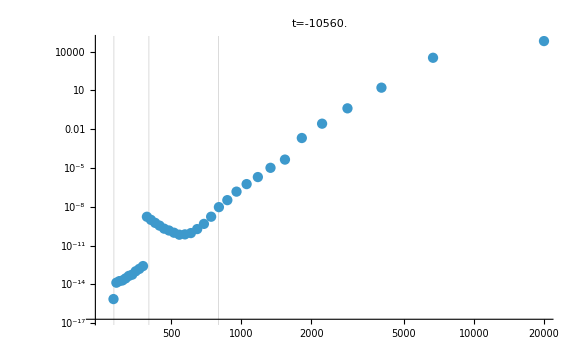

```mathematica
t=-1;
ListLogLogPlot[{Transpose[{AA[[t,1]]^-1,AA[[t,2]]}](*,Transpose[{BB[[t,1]]^-1,BB[[t,2]]}],Transpose[{CC[[t,1]]^-1,CC[[t,2]]}]*)},FrameLabel->{"Spatial scale (same units as Lx,Ly)","P(k)"},PlotRange->All,GridLines->{{0.5 Ly/(2 Pi),(*(4(200)^2)^(1/2),(2(200)^2)^(1/2),*)(2 2(xValues[[-1]]-xValues[[-2]])^2)^(1/2),(2(xValues[[-1]]-xValues[[-2]])^2)^(1/2)},{}},PlotLabel->"t="<>ToString[t dt each+init dt],ImageSize->Large]
```

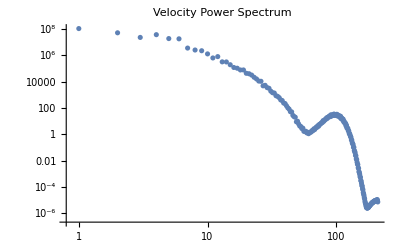

```mathematica
PkList=Values@Pk[[-1]];
kvals=Range[0,Length[PkList]-1];
ListLogLogPlot[Transpose[{kvals,Values[Pk[[-1]]]}],PlotLabel->"Velocity Power Spectrum",FrameLabel->{"k [1/length]","Power"},PlotRange->All]
```

```mathematica
Pk[[1]]//Dimensions
kvals//Dimensions
```

{70}

{70}

```mathematica
Export["/home/giulio/Pictures/gaussian.jpeg",%]
```

/home/giulio/Pictures/gaussian.jpeg

Power::infy: Infinite expression 1/0^5 encountered.

Set::write: Tag Table in Table[Transpose[{kvals,Values[Pk⟦t⟧]}],{t,1,Length[Pk]}] is Protected.

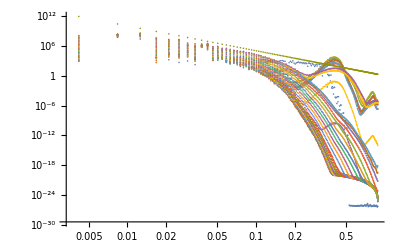

```mathematica
kvals=(2 Pi Range[0,Length[Pk[[1]]]-1])/1500;
ListLogLogPlot[AppendTo[Table[Transpose[{kvals,Values[Pk[[t]]]}],{t,1,Pk//Length}],Transpose[{kvals,kvals^-5}]]]
```

Set::write: Tag Table in Table[Transpose[{kvals,Values[Pk⟦t⟧]}],{t,1,Length[Pk]}] is Protected.

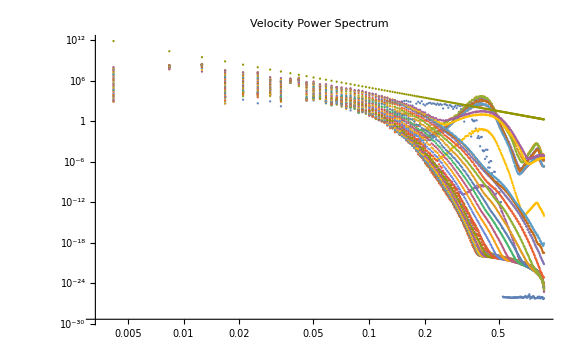

```mathematica
L=1500;
kvals=(2 Pi Range[0,Length[Pk[[1]]]-1])/L;
ListLogLogPlot[AppendTo[Table[Transpose[{kvals,Values[Pk[[t]]]}],{t,1,Pk//Length}],Transpose[{kvals[[2;;]],kvals[[2;;]]^-5}]],PlotLabel->"Velocity Power Spectrum",FrameLabel->{"k [1/length]","Power"},PlotRange->All,ImageSize->Large]
```

```mathematica
ClearAll[ss];
framesPowerSpectra=Table[ListLogLogPlot[{Transpose[{kvals,Values[Pk[[ss]]]}],Transpose[{kvals[[2;;]],kvals[[2;;]]^-5}]},PlotLabel->Style[" t="<>ToString[(ss-1) dt each+init dt],20],AxesLabel->{Style["k ",15],Style["P",15]},PlotRange->All,ImageSize->Large,Joined->True,PlotLegends->{None,"k^(-5/3)"},PlotStyle->{{Magenta,Thick},(*first line:red and thick*){Purple,Dashed,Thick}  (*second line:blue,thick and dashed*)},LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16}],{ss,1,nt}];
```

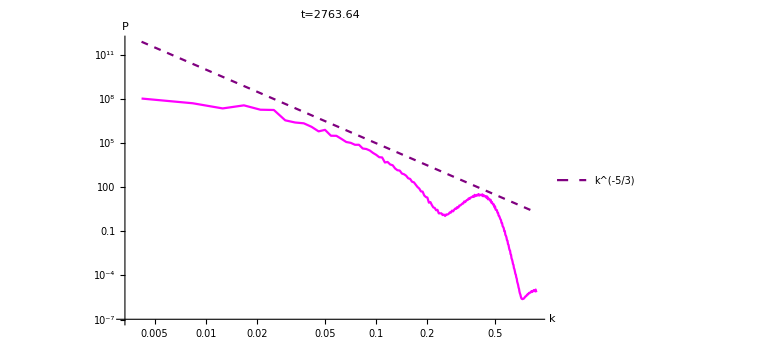

```mathematica
framesPowerSpectra[[-1]]
```

```mathematica
Export["/home/giulio/Pictures/power_spectra_unsourced.jpeg",%]
```

/home/giulio/Pictures/power_spectra_unsourced.jpeg

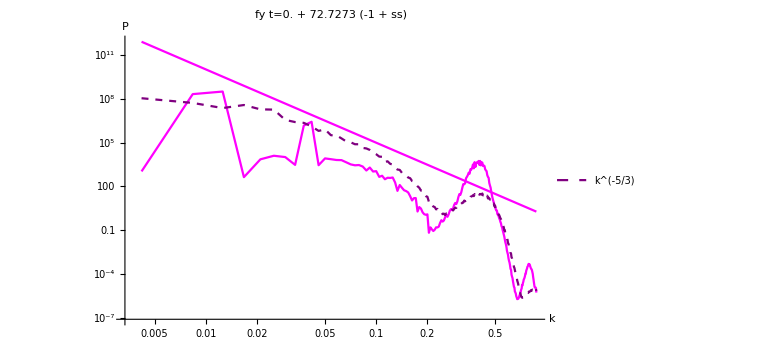

```mathematica
ListLogLogPlot[{Transpose[{kvals,Values[Pk[[2]]]}],Transpose[{kvals,Values[Pk[[-1]]]}],Transpose[{kvals[[2;;]],kvals[[2;;]]^-5}]},PlotLabel->Style["fy t="<>ToString[(ss-1) dt each+init dt],20],AxesLabel->{Style["k ",15],Style["P",15]},PlotRange->All,ImageSize->Large,Joined->True,PlotLegends->{None,"k^(-5/3)"},PlotStyle->{{Magenta,Thick},(*first line:red and thick*){Purple,Dashed,Thick}  (*second line:blue,thick and dashed*)},LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16}]
```

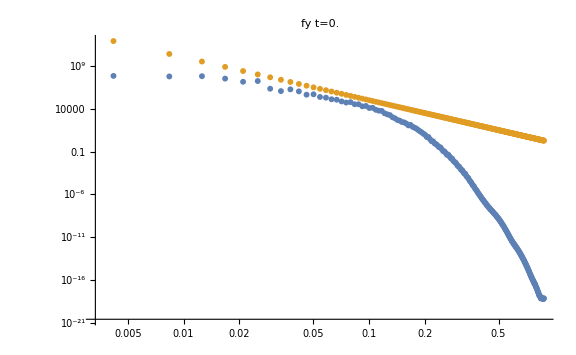

-Graphics-

```mathematica
Export["/home/giulio/Videos/powerspectr.mp4",framesPowerSpectra,"DisplayDurations"->0.4];
```

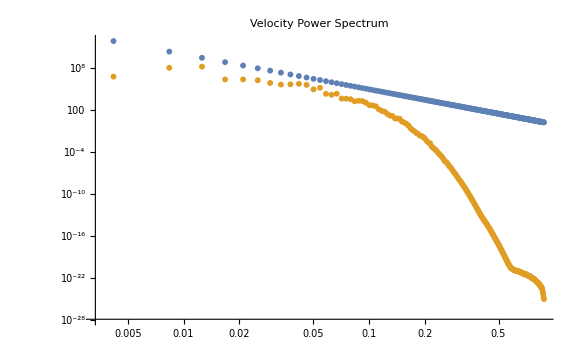

-Graphics-

#### Power spectra of the vorticity

```mathematica
t=-1;
Vorticity=Flatten[ParallelTable[{xValues[[i]],yValues[[j]],(d[1,0][uy[[t]]]-d[0,1][ux[[t]]])[[i,j]]},{i,1,xValues//Length,2
},{j,1,yValues//Length,2}],1];//AbsoluteTiming
```

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{2.66729×10^-13,0.0000673879,0.000134721,0.000201947,0.000269025,0.000335923,0.000402623,0.000469119,0.000535414,0.000601518,«90»},{2.11367×10^-13,0.0000600425,0.000120012,0.00017984,0.000239466,0.000298844,0.000357938,0.000416729,0.000475209,0.000533376,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{0.102096,0.102092,0.102081,0.102063,0.102037,0.102004,0.101963,0.101915,0.10186,0.101797,«90»},{0.102036,0.102032,0.102021,0.102002,0.101976,0.101943,0.101902,0.101854,0.101798,0.101734,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{2.66729×10^-13,0.0000673879,0.000134721,0.000201947,0.000269025,0.000335923,0.000402623,0.000469119,0.000535414,0.000601518,«90»},{2.11367×10^-13,0.0000600425,0.000120012,0.00017984,0.000239466,0.000298844,0.000357938,0.000416729,0.000475209,0.000533376,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

Part::partw: Part 11 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 21 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 31 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 41 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 51 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 61 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 71 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 81 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 91 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

General::stop: Further output of NDSolve`FiniteDifferenceDerivativeFunction::ddim will be suppressed during this calculation.

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{2.66729×10^-13,0.0000673879,0.000134721,0.000201947,0.000269025,0.000335923,0.000402623,0.000469119,0.000535414,0.000601518,«90»},{2.11367×10^-13,0.0000600425,0.000120012,0.00017984,0.000239466,0.000298844,0.000357938,0.000416729,0.000475209,0.000533376,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

Part::partw: Part 3 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{{«20»,«9»,«90»},«9»,«90»}] does not exist.

General::stop: Further output of NDSolve`FiniteDifferenceDerivativeFunction::ddim will be suppressed during this calculation.

Part::partw: Part 5 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{{«20»,«9»,«90»},«9»,«90»}] does not exist.

Part::partw: Part 11 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 21 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 31 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 41 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 51 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 61 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 71 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 81 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 91 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 7 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{{«20»,«9»,«90»},«9»,«90»}] does not exist.

Part::partw: Part 11 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 21 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 31 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 41 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 51 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 61 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 71 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 81 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 91 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{2.66729×10^-13,0.0000673879,0.000134721,0.000201947,0.000269025,0.000335923,0.000402623,0.000469119,0.000535414,0.000601518,«90»},{2.11367×10^-13,0.0000600425,0.000120012,0.00017984,0.000239466,0.000298844,0.000357938,0.000416729,0.000475209,0.000533376,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{0.102096,0.102092,0.102081,0.102063,0.102037,0.102004,0.101963,0.101915,0.10186,0.101797,«90»},{0.102036,0.102032,0.102021,0.102002,0.101976,0.101943,0.101902,0.101854,0.101798,0.101734,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

Part::partw: Part 101 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 111 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 121 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 131 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 141 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 151 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 161 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 171 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 181 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 191 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{2.66729×10^-13,0.0000673879,0.000134721,0.000201947,0.000269025,0.000335923,0.000402623,0.000469119,0.000535414,0.000601518,«90»},{2.11367×10^-13,0.0000600425,0.000120012,0.00017984,0.000239466,0.000298844,0.000357938,0.000416729,0.000475209,0.000533376,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

General::stop: Further output of NDSolve`FiniteDifferenceDerivativeFunction::ddim will be suppressed during this calculation.

Part::partw: Part 101 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 111 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 121 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 131 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 141 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 151 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 161 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 171 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 181 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 191 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 101 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 111 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 121 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 131 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 141 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 151 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 161 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 171 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 181 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 191 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{2.66729×10^-13,0.0000673879,0.000134721,0.000201947,0.000269025,0.000335923,0.000402623,0.000469119,0.000535414,0.000601518,«90»},{2.11367×10^-13,0.0000600425,0.000120012,0.00017984,0.000239466,0.000298844,0.000357938,0.000416729,0.000475209,0.000533376,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{0.102096,0.102092,0.102081,0.102063,0.102037,0.102004,0.101963,0.101915,0.10186,0.101797,«90»},{0.102036,0.102032,0.102021,0.102002,0.101976,0.101943,0.101902,0.101854,0.101798,0.101734,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

Part::partw: Part 201 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 211 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 221 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 231 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 241 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 251 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 261 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 271 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 281 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 291 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

NDSolve`FiniteDifferenceDerivativeFunction::ddim: Data {{2.66729×10^-13,0.0000673879,0.000134721,0.000201947,0.000269025,0.000335923,0.000402623,0.000469119,0.000535414,0.000601518,«90»},{2.11367×10^-13,0.0000600425,0.000120012,0.00017984,0.000239466,0.000298844,0.000357938,0.000416729,0.000475209,0.000533376,«90»},«8»,«90»} is not a rectangular tensor with dimensions {300,299}.

General::stop: Further output of NDSolve`FiniteDifferenceDerivativeFunction::ddim will be suppressed during this calculation.

Part::partw: Part 201 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 211 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 221 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 231 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 241 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 251 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 261 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 271 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 281 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 291 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 201 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 211 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 221 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 231 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 241 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 251 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 261 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 271 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 281 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

Part::partw: Part 291 of -NDSolve`FiniteDifferenceDerivativeFunction[Derivative[0,1],5,{299,PSFourier[{0.+0. ⅈ,0.-0.0000140562 ⅈ,0.-0.0000281124 ⅈ,0.-0.0000421686 ⅈ,0.-0.0000562247 ⅈ,0.-0.0000702809 ⅈ,0.-0.0000843371 ⅈ,0.-0.0000983933 ⅈ,0.-0.000112449 ⅈ,0.-0.000126506 ⅈ,«289»}]},{{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»},{-750.,-745.,-740.,-735.,-730.,-725.,-720.,-715.,-710.,-705.,«290»}},{True,True}][{«1»}]+«42»[«1»][{«1»}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
ListContourPlot[Vorticity]
```

-Graphics-

```mathematica
6.6/20 0.8//N
```

0.264

```mathematica
{xvals,yvals,vortVals}=Transpose[Vorticity];
```

```mathematica
interpFunc=ListInterpolation[Partition[vortVals,Sqrt[Length[vortVals]]],{Sort@DeleteDuplicates[xvals],Sort@DeleteDuplicates[yvals]},InterpolationOrder->1];
```

```mathematica
nx=ny=300;
xRange={Min[xvals],Max[xvals]};
yRange={Min[yvals],Max[yvals]};

xgrid=Subdivide@@Join[xRange,{nx-1}];
ygrid=Subdivide@@Join[yRange,{ny-1}];

vortGrid=Table[interpFunc[x,y],{y,ygrid},{x,xgrid}];
```

```mathematica
ListContourPlot[vortGrid]
```

-Graphics-

```mathematica
fft=Fourier[vortGrid,FourierParameters->{1,-1}];
powerSpectrum2D=Abs[fft]^2;
```

```mathematica
radialAverage[ps_]:=Module[{dims,cx,cy,rgrid,flat,bins},dims=Dimensions[ps];
{cx,cy}=(dims+1)/2;
rgrid=Round@MapIndexed[EuclideanDistance[{#2[[2]],#2[[1]]},{cx,cy}]&,ps,{2}];
flat=Transpose[{Flatten[rgrid],Flatten[ps]}];(*FIXED*)bins=GroupBy[flat,First->Last];
Mean/@bins];
```

```mathematica
Pk=radialAverage[powerSpectrum2D];
```

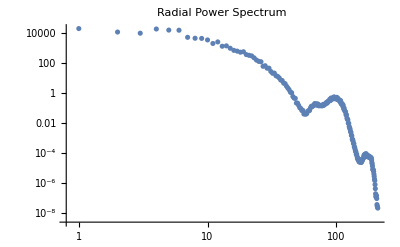

```mathematica
PkList=Values@Pk;
kvals=Range[0,Length[PkList]-1];
ListLogLogPlot[Transpose[{kvals,PkList}],PlotLabel->"Radial Power Spectrum",FrameLabel->{"k (bin index)","Power"},PlotRange->All]
```

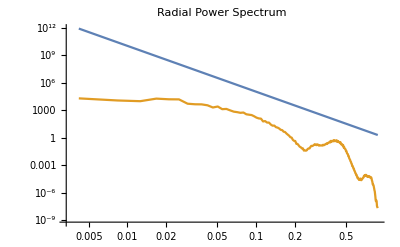

```mathematica
L=1500;
kvals=(2 Pi Range[0,Length[PkList]-1])/L;
ListLogLogPlot[{Transpose[{kvals[[2;;]],kvals[[2;;]]^-5}],Transpose[{kvals,PkList}]},PlotLabel->"Radial Power Spectrum",FrameLabel->{"k [1/length]","Power"},Joined->True(*,PlotRange->{{0.0006,0.2},All}*)]
```

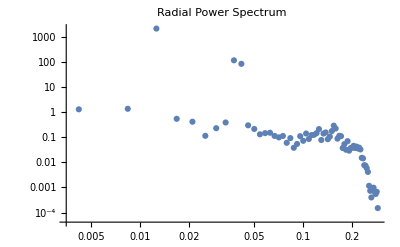

```mathematica
1/300//N
```

0.00333333

#### Fit and Checkpoint Recover

```mathematica
init=188858;
end=188858;
each=1;
gaugeFNames=Table[StringJoin["gauge_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
gaugeName1=Table[StringJoin["/home/giulio/University/PhD/Simulations/FullBBB_4D_300_q10_A1_L1500_ui20_1u12/FullBBB_3p1_300_q10_Amp1_L1500_ui8_1u12_Nfcxy0_rec7_All/FullBBB_3p1_300_q10_Amp1_L1500_ui8_1u12_Nfcxy0_rec7/",
gaugeFNames[[i]],".h5"],{i,gaugeFNames//Length}];
Timing[gauge=Table[Import[gaugeName1[[i]],"Data"](*[[1]]*),{i,1,gaugeName1//Length}]];//AbsoluteTiming
gauge=gauge[[1,1]];

bulkFNames=Table[StringJoin["bulk_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
bulkName1=Table[StringJoin["/home/giulio/University/PhD/Simulations/FullBBB_3p1_300_q10_Amp1_L1500_ui8_1u12_Nfcxy0_rec7_new/",
bulkFNames[[i]],".h5"],{i,bulkFNames//Length}];
Timing[bulk=Table[Import[bulkName1[[i]],"Data"](*[[1]]*),{i,1,bulkName1//Length}]];//AbsoluteTiming

boundaryFNames=Table[StringJoin["boundary_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
boundaryName1=Table[StringJoin["/home/giulio/University/PhD/Simulations/FullBBB_3p1_300_q10_Amp1_L1500_ui8_1u12_Nfcxy0_rec7_new/",
boundaryFNames[[i]],".h5"],{i,bulkFNames//Length}];
Timing[boundary=Table[Import[boundaryName1[[i]],"Data"](*[[1]]*),{i,1,bulkName1//Length}]];//AbsoluteTiming



gaugeFNames//Length
dt=Import[gaugeName1[[1]],"Attributes"][[3,1]];
times=Table[tim dt each+init dt,{tim,1,gauge//Length}];
nt=times//Length;
Print["dt = "<>ToString[dt]]
Print["final time = "<>ToString[Import[gaugeName1[[-1]],"Attributes"][[3,2]]//FullForm]]
```

{0.020075,Null}

{0.022911,Null}

{0.0138,Null}

1

dt = 0.0145455

final time = 2747.0254545438215`

```mathematica
2/3 2/3//N
```

0.444444

```mathematica
bulk//Keys
gauge//Keys
boundary//Keys
```

{{/data/188858/fields/B c=2,/data/188858/fields/G c=1,/data/188858/fields/B c=1,/data/188858/fields/G c=2}}

{{/data/188858/fields/xi}}

{{/data/188858/fields/fy1,/data/188858/fields/fx1,/data/188858/fields/b13,/data/188858/fields/a3,/data/188858/fields/g3}}

```mathematica
gauge[[1,40]]
```

{0.124929}

```mathematica
InterpolatedGauge=Interpolation[Flatten[Table[{{xValues[[i]],yValues[[j]]},gauge[[i,j,1]]},{i,1,xValues//Length},{j,1,yValues//Length}],1]];
```

```mathematica
Total[Table[gauge[[i,j,1]]-InterpolatedGauge[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}]//Flatten]
```

7.58942×10^-19

```mathematica
(*Interpolateda3=Interpolation[Flatten[Table[{{xValues[[i]],yValues[[j]]},boundary[[1,4,i,j,1]]},{i,1,xValues//Length},{j,1,yValues//Length}],1]];
Interpolatedfx=Interpolation[Flatten[Table[{{xValues[[i]],yValues[[j]]},boundary[[1,2,i,j,1]]},{i,1,xValues//Length},{j,1,yValues//Length}],1]];
Interpolatedfy=Interpolation[Flatten[Table[{{xValues[[i]],yValues[[j]]},boundary[[1,1,i,j,1]]},{i,1,xValues//Length},{j,1,yValues//Length}],1]];*)
Interpolatedguess=Interpolation[Flatten[Table[{{xValues[[i]],yValues[[j]]},uValues2[[rMaxindices[[i,j,1]]]]},{i,1,xValues//Length},{j,1,yValues//Length}],1]];
```

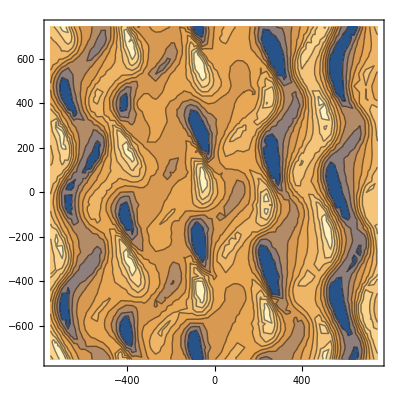

```mathematica
(*ContourPlot[Interpolatedfx[x,y],{x,xValues[[1]],xValues[[-1]]},{y,yValues[[1]],yValues[[-1]]}]*)
```

```mathematica
InterpolatedB1=Table[Interpolation[Flatten[Table[{{xValues[[i]],yValues[[j]]},bulk[[1,3,i,j,r]]},{i,1,xValues//Length},{j,1,yValues//Length}],1]],{r,1,bulk[[1,3,1,1]]//Length}];
InterpolatedG1=Table[Interpolation[Flatten[Table[{{xValues[[i]],yValues[[j]]},bulk[[1,2,i,j,r]]},{i,1,xValues//Length},{j,1,yValues//Length}],1]],{r,1,bulk[[1,2,1,1]]//Length}];

InterpolatedB2=Table[Interpolation[Flatten[Table[{{xValues[[i]],yValues[[j]]},bulk[[1,1,i,j,r]]},{i,1,xValues//Length},{j,1,yValues//Length}],1]],{r,1,bulk[[1,1,1,1]]//Length}];
InterpolatedG2=Table[Interpolation[Flatten[Table[{{xValues[[i]],yValues[[j]]},bulk[[1,4,i,j,r]]},{i,1,xValues//Length},{j,1,yValues//Length}],1]],{r,1,bulk[[1,4,1,1]]//Length}];
```

```mathematica
InterpolatedB=Join[{InterpolatedB1,InterpolatedB2}];
InterpolatedG=Join[{InterpolatedG1,InterpolatedG2}];
```

```mathematica
InterpolatedB//Dimensions
```

{2}

```mathematica
bulk[[1,3,1,1]]//Length
```

20

```mathematica
InterpolatedB1//Dimensions
```

{20}

```mathematica
ay=Abs[Import[Name1[[1]],"Attributes"][[5,3,1]]];
by=-Abs[Import[Name1[[1]],"Attributes"][[5,3,1]]];
Ly=ay-by;
ax=Abs[Import[Name1[[1]],"Attributes"][[5,3,2]]];
bx=-Abs[Import[Name1[[1]],"Attributes"][[5,3,2]]];
Lx=ax-bx;
NPoints2=400;
```

```mathematica
xValues2=Range[bx,ax,(ax 2)/NPoints2][[1;;-2]];
yValues2=Range[by,ay,(ay 2)/NPoints2][[1;;-2]];
```

```mathematica
IDFolderName="/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN400q10/"
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN400q10/

```mathematica
a3Data=Table[(Interpolateda3[x,y]/.x->xValues2[[i]]/.y->yValues2[[j]])(*+a3Pert[[i,j]]*),{i,1,xValues2//Length},{j,1,yValues2//Length}];
a3AttributesAndData={"a3"->a3Data};
```

```mathematica
xiData=Table[(InterpolatedGauge[x,y](*/.ξ[t,x,y]->0*)(*1-Hypergeometric2F1[-0.3333333333333333,0.5,0.6666666666666666,-1/2-1/2 Cos[(2223497 y)/5898008975]]*)/.x->xValues2[[i]]/.y->yValues2[[j]])(*(1+(RandomReal[]-0.5)/100)*),{i,1,xValues2//Length},{j,1,yValues2//Length}];
```

InterpolatingFunction::dmval: Input value {-750.,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-746.25,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-742.5,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
guessData=Table[(Interpolatedguess[x,y]/.x->xValues2[[i]]/.y->yValues2[[j]]),{i,1,xValues2//Length},{j,1,yValues2//Length}];
```

InterpolatingFunction::dmval: Input value {-750.,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-746.25,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-742.5,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Max[guessData]
```

1.03696

```mathematica
xiAttributesAndData={"xi"->xiData};
```

```mathematica
guessAttributesAndData={"guess"->guessData};
```

```mathematica
(*Export[IDFolderName<>"Initialxi_BBB.h5",xiAttributesAndData,"Datasets"]*)
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN400q10/Initialxi_BBB.h5

```mathematica
Export[IDFolderName<>"Initialguess_BBB.h5",guessAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN400q10/Initialguess_BBB.h5

```mathematica
(*Export[IDFolderName<>"Initiala3_BBB.h5",a3AttributesAndData,"Datasets"]*)
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN400q10/Initiala3_BBB.h5

Fx

```mathematica
fxData=Table[Interpolatedfx[x,y]/.x->xValues2[[i]]/.y->yValues2[[j]],{i,1,xValues2//Length},{j,1,yValues2//Length}];
```

InterpolatingFunction::dmval: Input value {-750.,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-746.25,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-742.5,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
fxAttributesAndData={"fx"->fxData};
```

```mathematica
Export[IDFolderName<>"Initialfx_BBB.h5",fxAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN400q10/Initialfx_BBB.h5

Fy

```mathematica
fyData=Table[Interpolatedfx[z,y]/.x->xValues2[[i]]/.y->yValues2[[j]],{i,1,xValues2//Length},{j,1,yValues2//Length}];
```

```mathematica
fyAttributesAndData={"fy"->fyData};
```

```mathematica
Export[IDFolderName<>"Initialfy_BBB.h5",fyAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN300q10Initialfy_BBB.h5

B

```mathematica
InitialB=Table[InterpolatedB[[n,ui]][xValues2[[xi]],yValues2[[yi]]](*(1+(RandomReal[]-0.5)/10^4)*),{n,1,InterpolatedB//Length},{ui,1,InterpolatedB[[n]]//Length},{xi,1,xValues2//Length},{yi,1,yValues2//Length}];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {-750.,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-746.25,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-742.5,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{31.6777,Null}

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndData=Table[ExportAttributes[[i]]->InitialB[[i]],{i,1,ExportAttributes//Length}];//AbsoluteTiming
```

{0.000013,Null}

```mathematica
Export[IDFolderName<>"InitialB_BBB.h5",AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN400q10/InitialB_BBB.h5

G

```mathematica
InitialG=Table[InterpolatedG[[n,ui]][xValues2[[xi]],yValues2[[yi]]](*(1+(RandomReal[]-0.5)/10^4)*),{n,1,InterpolatedG//Length},{ui,1,InterpolatedG[[n]]//Length},{xi,1,xValues2//Length},{yi,1,yValues2//Length}];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {-750.,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-746.25,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-742.5,746.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{25.9862,Null}

```mathematica
AttributesAndDataG=Table[ExportAttributes[[i]]->InitialG[[i]],{i,1,ExportAttributes//Length}];//AbsoluteTiming
```

{0.000017,Null}

```mathematica
Export[IDFolderName<>"InitialG_BBB.h5",AttributesAndDataG,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/UnsN400q10/InitialG_BBB.h5

#### Flattening ux

```mathematica
ux[[-1,20;;,;;]]//Dimensions
```

{31,50}

90

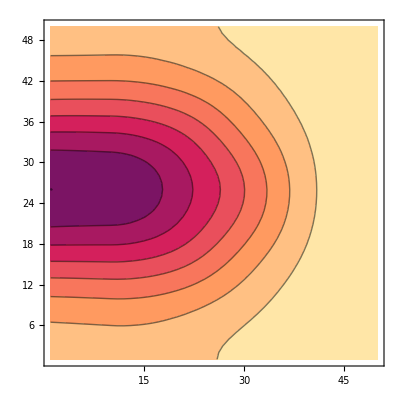

```mathematica
tt=90
Nx=Length[ux[[1]]];
Ny=Length[ux[[1,1]]];
uext=0.2;
δ=40;
w=Join[ConstantArray[1,Nx-δ],Table[0.5 (1+Cos[Pi*(i-(Nx-δ))/δ]),{i,Nx-δ+1,Nx}]];
uxExtended=Table[w[[i]] ux[[tt,i,j]]+(1-w[[i]]) uext,{i,1,Nx},{j,1,Ny}];
ListContourPlot[uxExtended//Transpose,Mesh->None,PlotRange->All]
```

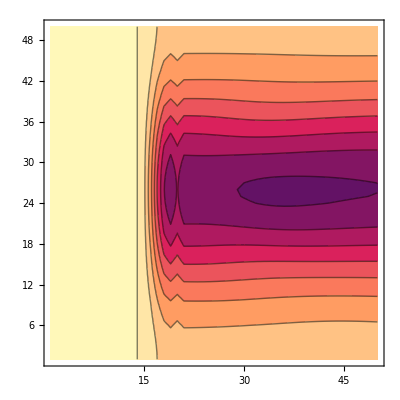

```mathematica
iFlat=20;  (*start flattening before this index*)
δ=5;       (*smoothing width*)
uext=0.20;    (*target value on the far left*)
w=Join[ConstantArray[0,iFlat-δ-1],Table[0.5 (1-Cos[Pi*(i-(iFlat-δ-1))/δ]),{i,iFlat-δ,iFlat}],ConstantArray[1,Nx-iFlat]];
uxFlattened=Table[w[[i]] ux[[tt,i,j]]+(1-w[[i]]) uext,{i,1,Nx},{j,1,Ny}];
ListContourPlot[uxFlattened//Transpose,Mesh->None,PlotRange->All]
```

```mathematica
NewxValues=Table[xValues[[-1]]+i dx,{i,1,uxFlattened//Length}];
```

```mathematica
JoinedToPlot=Flatten[Join[Table[{xValues[[i]],yValues[[j]],uxFlattened[[i,j]]},{i,1,xValues//Length},{j,1,yValues//Length}],Table[{NewxValues[[i]],yValues[[j]],uxExtended[[i,j]]},{i,1,NewxValues//Length},{j,1,yValues//Length}],1],1];
```

```mathematica
JoinedToPlot//Dimensions
```

{5000,3}

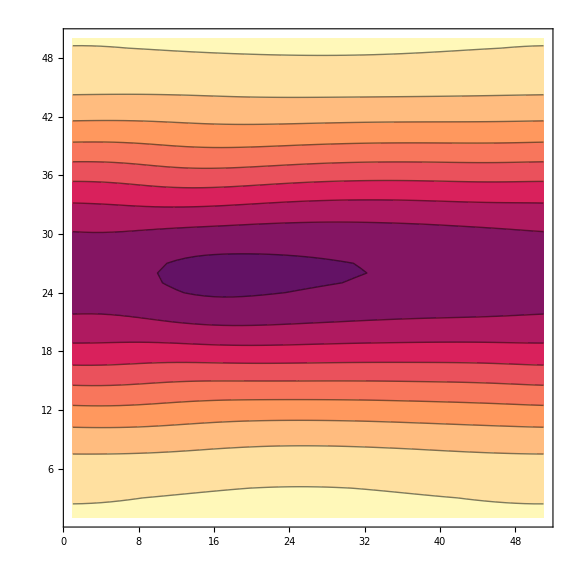

```mathematica
ListContourPlot[Join[ux[[tt,20;;]],ux[[tt,;;20]]]//Transpose,ImageSize->Large]
```

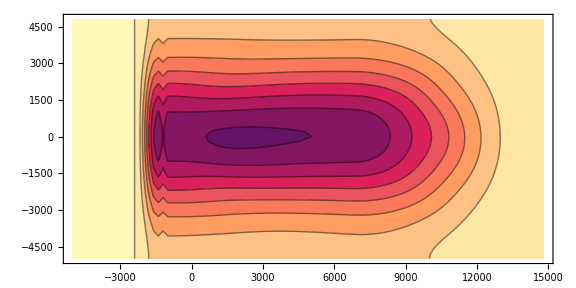

```mathematica
ListContourPlot[JoinedToPlot,AspectRatio->1/2,ImageSize->Large]
```

#### Alltogether Flattening

```mathematica
ux//Length
```

113

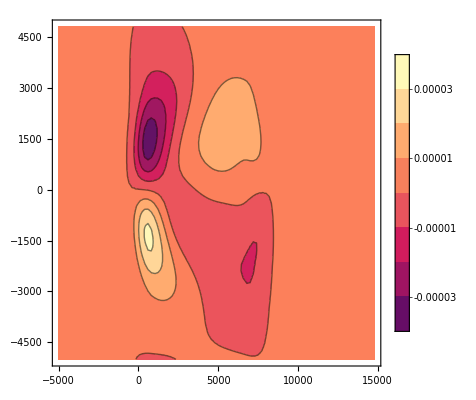

```mathematica
(* ===Parameters===*)tt=90;
xcutLeft=20;    (*right edge of left constant region*)
xcutRight=20;   (*left edge of right constant region*)
δ=10;            (*transition width*)

Nx=Length[ux[[1]]];
Ny=Length[ux[[1,1]]];
dx=xValues[[2]]-xValues[[1]];  (*assuming uniform grid spacing*)

(* ===Helper:build taper functions===*)
wLeft=Table[Which[i<=xcutLeft,0,i>=xcutLeft+δ,1,True,0.5 (1-Cos[Pi*(i-xcutLeft)/δ])],{i,1,Nx}];

wRight=Table[Which[i<=xcutRight-δ,1,i>=xcutRight,0,True,0.5 (1+Cos[Pi*(i-(xcutRight-δ))/δ])],{i,1,Nx}];

(* ===Helper:flatten a field using a given taper and plateau value===*)
flatten2D[field_,w_,uext_]:=Table[w[[i]] field[[tt,i,j]]+(1-w[[i]]) uext,{i,1,Nx},{j,1,Ny}];

(* ===Fields to process===*)
fields={a3,fx,fy};

(* ===Compute plateau values for each field from first element===*)
plateauValues=Association[Table[f->f[[tt,1,1]],{f,fields}]];

(* ===Flatten left and right for each field===*)
flattenedLeft=Association[Table[f->flatten2D[f,wLeft,plateauValues[f]],{f,fields}]];
flattenedRight=Association[Table[f->flatten2D[f,wRight,plateauValues[f]],{f,fields}]];

(* ===Extend xValues for the right-flattened part===*)
NewxValues=Table[xValues[[-1]]+i dx,{i,1,Nx}];

(* ===Join left and right flattened fields into {x,y,value} triples for plotting===*)
joinedFields=Association[];
Do[joinedFields[f]=Flatten[Join[Table[{xValues[[i]],yValues[[j]],flattenedLeft[f][[i,j]]},{i,1,Nx},{j,1,Ny}],Table[{NewxValues[[i]],yValues[[j]],flattenedRight[f][[i,j]]},{i,1,Nx},{j,1,Ny}],1],1],{f,fields}];

(* ===Example:plot joined a3 field===*)
ListContourPlot[joinedFields[fy],PlotRange->All,PlotLegends->Automatic]
```

```mathematica
(* ===Parameters===*)tt=90;
xcutLeft=20;    (*right edge of left constant region*)
xcutRight=20;   (*left edge of right constant region*)
δ=10;            (*transition width*)

Nx=Length[ux[[1]]];
Ny=Length[ux[[1,1]]];
dx=xValues[[2]]-xValues[[1]];  (*assuming uniform grid spacing*)

(* ===Build taper functions===*)
wLeft=Table[Which[i<=xcutLeft,0,i>=xcutLeft+δ,1,True,0.5 (1-Cos[Pi*(i-xcutLeft)/δ])],{i,1,Nx}];

wRight=Table[Which[i<=xcutRight-δ,1,i>=xcutRight,0,True,0.5 (1+Cos[Pi*(i-(xcutRight-δ))/δ])],{i,1,Nx}];

(* ===Helper functions===*)

(*Flatten 2D field {t,x,y} at time tt*)
flatten2D[field_,w_,uext_]:=Table[w[[i]] field[[tt,i,j]]+(1-w[[i]]) uext,{i,1,Nx},{j,1,Ny}];

(*Flatten 3D field {t,r,x,y} at time tt for all r*)
flatten3D[field_,w_]:=Module[{Nr=Length[field[[1]]]},Table[Module[{uext=field[[tt,r,1,1]]},(*plateau value per radial index*)Table[w[[i]] field[[tt,r,i,j]]+(1-w[[i]]) uext,{i,1,Nx},{j,1,Ny}]],{r,1,Nr}]];

(* ===Fields to process===*)
fields2D={a3,fx,fy};
fields3D={B,G};

(* ===Compute plateau values for 2D fields===*)
plateauValues2D=Association[Table[f->f[[tt,1,1]],{f,fields2D}]];

(* ===Flatten left and right for 2D fields===*)
flattenedLeft2D=Association[Table[f->flatten2D[f,wLeft,plateauValues2D[f]],{f,fields2D}]];
flattenedRight2D=Association[Table[f->flatten2D[f,wRight,plateauValues2D[f]],{f,fields2D}]];

(* ===Flatten left and right for 3D fields===*)
flattenedLeft3D=Association[Table[f->flatten3D[f,wLeft],{f,fields3D}]];
flattenedRight3D=Association[Table[f->flatten3D[f,wRight],{f,fields3D}]];

(* ===Extend xValues for the right-flattened portion===*)
NewxValues=Table[xValues[[-1]]+i dx,{i,1,Nx}];

(* ===Join left and right flattened 2D fields for plotting===*)
joinedFields2D=Association[];
Do[joinedFields2D[f]=Flatten[Join[Table[{xValues[[i]],yValues[[j]],flattenedLeft2D[f][[i,j]]},{i,1,Nx},{j,1,Ny}],Table[{NewxValues[[i]],yValues[[j]],flattenedRight2D[f][[i,j]]},{i,1,Nx},{j,1,Ny}],1],1],{f,fields2D}];

(* ===Join left and right flattened 3D fields for plotting per r===*)
joinedFields3D=Association[];
Do[joinedFields3D[f]=Table[Flatten[Join[Table[{xValues[[i]],yValues[[j]],flattenedLeft3D[f][[r,i,j]]},{i,1,Nx},{j,1,Ny}],Table[{NewxValues[[i]],yValues[[j]],flattenedRight3D[f][[r,i,j]]},{i,1,Nx},{j,1,Ny}],1],1],{r,1,Length[flattenedLeft3D[f]]}],{f,fields3D}];

(* ===Example plotting===*)
ListPointPlot3D[joinedFields2D[a3],PlotStyle->PointSize[0.01]]    (*2D field*)
ListPointPlot3D[joinedFields3D[B][[1]],PlotStyle->PointSize[0.01]] (*3D field,r=1*)
```

Part::partd: Part specification B⟦1⟧ is longer than depth of object.

Part::partd: Part specification B⟦90,1,1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification B⟦1⟧ is longer than depth of object.

Part::partd: Part specification B⟦90,1,1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics3D-

-Graphics3D-

### Boundary

This section is not commented!
In this section I try to obtain the boundary stress energy tensor.
The cells below can take a lot of computational time.
I am also not sure if the procedure is 100% correct, since at the moment I use mainly the S function to check the results of the simulations.

#### a Spatial derivatives

```mathematica
a3Int=Table[Interpolation[Table[{xValues[[j]],yValues[[i]],a3[[t,i,j,1]]},{j,1,xValues//Length},{i,1,yValues//Length}]//Flatten[#,1]&],{t,1,a3//Length}];//AbsoluteTiming
```

Part::partd1: Depth of object {{-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,«182»},{-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,-1.375,«182»},«8»,«182»} is not sufficient for the given part specification.

General::stop: Further output of Part::partd1 will be suppressed during this calculation.

```mathematica
a3yy=Table[Table[D[a3Int[[t]][x,y],{y,2}]/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}],{t,1,Obj3//Length}];//AbsoluteTiming
```

$Aborted

```mathematica
a3xx=Table[Table[D[a3Int[[t]][x,y],{x,2}]/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}],{t,1,Obj3//Length}];//AbsoluteTiming
```

{2.41649,Null}

#### b Spatial Derivatives

```mathematica
b13Int=Table[Interpolation[Table[{xValues[[j]],yValues[[i]],b13[[t,i,j,1]]},{j,1,xValues//Length},{i,1,yValues//Length}]//Flatten[#,1]&],{t,1,Obj3//Length}];//AbsoluteTiming
```

{0.226059,Null}

```mathematica
b13xx=Table[Table[D[b13Int[[t]][x,y],{x,2}]/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}],{t,1,Obj3//Length}];//AbsoluteTiming
```

{2.37797,Null}

```mathematica
b13yy=Table[Table[D[b13Int[[t]][x,y],{y,2}]/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}],{t,1,Obj3//Length}];//AbsoluteTiming
```

{2.42476,Null}

#### fx Spatial Derivatives

```mathematica
fx1Int=Table[Interpolation[Table[{xValues[[j]],yValues[[i]],fx1[[t,i,j,1]]},{j,1,xValues//Length},{i,1,yValues//Length}]//Flatten[#,1]&],{t,1,Obj3//Length}];//AbsoluteTiming
```

{0.23636,Null}

```mathematica
fx1yy=Table[Table[D[fx1Int[[t]][x,y],{y,2}]/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}],{t,1,Obj3//Length}];//AbsoluteTiming
```

{2.41962,Null}

```mathematica
fx1xy=Table[Table[D[fx1Int[[t]][x,y],{x,1},{y,1}]/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}],{t,1,Obj3//Length}];//AbsoluteTiming
```

{3.42543,Null}

#### fy Spatial Derivatives

```mathematica
fy1Int=Table[Interpolation[Table[{xValues[[j]],yValues[[i]],fy1[[t,i,j,1]]},{j,1,xValues//Length},{i,1,yValues//Length}]//Flatten[#,1]&],{t,1,Obj3//Length}];//AbsoluteTiming
```

{0.255708,Null}

```mathematica
fy1xx=Table[Table[D[fy1Int[[t]][x,y],{x,2}]/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}],{t,1,Obj3//Length}];//AbsoluteTiming
```

{2.45007,Null}

```mathematica
fy1xy=Table[Table[D[fy1Int[[t]][x,y],{x,1},{y,1}]/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}],{t,1,Obj3//Length}];//AbsoluteTiming
```

{3.3756,Null}

#### g Spatial Derivatives

```mathematica
g3Int=Table[Interpolation[Table[{xValues[[j]],yValues[[i]],g3[[t,i,j,1]]},{j,1,xValues//Length},{i,1,yValues//Length}]//Flatten[#,1]&],{t,1,Obj3//Length}];//AbsoluteTiming
```

{0.219705,Null}

```mathematica
g3xy=Table[Table[D[g3Int[[t]][x,y],{x,1},{y,1}]/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}],{t,1,Obj3//Length}];//AbsoluteTiming
```

{4.2274,Null}

```mathematica
g3xy[[50,1,1]]
```

Part::partw: Part 50 of {{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«74»},«74»},«9»,«11»} does not exist.

#### Source

```mathematica
file="NBB_gaussian_Lx1500_Ly1500_0d55iu10_1u010_Nx50_Ny50_u0d05_tzero5000_tau2000_A0d8_s0d125_noise_boundary";
init=0;
end=250000;
each=50000;
(*FNamesBulk=Table[StringJoin["bulk_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
NamesBulk=Table[StringJoin["/home/giulio/University/PhD/Simulations/"<>file<>"/",
FNamesBulk[[i]],".h5"],{i,FNamesBulk//Length}];
FNamesConstrained=Table[StringJoin["constrained_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
NamesConstrained=Table[StringJoin["/home/giulio/University/PhD/Simulations/"<>file<>"/",
FNamesConstrained[[i]],".h5"],{i,FNamesConstrained//Length}];*)
FNamesBoundary=Table[StringJoin["boundary_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
NamesBoundary=Table[StringJoin["/home/giulio/University/PhD/Simulations/"<>file<>"/",
FNamesBoundary[[i]],".h5"],{i,FNamesBoundary//Length}];
dt=Import[NamesBoundary[[2]],"Attributes"][[3,1]];
times=Table[tim dt each+init dt,{tim,0,(FNamesBoundary//Length)-1}];
nt=times//Length;
Print["dt = "<>ToString[dt]]
Print["final time = "<>ToString[Import[NamesBoundary[[-1]],"Attributes"][[3,2]]//FullForm]]
snapshots=Table[(tim-1)  each+init ,{tim,1,times//Length}];
b3=Table[Import[NamesBoundary[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/b13"][[;;,;;,1]]//Transpose,{i,1,NamesBoundary//Length}];
g3=Table[Import[NamesBoundary[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/g3"][[;;,;;,1]]//Transpose,{i,1,NamesBoundary//Length}];
fx=Table[Import[NamesBoundary[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/fx1"][[;;,;;,1]]//Transpose,{i,1,NamesBoundary//Length}];
fy=Table[Import[NamesBoundary[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/fy1"][[;;,;;,1]]//Transpose,{i,1,NamesBoundary//Length}];
a3=Table[Import[NamesBoundary[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/a3"][[;;,;;,1]]//Transpose,{i,1,NamesBoundary//Length}];
(*Fxh=Table[Import[NamesConstrained[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/Fx c=2"][[;;,;;,-1]],{i,1,NamesBulk//Length}];
Fyh=Table[Import[NamesConstrained[[i]],"Data"]["/data/"<>ToString[snapshots[[i]]]<>"/fields/Fy c=2"][[;;,;;,-1]],{i,1,NamesBulk//Length}];*)
```

dt = 0.0244444

final time = 6111.111111085522`

```mathematica
u0=(a3//Abs)^(1/2);
ux=(*Table[(fx[[tt]]-d[1,0][a3[[tt]]])/a3[[tt]],{tt,1,a3//Length}]*)-fx u0;
uy=(*Table[(fy[[tt]]-d[0,1][a3[[tt]]])/a3[[tt]],{tt,1,a3//Length}]*)-fy u0;
```

```mathematica
times//Length
```

6

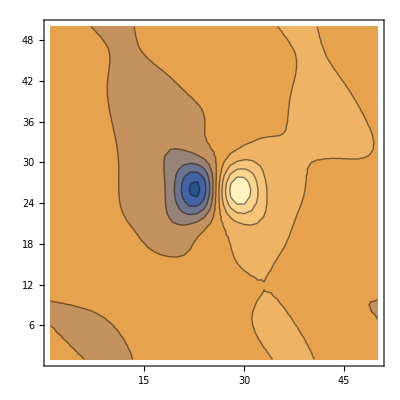

```mathematica
ListContourPlot[ux[[4]]//Transpose,PlotRange->All]
```

```mathematica
Source[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_,L_]:=1-1/2(1+Tanh[(t-t0)/tau])A  (*1/((sigmax )^2 2Pi)*)Exp[(-( x -x0)^2)/(2 (L sigmax )^2)](*1/((sigmay )^2 2Pi)*)Exp[(-(y -y0)^2)/(2 (L sigmay )^2)];
dxSource[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_,L_]:=D[Source[t,t0,tau,A,xx,x0,sigmax,y,y0,sigmay,L],xx]/.xx->x;
dxxSource[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_,L_]:=D[Source[t,t0,tau,A,xx,x0,sigmax,y,y0,sigmay,L],{xx,2}]/.xx->x;
dxxxSource[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_,L_]:=D[Source[t,t0,tau,A,xx,x0,sigmax,y,y0,sigmay,L],{xx,3}]/.xx->x;
dxxxxSource[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_,L_]:=D[Source[t,t0,tau,A,xx,x0,sigmax,y,y0,sigmay,L],{xx,4}]/.xx->x;
dySource[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_,L_]:=D[Source[t,t0,tau,A,x,x0,sigmax,yy,y0,sigmay,L],yy]/.yy->y;
dyySource[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_,L_]:=D[Source[t,t0,tau,A,x,x0,sigmax,yy,y0,sigmay,L],{yy,2}]/.yy->y;
dyyySource[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_,L_]:=D[Source[t,t0,tau,A,x,x0,sigmax,yy,y0,sigmay,L],{yy,3}]/.yy->y;
dyyyySource[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_,L_]:=D[Source[t,t0,tau,A,x,x0,sigmax,yy,y0,sigmay,L],{yy,4}]/.yy->y;
dxySource[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_,L_]:=D[D[Source[t,t0,tau,A,xx,x0,sigmax,yy,y0,sigmay,L],xx],yy]/.xx->x/.yy->y;
dxxySource[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_,L_]:=D[D[Source[t,t0,tau,A,xx,x0,sigmax,yy,y0,sigmay,L],{xx,2}],yy]/.xx->x/.yy->y;
dxyySource[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_,L_]:=D[D[Source[t,t0,tau,A,xx,x0,sigmax,yy,y0,sigmay,L],xx],{yy,2}]/.xx->x/.yy->y;
dxxyySource[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_,L_]:=D[D[Source[t,t0,tau,A,xx,x0,sigmax,yy,y0,sigmay,L],{xx,2}],{yy,2}]/.xx->x/.yy->y;
dtSource[t_,t0_,tau_,A_,x_,x0_,sigmax_,y_,y0_,sigmay_,L_]:=D[Source[ttt,t0,tau,A,x,x0,sigmax,y,y0,sigmay,L],ttt]/.ttt->t;
```

```mathematica
source=Table[Source[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,1],{tt,1,times//Length},{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
dxa3=Table[(d[1,0][a3[[tt]]]),{tt,1,a3//Length}];
dyg3=Table[(d[0,1][g3[[tt]]]),{tt,1,a3//Length}];
dxb3=Table[(d[1,0][b3[[tt]]]),{tt,1,a3//Length}];
dxfx=Table[(d[1,0][fx[[tt]]]),{tt,1,a3//Length}];
dyfy=Table[(d[0,1][fy[[tt]]]),{tt,1,a3//Length}];
(*dxa3=Table[(d[0,1][a3[[tt]]]),{tt,1,a3//Length}];
dyg3=Table[(d[1,0][g3[[tt]]]),{tt,1,a3//Length}];
dxb3=Table[(d[0,1][b3[[tt]]]),{tt,1,a3//Length}];
dxfx=Table[(d[0,1][fx[[tt]]]),{tt,1,a3//Length}];
dyfy=Table[(d[1,0][fy[[tt]]]),{tt,1,a3//Length}];*)
```

```mathematica
AA=0.8;
LL=1500;
ssx=1/(8 2 Pi);
ssy=1/(8 2 Pi);
ssx1=1/(8 2 Pi)LL;
ssy1=1/(8 2 Pi)LL;
```

```mathematica
dtfx=Table[1/(3Source[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL])(-6fx[[tt,i,j]]dtSource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]-6b3[[tt,i,j]]dxSource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]+6g3[[tt,i,j]]dySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL])-1/3 dxa3[[tt,i,j]]+dyg3[[tt,i,j]]-dxb3[[tt,i,j]],{tt,1,times//Length},{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.00002,Null}

```mathematica
dtfx1=Table[1/(3Source[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL])(-6fx[[tt,i,j]]dtSource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]-6b3[[tt,i,j]]dxSource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]+6g3[[tt,i,j]]dySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL])(*-1/3dxa3[[tt,i,j]]+dyg3[[tt,i,j]]-dxb3[[tt,i,j]]*),{tt,1,times//Length},{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
dtfx2=Table[-1/3 dxa3[[tt,i,j]]+dyg3[[tt,i,j]]-dxb3[[tt,i,j]],{tt,1,times//Length},{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{1.36628,Null}

{0.026665,Null}

```mathematica
Herefx=Table[fx[[i]]+dtfx[[i]]( times[[i+1]]-times[[i]]),{i,1,(fx//Length)-1}];
```

```mathematica
t=670;
GraphicsGrid[{{ListContourPlot[fx[[t]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"fx t="<>ToString[(t-1) dt each+init dt]],ListContourPlot[Herefx[[t-1]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"FX HERE t="<>ToString[(t-1) dt each+init dt]]},{ListContourPlot[fx[[t]]-Herefx[[t-1]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"difference t="<>ToString[(t-1) dt each+init dt]],ListContourPlot[(fx[[t]]-Herefx[[t-1]])/fx[[t]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"perc difference t="<>ToString[(t-1) dt each+init dt]]}},ImageSize->Full]
```

Part::partw: Part 670 of {{{-0.0484234,-0.0507252,-0.0521562,-0.0511854,-0.0502991,-0.0491393,-0.0510456,-0.0509515,-0.0508126,-0.0545586,«40»},«9»,«40»},«4»,{{-0.0501557,-0.0501524,«7»,-0.0501295,«40»},«9»,«40»}} does not exist.

ListContourPlot::arrayerr: {{{-0.0484234,-0.0507252,-0.0521562,-0.0511854,-0.0502991,-0.0491393,-0.0510456,-0.0509515,-0.0508126,-0.0545586,«40»},«9»,«40»},«5»}⟦670⟧ must be a valid array.

Part::partw: Part 669 of {{{-0.0484234,-0.0507252,-0.0521562,-0.0511854,-0.0502991,-0.0491393,-0.0510456,-0.0509515,-0.0508126,-0.0545586,«40»},«9»,«40»},«3»,{{-0.0495655,-0.0494191,«7»,-0.0494985,«40»},«9»,«40»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListContourPlot::arrayerr: «1» must be a valid array.

ListContourPlot::arrayerr: -1. «1»+{{{-0.0484234,-0.0507252,-0.0521562,-0.0511854,-0.0502991,-0.0491393,-0.0510456,-0.0509515,-0.0508126,-0.0545586,«40»},«9»,«40»},«4»,{{-0.0501557,-0.0501524,«8»,«40»},{«1»},«8»,«40»}}⟦670⟧ must be a valid array.

General::stop: Further output of ListContourPlot::arrayerr will be suppressed during this calculation.

$Aborted

```mathematica
dtfx//Length
```

6

```mathematica
(*Export["/home/giulio/Pictures/dfxdt.jpeg",*)t=6;GraphicsGrid[{{ListContourPlot[dtfx1[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"dfx/dt: part with only the source t="<>ToString[(t-1) dt each+init dt]],ListContourPlot[dtfx2[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"dfx/dt: term without source, -dxa3+dyg3-dxb3 t="<>ToString[(t-1) dt each+init dt]]},{ListContourPlot[dtfx[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"dfx/dt: sum of the two parts t="<>ToString[t dt each+init dt]],ListContourPlot[fx[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->" fx t="<>ToString[t dt each+init dt]]}},ImageSize->Full]
```

-Graphics-

```mathematica
(*(-6*S0^7*a3*(S0_t)+20*(S0_x)^4+20*(S0_y)^4-16*S0*(S0_x)^2*(2*(S0_xx)+(S0_yy))+S0^2*(5*(S0_xx)^2+4*(S0_xy)^2+8*(S0_x)*((S0_xxx)+(S0_xyy))+6*(S0_xx)*(S0_yy)+5*(S0_yy)^2)-8*(S0_y)^2*(-5*(S0_x)^2+2*S0*((S0_xx)+2*(S0_yy)))+8*S0*(S0_y)*(-4*(S0_x)*(S0_xy)+S0*((S0_xxy)+(S0_yyy)))-S0^3*((S0_xxxx)+2*(S0_xxyy)+(S0_yyyy))-3*S0^6*((fx1_x)+(fy1_y)))/(2*S0^8)*)
```

```mathematica
intxofdy=Integrate[D[1-A  (*1/((sigmax )^2 2Pi)*)Exp[(-( x -x0)^2)/(2 (L sigmax )^2)](*1/((sigmay )^2 2Pi)*)Exp[(-(y -y0)^2)/(2 (L sigmay )^2)],y],x]
intyofdx=Integrate[D[1-A  (*1/((sigmax )^2 2Pi)*)Exp[(-( x -x0)^2)/(2 (L sigmax )^2)](*1/((sigmay )^2 2Pi)*)Exp[(-(y -y0)^2)/(2 (L sigmay )^2)],x],y]
```

(A ⅇ^(-(y-y0)^2/(2 L^2 sigmay^2)) √(π/2) sigmax (y-y0) Erf[(x-x0)/(√2 L sigmax)])/(L sigmay^2)

(A ⅇ^(-(x-x0)^2/(2 L^2 sigmax^2)) √(π/2) sigmay (x-x0) Erf[(y-y0)/(√2 L sigmay)])/(L sigmax^2)

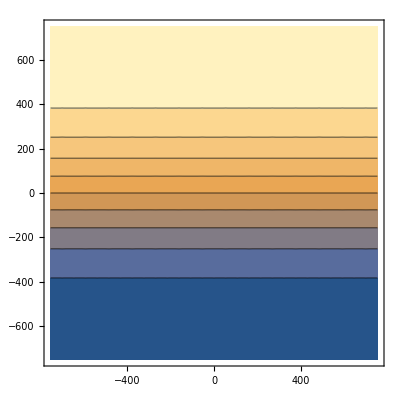

```mathematica
ContourPlot[Erf[(y-y0)/(√2 L sigmay)]/.x->xx/.A->1/.yy->y/.y0->0/.x0->0/.L->LL/.sigmay->10ssy/.sigmax->10ssx,{xx,-750,750},{y,-750,750},PlotRange->All]
```

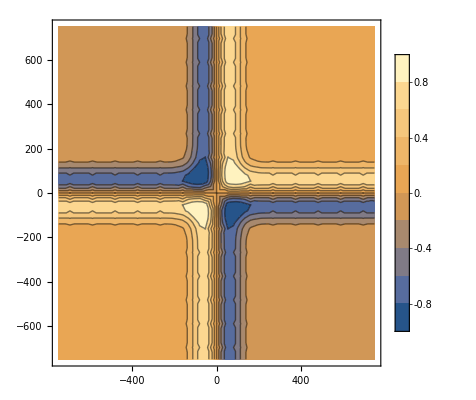

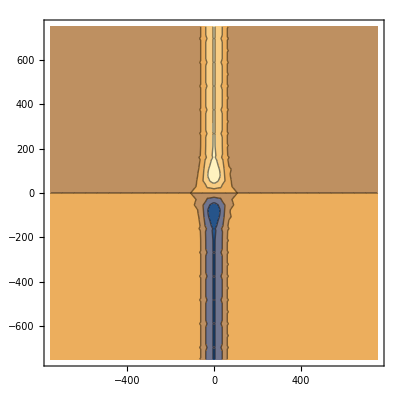

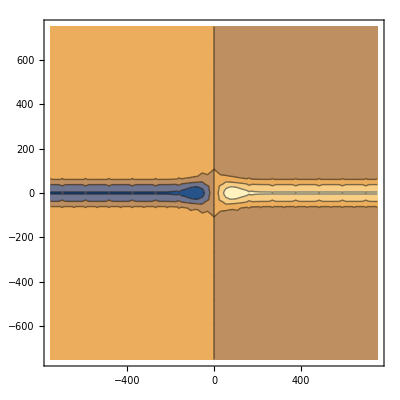

```mathematica
ContourPlot[intxofdy +intyofdx/.A->1/.yy->y/.y0->0/.x0->0/.L->LL/.sigmay->2ssy/.sigmax->2ssx,{x,-750,750},{y,-750,750},PlotRange->All,PlotLegends->Automatic]
ContourPlot[D[intxofdy +intyofdx,x]/.x->xx/.A->1/.yy->y/.y0->0/.x0->0/.L->LL/.sigmay->2ssy/.sigmax->2ssx,{xx,-750,750},{y,-750,750},PlotRange->All]
ContourPlot[D[intxofdy +intyofdx,y]/.y->yy/.A->1/.y->y/.y0->0/.x0->0/.L->LL/.sigmay->2 ssy/.sigmax->2ssx,{x,-750,750},{yy,-750,750},PlotRange->All]
```

```mathematica
Plot3D[intxofdy/.A->1/.yy->y/.y0->0/.x0->0/.L->LL/.sigmay->ssy/.sigmax->ssx,{x,-750,750},{y,-750,750},PlotRange->All]
Plot3D[intyofdx/.A->1/.yy->y/.y0->0/.x0->0/.L->LL/.sigmay->ssy/.sigmax->ssx,{x,-750,750},{y,-750,750},PlotRange->All]
Plot3D[intxofdy +intyofdx/.A->1/.yy->y/.y0->0/.x0->0/.L->LL/.sigmay->5ssy/.sigmax->5ssx,{x,-750,750},{y,-750,750},PlotRange->All,PlotLegends->Automatic]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
dtaRHS=StringReplace["(-6*S0^7*a3*(S0_t)+20*(S0_x)^4+20*(S0_y)^4-16*S0*(S0_x)^2*(2*(S0_xx)+(S0_yy))+S0^2*(5*(S0_xx)^2+4*(S0_xy)^2+8*(S0_x)*((S0_xxx)+(S0_xyy))+6*(S0_xx)*(S0_yy)+5*(S0_yy)^2)-8*(S0_y)^2*(-5*(S0_x)^2+2*S0*((S0_xx)+2*(S0_yy)))+8*S0*(S0_y)*(-4*(S0_x)*(S0_xy)+S0*((S0_xxy)+(S0_yyy)))-S0^3*((S0_xxxx)+2*(S0_xxyy)+(S0_yyyy))-3*S0^6*((fx1_x)+(fy1_y)))/(2*S0^8)",{"S0_yyyy"->"dyyyySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]","S0_xxxx"->"dxxxxSource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_xxx"->"dxxxSource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_yyy"->"dyyySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_xxyy"->"dxxyySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_xxy"->"dxxySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_xyy"->"dxyySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]","S0_t"->"dtSource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_xy"->"dxySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_xx"->"dxxSource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_x"->"dxSource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_yy"->"dyySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_y"->"dySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0"->"Source[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]","a3"->"a3[[tt,i,j]]","fx1_x"->"dxfx[[tt,i,j]]","fy1_y"->"dyfy[[tt,i,j]]"}];
dtaRHS1=StringReplace["(-6*S0^7*a3*(S0_t)+20*(S0_x)^4+20*(S0_y)^4-16*S0*(S0_x)^2*(2*(S0_xx)+(S0_yy))+S0^2*(5*(S0_xx)^2+4*(S0_xy)^2+8*(S0_x)*((S0_xxx)+(S0_xyy))+6*(S0_xx)*(S0_yy)+5*(S0_yy)^2)-8*(S0_y)^2*(-5*(S0_x)^2+2*S0*((S0_xx)+2*(S0_yy)))+8*S0*(S0_y)*(-4*(S0_x)*(S0_xy)+S0*((S0_xxy)+(S0_yyy)))-S0^3*((S0_xxxx)+2*(S0_xxyy)+(S0_yyyy)))/(2*S0^8)",{"S0_yyyy"->"dyyyySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]","S0_xxxx"->"dxxxxSource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_xxx"->"dxxxSource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_yyy"->"dyyySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_xxyy"->"dxxyySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_xxy"->"dxxySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_xyy"->"dxyySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]","S0_t"->"dtSource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_xy"->"dxySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_xx"->"dxxSource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_x"->"dxSource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_yy"->"dyySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_y"->"dySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0"->"Source[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]","a3"->"a3[[tt,i,j]]","fx1_x"->"dxfx[[tt,i,j]]","fy1_y"->"dyfy[[tt,i,j]]"}];
(*(-3*S0^6*((fx1_x)+(fy1_y)))/(2*S0^8)*)
dtaRHS2=StringReplace["(-3*S0^6*((fx1_x)+(fy1_y)))/(2*S0^8)",{"S0_yyyy"->"dyyyySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]","S0_xxxx"->"dxxxxSource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_xxx"->"dxxxSource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_yyy"->"dyyySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_xxyy"->"dxxyySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_xxy"->"dxxySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_xyy"->"dxyySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]","S0_t"->"dtSource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_xy"->"dxySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_xx"->"dxxSource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_x"->"dxSource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_yy"->"dyySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0_y"->"dySource[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]",
"S0"->"Source[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]","a3"->"a3[[tt,i,j]]","fx1_x"->"dxfx[[tt,i,j]]","fy1_y"->"dyfy[[tt,i,j]]"}];
dtaRHS3=StringReplace["(-3*S0^6*((fx1_x)+(fy1_y)))/(2*S0^8)",{
"S0"->"Source[times[[tt]],5000,2000,AA,xValues[[i]],0,ssx1,yValues[[j]],0,ssy1,LL]","a3"->"a3[[tt,i,j]]","fx1_x"->"dxfx[[tt,i,j]]","fy1_y"->"dyfy[[tt,i,j]]"}];
```

```mathematica
dta=Table[(dtaRHS//ToExpression),{tt,1,times//Length},{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

General::munfl: (-2.13785×10^-277)^4 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.13785×10^-277)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{13.5213,Null}

```mathematica
dta1=Table[(dtaRHS1//ToExpression),{tt,1,times//Length},{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

General::munfl: (-2.13785×10^-277)^4 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.13785×10^-277)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{12.9423,Null}

```mathematica
dta2=Table[(dtaRHS2//ToExpression),{tt,1,times//Length},{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
dta3=Table[(dtaRHS3//ToExpression),{tt,1,times//Length},{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.625285,Null}

{0.545008,Null}

```mathematica
t=4
```

4

```mathematica
Export["/home/giulio/Pictures/Jeccofydfydtfxdfxdt.jpeg",GraphicsGrid[{{ListContourPlot[fy[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"Jecco fy t="<>ToString[t dt each+init dt]](*,ListContourPlot[dyfy[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"Jecco dfy/dy t="<>ToString[t dt each+init dt]]*)},{ListContourPlot[fx[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"Jecco fx t="<>ToString[t dt each+init dt]],ListContourPlot[dtfx[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"Jecco dfx/dt t="<>ToString[t dt each+init dt]]}(*,*)},ImageSize->Full]]
```

/home/giulio/Pictures/Jeccofydfydtfxdfxdt.jpeg

```mathematica
a3//Length
```

31

```mathematica
(*Export["/home/giulio/Pictures/dadt.jpeg",*)t=6;
times[[t]]
GraphicsGrid[{{ListContourPlot[fy[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"fy: part with only the source t="<>ToString[t dt each+init dt]](*,ListContourPlot[dtfy[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"dfy/dy: term without source, dxfx+dyfy t="<>ToString[t dt each+init dt]]*)},{ListContourPlot[fx[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"fx: part with only the source t="<>ToString[t dt each+init dt]],ListContourPlot[dtfx[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"dfx/dx: term without source, dxfx+dyfy t="<>ToString[t dt each+init dt]]},{ListContourPlot[dta1[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"da/dt: part with only the source t="<>ToString[t dt each+init dt]],ListContourPlot[dta2[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"da/dt: term without source, dxfx+dyfy t="<>ToString[t dt each+init dt]]},{ListContourPlot[dta[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"da/dt: sum of the two parts t="<>ToString[t dt each+init dt]],ListContourPlot[a3[[t ]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->" a t="<>ToString[t dt each+init dt]]}(*,{ListContourPlot[dta3[[t]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"da/dt: sum of the two parts t="<>ToString[t dt each+init dt]]}*)},ImageSize->Full]
```

6111.11

-Graphics-

```mathematica
(*SBulk3=Table[Join[Obj3[[i,-1,20,20,;;-2]],Obj3[[i,2,20,20,;;-1]]]//Flatten,{i,1,FNames//Length}]*)
```

```mathematica
(*FxBulk3=Table[Join[Obj3[[i,5,20,20,;;-2]],Obj3[[i,4,20,20,;;-1]]]//Flatten,{i,1,FNames//Length}];*)
```

```mathematica
fxtName1[[1]]
```

/home/giulio/University/PhD/Simulations/testoutput/fx_t100.h5

```mathematica
init=15300;
end=16000;
each=100;
fxtFNames=Table[StringJoin["fx_t",ToString[i]],{i,init,end,each}];
fxtName1=Table[StringJoin["/home/giulio/University/PhD/Simulations/testoutput/",
fxtFNames[[i]],".h5"],{i,fxtFNames//Length}];
Timing[fxtJ=Table[Import[fxtName1[[i]],"Data"](*[[1]]*),{i,1,fxtName1//Length}]];//AbsoluteTiming
fxFNames=Table[StringJoin["fx",ToString[i]],{i,init,end,each}];
fxName1=Table[StringJoin["/home/giulio/University/PhD/Simulations/testoutput/",
fxFNames[[i]],".h5"],{i,fxFNames//Length}];
Timing[fxJ=Table[Import[fxName1[[i]],"Data"](*[[1]]*),{i,1,fxtName1//Length}]];//AbsoluteTiming
fyFNames=Table[StringJoin["fy",ToString[i]],{i,init,end,each}];
fyName1=Table[StringJoin["/home/giulio/University/PhD/Simulations/testoutput/",
fyFNames[[i]],".h5"],{i,fxtName1//Length}];
Timing[fyJ=Table[Import[fyName1[[i]],"Data"](*[[1]]*),{i,1,fxtName1//Length}]];//AbsoluteTiming
aFNames=Table[StringJoin["a",ToString[i]],{i,init,end,each}];
aName1=Table[StringJoin["/home/giulio/University/PhD/Simulations/testoutput/",
aFNames[[i]],".h5"],{i,aFNames//Length}];
Timing[aJ=Table[Import[aName1[[i]],"Data"](*[[1]]*),{i,1,aName1//Length}]];//AbsoluteTiming
bFNames=Table[StringJoin["b",ToString[i]],{i,init,end,each}];
bName1=Table[StringJoin["/home/giulio/University/PhD/Simulations/testoutput/",
bFNames[[i]],".h5"],{i,aFNames//Length}];
Timing[bJ=Table[Import[bName1[[i]],"Data"](*[[1]]*),{i,1,aName1//Length}]];//AbsoluteTiming
gFNames=Table[StringJoin["g",ToString[i]],{i,init,end,each}];
gName1=Table[StringJoin["/home/giulio/University/PhD/Simulations/testoutput/",
gFNames[[i]],".h5"],{i,aFNames//Length}];
Timing[gJ=Table[Import[gName1[[i]],"Data"](*[[1]]*),{i,1,aName1//Length}]];//AbsoluteTiming
FNames//Length
(*"/home/giulio/University/PhD/JeccoGt2/examples/BB_QNM_1D_4p1_Vchannel_xpert/"*)
```

{0.119945,Null}

{0.112597,Null}

{0.112926,Null}

{0.117773,Null}

{0.100997,Null}

{0.10561,Null}

31

```mathematica
axFNames=Table[StringJoin["ax",ToString[i]],{i,init,end,each}];
axName1=Table[StringJoin["/home/giulio/University/PhD/Simulations/testoutput/",
axFNames[[i]],".h5"],{i,aFNames//Length}];
Timing[axJ=Table[Import[axName1[[i]],"Data"](*[[1]]*),{i,1,aName1//Length}]];//AbsoluteTiming

bxFNames=Table[StringJoin["bx",ToString[i]],{i,init,end,each}];
bxName1=Table[StringJoin["/home/giulio/University/PhD/Simulations/testoutput/",
bxFNames[[i]],".h5"],{i,aFNames//Length}];
Timing[bxJ=Table[Import[bxName1[[i]],"Data"](*[[1]]*),{i,1,aName1//Length}]];//AbsoluteTiming

gyFNames=Table[StringJoin["gy",ToString[i]],{i,init,end,each}];
gyName1=Table[StringJoin["/home/giulio/University/PhD/Simulations/testoutput/",
gyFNames[[i]],".h5"],{i,aFNames//Length}];
Timing[gyJ=Table[Import[gyName1[[i]],"Data"](*[[1]]*),{i,1,aName1//Length}]];//AbsoluteTiming


sigmaFNames=Table[StringJoin["sigma",ToString[i]],{i,init,end,each}];
sigmaName1=Table[StringJoin["/home/giulio/University/PhD/Simulations/testoutput/",
sigmaFNames[[i]],".h5"],{i,aFNames//Length}];
Timing[sigmaJ=Table[Import[sigmaName1[[i]],"Data"](*[[1]]*),{i,1,aName1//Length}]];//AbsoluteTiming
```

{0.110255,Null}

{0.105595,Null}

{0.106175,Null}

{0.098062,Null}

```mathematica
sigmaJ[[1,1]]//Dimensions
```

{50,50}

```mathematica
times[[]]
```

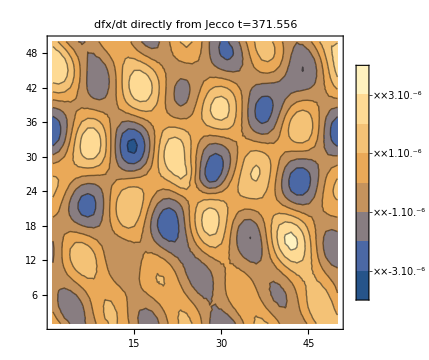
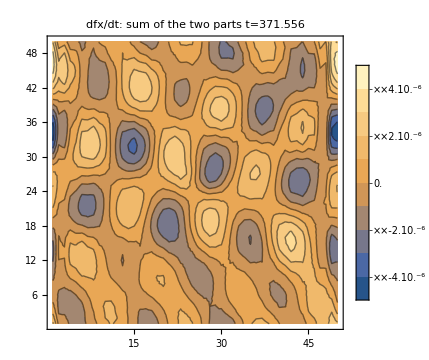

```mathematica
t=-1;
ListContourPlot[dtfx[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"dfx/dt: sum of the two parts t="<>ToString[t dt each+init dt]]ListContourPlot[fxtJ[[t,1,;;,;;,1]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->" dfx/dt directly from Jecco t="<>ToString[t dt each+init dt]]
```

```mathematica
ListContourPlot[dtfx[[t]]-(fxtJ[[t,1,;;,;;,1]]//Transpose),PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"dfx/dt: sum of the two parts t="<>ToString[t dt each+init dt]]
```

-Graphics-

```mathematica
t=-1;
GraphicsGrid[{{ListContourPlot[a3[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"a from output t="<>ToString[t dt each+init dt]],ListContourPlot[aJ[[t,1,;;,;;,1]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->" a direct output t="<>ToString[t dt each+init dt]]},{ListContourPlot[fx[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"fx from output t="<>ToString[t dt each+init dt]],ListContourPlot[fxJ[[t,1,;;,;;,1]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->" fx direct output t="<>ToString[t dt each+init dt]]},{ListContourPlot[fy[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"fy from output t="<>ToString[t dt each+init dt]],ListContourPlot[fyJ[[t,1,;;,;;,1]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->" fy direct output t="<>ToString[t dt each+init dt]]},
{ListContourPlot[b3[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"b from output t="<>ToString[t dt each+init dt]],ListContourPlot[bJ[[t,1,;;,;;,1]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->" b direct output t="<>ToString[t dt each+init dt]]},
{ListContourPlot[g3[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"b from output t="<>ToString[t dt each+init dt]],ListContourPlot[gJ[[t,1,;;,;;,1]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->" b direct output t="<>ToString[t dt each+init dt]]},{ListContourPlot[source[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"b from output t="<>ToString[t dt each+init dt]],ListContourPlot[sigmaJ[[t,1,;;,;;]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->" b direct output t="<>ToString[t dt each+init dt]]},{ListContourPlot[dxa3[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"da/dx from output t="<>ToString[t dt each+init dt]],ListContourPlot[axJ[[t,1,;;,;;]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->" ax direct output t="<>ToString[t dt each+init dt]]},{ListContourPlot[dxb3[[t]]//Transpose,PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"db/dx from output t="<>ToString[t dt each+init dt]],ListContourPlot[bxJ[[t,1,;;,;;]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->" bx direct output t="<>ToString[t dt each+init dt]]}},ImageSize->Full]
```

-Graphics-

```mathematica
t=-1;
GraphicsGrid[{(*{ListContourPlot[a3[[t]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"a from output t="<>ToString[t dt each+init dt]],ListContourPlot[aJ[[t,1,;;,;;,1]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->" a direct output t="<>ToString[t dt each+init dt]]},{ListContourPlot[fx[[t]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"fx from output t="<>ToString[t dt each+init dt]],ListContourPlot[fxJ[[t,1,;;,;;,1]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->" fx direct output t="<>ToString[t dt each+init dt]]},{ListContourPlot[fy[[t]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"fy from output t="<>ToString[t dt each+init dt]],ListContourPlot[fyJ[[t,1,;;,;;,1]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->" fy direct output t="<>ToString[t dt each+init dt]]},
{ListContourPlot[b3[[t]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"b from output t="<>ToString[t dt each+init dt]],ListContourPlot[bJ[[t,1,;;,;;,1]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->" b direct output t="<>ToString[t dt each+init dt]]},
{ListContourPlot[g3[[t]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"b from output t="<>ToString[t dt each+init dt]],ListContourPlot[gJ[[t,1,;;,;;,1]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->" b direct output t="<>ToString[t dt each+init dt]]},{ListContourPlot[source[[t]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"b from output t="<>ToString[t dt each+init dt]],ListContourPlot[sigmaJ[[t,1,;;,;;]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->" b direct output t="<>ToString[t dt each+init dt]]},*){ListContourPlot[dxa3[[t]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"da/dx from output t="<>ToString[t dt each+init dt]],ListContourPlot[axJ[[t,1,;;,;;]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->" ax direct output t="<>ToString[t dt each+init dt]]},{ListContourPlot[dxb3[[t]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->"db/dx from output t="<>ToString[t dt each+init dt]],ListContourPlot[bxJ[[t,1,;;,;;]],PlotRange->All,ImageSize->Medium,PlotLegends->Automatic,PlotLabel->" db/dx direct output t="<>ToString[t dt each+init dt]]}},ImageSize->Full]
```

-Graphics-

```mathematica
fxJ[[1,1]]//Dimensions
```

{50,50,1}

#### Stress Tensor

```mathematica
Tdd={{-1/(3 S0[tt,z,y]^5)(3 S0[tt,z,y]^5 ℰ[tt,z,y]+4 ((Derivative[0,0,1][S0][tt,z,y])^2+(Derivative[0,1,0][S0][tt,z,y])^2) Derivative[1,0,0][S0][tt,z,y]-S0[tt,z,y] (3 (Derivative[0,0,2][S0][tt,z,y]+Derivative[0,2,0][S0][tt,z,y]) Derivative[1,0,0][S0][tt,z,y]+2 (Derivative[0,0,1][S0][tt,z,y] Derivative[1,0,1][S0][tt,z,y]+Derivative[0,1,0][S0][tt,z,y] Derivative[1,1,0][S0][tt,z,y]))+S0[tt,z,y]^2 (2 (Derivative[1,0,0][S0][tt,z,y])^3+Derivative[1,0,2][S0][tt,z,y]+Derivative[1,2,0][S0][tt,z,y])-4 S0[tt,z,y]^3 Derivative[1,0,0][S0][tt,z,y] Derivative[2,0,0][S0][tt,z,y]+2 S0[tt,z,y]^4 Derivative[3,0,0][S0][tt,z,y]),1/(3 S0[tt,z,y]^5)(3 S0[tt,z,y]^5 ℱ[tt,z,y]+4 Derivative[0,1,0][S0][tt,z,y] ((Derivative[0,0,1][S0][tt,z,y])^2+(Derivative[0,1,0][S0][tt,z,y])^2)-S0[tt,z,y] (2 Derivative[0,0,1][S0][tt,z,y] Derivative[0,1,1][S0][tt,z,y]+Derivative[0,1,0][S0][tt,z,y] (3 Derivative[0,0,2][S0][tt,z,y]+5 Derivative[0,2,0][S0][tt,z,y]))+S0[tt,z,y]^2 (Derivative[0,1,2][S0][tt,z,y]+Derivative[0,3,0][S0][tt,z,y]-4 Derivative[0,1,0][S0][tt,z,y] (Derivative[1,0,0][S0][tt,z,y])^2)+S0[tt,z,y]^3 (4 Derivative[1,0,0][S0][tt,z,y] Derivative[1,1,0][S0][tt,z,y]+Derivative[0,1,0][S0][tt,z,y] Derivative[2,0,0][S0][tt,z,y])-S0[tt,z,y]^4 Derivative[2,1,0][S0][tt,z,y]),1/(3 S0[tt,z,y]^5)(3 S0[tt,z,y]^5 ℱ2[tt,z,y]+4 Derivative[0,0,1][S0][tt,z,y] ((Derivative[0,0,1][S0][tt,z,y])^2+(Derivative[0,1,0][S0][tt,z,y])^2)-S0[tt,z,y] (2 Derivative[0,1,0][S0][tt,z,y] Derivative[0,1,1][S0][tt,z,y]+Derivative[0,0,1][S0][tt,z,y] (5 Derivative[0,0,2][S0][tt,z,y]+3 Derivative[0,2,0][S0][tt,z,y]))+S0[tt,z,y]^2 (Derivative[0,0,3][S0][tt,z,y]+Derivative[0,2,1][S0][tt,z,y]-4 Derivative[0,0,1][S0][tt,z,y] (Derivative[1,0,0][S0][tt,z,y])^2)+S0[tt,z,y]^3 (4 Derivative[1,0,0][S0][tt,z,y] Derivative[1,0,1][S0][tt,z,y]+Derivative[0,0,1][S0][tt,z,y] Derivative[2,0,0][S0][tt,z,y])-S0[tt,z,y]^4 Derivative[2,0,1][S0][tt,z,y])},{1/(3 S0[tt,z,y]^5)(3 S0[tt,z,y]^5 ℱ[tt,z,y]+4 Derivative[0,1,0][S0][tt,z,y] ((Derivative[0,0,1][S0][tt,z,y])^2+(Derivative[0,1,0][S0][tt,z,y])^2)-S0[tt,z,y] (2 Derivative[0,0,1][S0][tt,z,y] Derivative[0,1,1][S0][tt,z,y]+Derivative[0,1,0][S0][tt,z,y] (3 Derivative[0,0,2][S0][tt,z,y]+5 Derivative[0,2,0][S0][tt,z,y]))+S0[tt,z,y]^2 (Derivative[0,1,2][S0][tt,z,y]+Derivative[0,3,0][S0][tt,z,y]-4 Derivative[0,1,0][S0][tt,z,y] (Derivative[1,0,0][S0][tt,z,y])^2)+S0[tt,z,y]^3 (4 Derivative[1,0,0][S0][tt,z,y] Derivative[1,1,0][S0][tt,z,y]+Derivative[0,1,0][S0][tt,z,y] Derivative[2,0,0][S0][tt,z,y])-S0[tt,z,y]^4 Derivative[2,1,0][S0][tt,z,y]),S0[tt,z,y] (-S0[tt,z,y] 𝒫[tt,z,y]+1/(3 S0[tt,z,y]^4)2 Derivative[1,0,0][S0][tt,z,y] ((Derivative[0,0,1][S0][tt,z,y])^2+(Derivative[0,1,0][S0][tt,z,y])^2-S0[tt,z,y] (Derivative[0,0,2][S0][tt,z,y]+Derivative[0,2,0][S0][tt,z,y]-S0[tt,z,y] (Derivative[1,0,0][S0][tt,z,y])^2+2 S0[tt,z,y]^2 Derivative[2,0,0][S0][tt,z,y]))+2/3 Derivative[3,0,0][S0][tt,z,y]),S0[tt,z,y]^2 𝒢[tt,z,y]},{1/(3 S0[tt,z,y]^5)(3 S0[tt,z,y]^5 ℱ2[tt,z,y]+4 Derivative[0,0,1][S0][tt,z,y] ((Derivative[0,0,1][S0][tt,z,y])^2+(Derivative[0,1,0][S0][tt,z,y])^2)-S0[tt,z,y] (2 Derivative[0,1,0][S0][tt,z,y] Derivative[0,1,1][S0][tt,z,y]+Derivative[0,0,1][S0][tt,z,y] (5 Derivative[0,0,2][S0][tt,z,y]+3 Derivative[0,2,0][S0][tt,z,y]))+S0[tt,z,y]^2 (Derivative[0,0,3][S0][tt,z,y]+Derivative[0,2,1][S0][tt,z,y]-4 Derivative[0,0,1][S0][tt,z,y] (Derivative[1,0,0][S0][tt,z,y])^2)+S0[tt,z,y]^3 (4 Derivative[1,0,0][S0][tt,z,y] Derivative[1,0,1][S0][tt,z,y]+Derivative[0,0,1][S0][tt,z,y] Derivative[2,0,0][S0][tt,z,y])-S0[tt,z,y]^4 Derivative[2,0,1][S0][tt,z,y]),S0[tt,z,y]^2 𝒢[tt,z,y],S0[tt,z,y] (S0[tt,z,y] 𝒫[tt,z,y]+1/(3 S0[tt,z,y]^4)2 Derivative[1,0,0][S0][tt,z,y] ((Derivative[0,0,1][S0][tt,z,y])^2+(Derivative[0,1,0][S0][tt,z,y])^2-S0[tt,z,y] (Derivative[0,0,2][S0][tt,z,y]+Derivative[0,2,0][S0][tt,z,y]-S0[tt,z,y] (Derivative[1,0,0][S0][tt,z,y])^2+2 S0[tt,z,y]^2 Derivative[2,0,0][S0][tt,z,y]))+2/3 Derivative[3,0,0][S0][tt,z,y])}}(*/.S0->Function[{tt,x,y},Source[tt,5000,2000,AA,x,0,ssx,y,0,ssy,LL]]*)//Simplify;(*{{(2 ℰ[t,z,y]-𝒫^(0,0,2)[t,z,y]+2 𝒢^(0,1,1)[t,z,y]+𝒫^(0,2,0)[t,z,y])/(16 π),-(3 ℱ[t,z,y]+ℱ^(0,0,2)[t,z,y]-ℱ2^(0,1,1)[t,z,y])/(16 π),-(3 ℱ2[t,z,y]-ℱ^(0,1,1)[t,z,y]+ℱ2^(0,2,0)[t,z,y])/(16 π)},{-(3 ℱ[t,z,y]+ℱ^(0,0,2)[t,z,y]-ℱ2^(0,1,1)[t,z,y])/(16 π),1/(48 π)(3 ℰ[t,z,y]-9 𝒫[t,z,y]+ℰ^(0,0,2)[t,z,y]-3 𝒫^(0,0,2)[t,z,y]+6 𝒢^(0,1,1)[t,z,y]+ℰ^(0,2,0)[t,z,y]+3 𝒫^(0,2,0)[t,z,y]),-(3 𝒢[t,z,y])/(16 π)},{-(3 ℱ2[t,z,y]-ℱ^(0,1,1)[t,z,y]+ℱ2^(0,2,0)[t,z,y])/(16 π),-(3 𝒢[t,z,y])/(16 π),1/(48 π)(3 ℰ[t,z,y]+9 𝒫[t,z,y]+ℰ^(0,0,2)[t,z,y]-3 𝒫^(0,0,2)[t,z,y]+6 𝒢^(0,1,1)[t,z,y]+ℰ^(0,2,0)[t,z,y]+3 𝒫^(0,2,0)[t,z,y])}}*)
```

```mathematica
Tdd/.S0->Function[{tt,x,y},1]
```

{{-ℰ[tt,z,y],ℱ[tt,z,y],ℱ2[tt,z,y]},{ℱ[tt,z,y],-𝒫[tt,z,y],𝒢[tt,z,y]},{ℱ2[tt,z,y],𝒢[tt,z,y],𝒫[tt,z,y]}}

```mathematica
gddBoundary={{-1,0,0},{0,S0[tt,z,y]^2,0},{0,0,S0[tt,z,y]^2}};
guuBoundary=Inverse[gddboundary]//Simplify;
```

```mathematica
gddBoundaryVector=Table[Table[gddBoundary/.S0->Function[{tt,x,y},Source[times[[100]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]],{i,1,a3[[1]]//Length},{j,1,a3[[1,1]]//Length}](*,{t,100,101(*a3//Length*)}*)];//AbsoluteTiming
```

{0.088799,Null}

```mathematica
Tud=Tdd.guuBoundary//Simplify;
```

```mathematica
TudVector=Table[Table[Tud/.ℰ[tt,z,y]->a3[[t,i,j]]/.𝒫[tt,z,y]->b3[[t,i,j]]/.ℱ[tt,z,y]->fx[[t,i,j]]/.ℱ2[tt,z,y]->fy[[t,i,j]]/.𝒢[tt,z,y]->g3[[t,i,j]]/.S0->Function[{tt,x,y},Source[times[[t]],5000,2000,AA,xValues[[i]],0,ssx,yValues[[j]],0,ssy,LL]],{i,1,a3[[1]]//Length},{j,1,4a3[[1,1]]//Length}],{t,1,2(*a3//Length*)}];//AbsoluteTiming
```

{4.96597,Null}

```mathematica
TudVector//Dimensions
```

{2,50,50,3,3}

```mathematica
ListContourPlot[TudVector[[2,;;,;;,1,3]],PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
gddBoundaryVector//Dimensions
```

{50,50,3,3}

```mathematica
vecs=Table[Select[Eigenvectors[TudVector[[1,xx,yy,;;,;;]]](*//Re*),FreeQ[#,Complex] (*Module[{u=#,norm},norm=u.gddBoundaryVector[[xx,yy]].u;
Re[norm]<0  (*Pick only timelike ones*)]*)&],(*{tt,1,2},*){xx,1,xValues//Length},{yy,1,yValues//Length}];//AbsoluteTiming
```

{0.040613,Null}

```mathematica
vals=Table[Select[Eigenvalues[TudVector[[1,xx,yy,;;,;;]]](*//Re*),FreeQ[#,Complex] (*Module[{u=#,norm},norm=u.gddBoundaryVector[[xx,yy]].u;
Re[norm]<0  (*Pick only timelike ones*)]*)&],(*{tt,1,2},*){xx,1,xValues//Length},{yy,1,yValues//Length}];//AbsoluteTiming
```

{0.030418,Null}

```mathematica
vals//Dimensions
```

{50,50,3}

```mathematica
ListContourPlot[vecs[[;;,;;,1,1]],PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

$Aborted

```mathematica
TudVector[[1,1,1]]//Eigenvectors
```

{{0.998836,-0.0482402,-0.000183014},{0.0487748,-0.996429,0.0689178},{-0.0035721,0.0691711,0.997598}}

#### Boundary velocity

The eigenvector has to be timelike!!!

```mathematica
ηdd = DiagonalMatrix[Join[{-r^2}, Table[r^2, {3 - 1}]]]; 

ηdd//MatrixForm
```

(-r^2 | 0 | 0
0 | r^2 | 0
0 | 0 | r^2)

```mathematica
Obj3//Length
```

201

```mathematica
yValues[[44]]//N
```

0.119048

```mathematica
yValues[[50]]//N
```

0.833333

```mathematica
iii=30;
jj=48;
vvv=1;
E1Modules=Table[ηdd.(TudVector[[i,iii,jj]]//Eigenvectors)[[1]].(TudVector[[i,iii,jj]]//Eigenvectors)[[1]]//Simplify,{i,1,Obj3//Length}];
E2Modules=Table[ηdd.(TudVector[[i,iii,jj]]//Eigenvectors)[[2]].(TudVector[[i,iii,jj]]//Eigenvectors)[[2]]//Simplify,{i,1,Obj3//Length}];
E3Modules=Table[ηdd.(TudVector[[i,iii,jj]]//Eigenvectors)[[3]].(TudVector[[i,iii,jj]]//Eigenvectors)[[3]]//Simplify,{i,1,Obj3//Length}];
```

```mathematica
ListPlot[{E1Modules/.r->1,E2Modules/.r->1,E3Modules/.r->1}]
```

-Graphics-

```mathematica
ValModules=Table[TudVector[[i,iii,jj]]//Eigenvalues,{i,1,Obj3//Length}];
ListPlot[{ValModules[[;;,1]],ValModules[[;;,2]],ValModules[[;;,3]]},PlotRange->All]
```

-Graphics-

```mathematica
EVectIndex2
```

```mathematica
E1Modules2=Table[ηdd.(TudVector[[i,40,40]]//Eigenvectors)[[1]].(TudVector[[i,40,40]]//Eigenvectors)[[1]]//Simplify,{i,1,Obj3//Length}];
E2Modules2=Table[ηdd.(TudVector[[i,40,40]]//Eigenvectors)[[2]].(TudVector[[i,40,40]]//Eigenvectors)[[2]]//Simplify,{i,1,Obj3//Length}];
E3Modules2=Table[ηdd.(TudVector[[i,40,40]]//Eigenvectors)[[3]].(TudVector[[i,40,40]]//Eigenvectors)[[3]]//Simplify,{i,1,Obj3//Length}];
```

```mathematica
ListPlot[{E1Modules2/.r->1,E2Modules2/.r->1,E3Modules2/.r->1}]
```

-Graphics-

```mathematica
ValModules2=Table[TudVector[[i,aa,aa]]//Eigenvalues,{i,1,Obj3//Length}];
ListPlot[{ValModules2[[;;,1]],ValModules2[[;;,2]],ValModules2[[;;,3]]},PlotRange->All,ImageSize->Large]
```

-Graphics-

```mathematica
EVectIndex=Table[PositionSmallest[{(ηdd.(TudVector[[t,i,j]]//Eigenvectors)[[1]].(TudVector[[t,i,j]]//Eigenvectors)[[1]])/.r->1,(ηdd.(TudVector[[t,i,j]]//Eigenvectors)[[2]].(TudVector[[t,i,j]]//Eigenvectors)[[2]])/.r->1,(ηdd.(TudVector[[t,i,j]]//Eigenvectors)[[3]].(TudVector[[t,i,j]]//Eigenvectors)[[3]])/.r->1}],{t,1,Obj3//Length},{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{7.73514,Null}

```mathematica
TudVector[[1,1,1]]//Eigenvalues
```

{0.41067,-0.235925,0.134244}

```mathematica
EVectIndex2=Table[PositionSmallest[TudVector[[t,i,j]]//Eigenvalues],{t,1,Obj3//Length},{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{4.36168,Null}

```mathematica
EVectIndex2[[30,41,21]]
```

{1}

```mathematica
EVectIndex//Dimensions
```

{201,84,84,1}

```mathematica
EVectIndex2//Dimensions
```

{201,84,84,1}

```mathematica
aa=43;
E1Modulesaa=Table[ηdd.(TudVector[[i,aa,aa]]//Eigenvectors)[[1]].(TudVector[[i,aa,aa]]//Eigenvectors)[[1]]//Simplify,{i,1,Obj3//Length}];
E2Modulesaa=Table[ηdd.(TudVector[[i,aa,aa]]//Eigenvectors)[[2]].(TudVector[[i,aa,aa]]//Eigenvectors)[[2]]//Simplify,{i,1,Obj3//Length}];
E3Modulesaa=Table[ηdd.(TudVector[[i,aa,aa]]//Eigenvectors)[[3]].(TudVector[[i,aa,aa]]//Eigenvectors)[[3]]//Simplify,{i,1,Obj3//Length}];
```

```mathematica
ListPlot[{E1Modulesaa/.r->1,E2Modulesaa/.r->1,E3Modulesaa/.r->1},ImageSize->Large]
```

-Graphics-

```mathematica
uint=Table[(TudVector[[t,i,j]]//Eigenvectors)[[EVectIndex[[t,i,j,1]]]],{t,1,Obj3//Length},{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
u=Table[uint[[t,i,j]]/Norm[uint[[t,i,j]]],{t,1,Obj3//Length},{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.746787,Null}

{0.176205,Null}

```mathematica
times=Table[0.002 (i-1),{i,1,Obj3//Length}];
```

```mathematica
uInt=(*Table[*)Interpolation[Table[{times[[t]],xValues[[i]],yValues[[j]],u[[t,i,j]]},{t,1,Obj3//Length},{i,1,xValues//Length},{j,1,yValues//Length}]//Flatten[#,2]&];//AbsoluteTiming
```

{0.3241,Null}

```mathematica
uInt[times[[1]],xValues[[1]],xValues[[1]]]
```

{0.763209,-0.646152,0.0000598231}

```mathematica
ListPlot[Table[u[[-1,40,j]][[1]],{j,1,yValues//Length}],Joined->True]
```

-Graphics-

```mathematica
Differences[xValues]
```

{5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42,5/42}

```mathematica
a
```

```mathematica
D[uInt[t,x,y],y]
```

InterpolatingFunction[{{0., 0.04}, {-5., 4.88095}, {-5., 4.88095}}, <>][t,x,y]

```mathematica
opa=10;
xValues[[opa]];
Plot[uInt[times[[1]],xValues[[opa]],y][[1]],{y,yValues[[1]],yValues[[-1]]},ImageSize->Large,PlotRange->All]
```

-Graphics-

```mathematica
D[uInt[times[[1]],xValues[[opa]],y],y]
```

```mathematica
StreamPlot[{uInt[times[[-1]],x,y][[2;;]]},{x,xValues[[1]],xValues[[-1]]},{y,yValues[[1]],yValues[[-1]]}(*,PlotLayout->"Row"*),PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

```mathematica
StreamPlot[{uInt[times[[2]],x,y][[2;;]]},{x,xValues[[1]],xValues[[-1]]},{y,yValues[[1]],yValues[[-1]]}(*,PlotLayout->"Row"*),PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

#### Vorticity

```mathematica
xValues//Length
```

84

```mathematica
NewxValues
```

{-5.,-4.5,-4.,-3.5,-3.,-2.5,-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5}

```mathematica
Δx=0.5;
Δy=0.5;
txy={tt,xx,yy};
Δtxy={times[[-1]]-times[[-2]],Δx,Δy};
NewxValues=Table[xValues[[1]]+i Δx,{i,0,Quotient[xValues[[-1]]-xValues[[1]],Δx]}];
NewyValues=Table[yValues[[1]]+i Δy,{i,0,Quotient[yValues[[-1]]-yValues[[1]],Δy]}];
DiffVect=Table[{1/Δtxy[[1]](uInt[times[[a+1//Mod[#,times//Length]&]],NewxValues[[b]],NewyValues[[c]]]-uInt[times[[a]],NewxValues[[b]],NewyValues[[c]]]),1/Δx(uInt[times[[a]],NewxValues[[b+1//Mod[#,NewxValues//Length]&]],NewyValues[[c]]]-uInt[times[[a]],NewxValues[[b-1//Mod[#,NewxValues//Length]&]],NewyValues[[c]]]),1/Δy(uInt[times[[a]],NewxValues[[b]],NewyValues[[c+1//Mod[#,NewyValues//Length]&]]]-uInt[times[[a]],NewxValues[[b]],NewyValues[[c-1//Mod[#,NewyValues//Length]&]]])},{a,1,times//Length},{b,1,NewxValues//Length},{c,1,NewyValues//Length}];//AbsoluteTiming
```

{24.0953,Null}

```mathematica
txy
```

{tt,xx,yy}

```mathematica
ϵ=LeviCivitaTensor[3]//Normal;
```

```mathematica
ω=Function[{t,x,y},Sum[ϵ[[i,j,k]]Evaluate[uInt[t,x,y]][[i]](D[uInt[tt,xx,yy],txy[[j]]]/.tt->t/.xx->x/.yy->y)[[k]],{i,1,3},{j,1,3},{k,1,3}]];//AbsoluteTiming
```

```mathematica
ω2=Function[{t,x,y},(D[uInt[tt,xx,yy],yy]/.tt->t/.xx->x/.yy->y)[[2]]-(D[uInt[tt,xx,yy],xx]/.tt->t/.xx->x/.yy->y)[[3]]];
```

```mathematica
ωAList=Table[ω2[times[[2]],xValues[[40]],yValues[[y]]](*,{x,1,xValues//Length}*),{y,1,yValues//Length}];//AbsoluteTiming
```

{22.3697,Null}

```mathematica
22 84/60//N
```

30.8

```mathematica
ListPlot[ωAList,Joined->True]
```

-Graphics-

```mathematica
ωAListm1=Table[ω[times[[-1]],xValues[[x]],yValues[[y]]],{x,1,xValues//Length},{y,1,yValues//Length}];//AbsoluteTiming
ωAList10=Table[ω[times[[10]],xValues[[x]],yValues[[y]]],{x,1,xValues//Length},{y,1,yValues//Length}];//AbsoluteTiming
```

{24620.2,Null}

$Aborted

```mathematica
ωAList[[1]]
```

-8.82521

```mathematica
plottin=Table[{xValues[[x]],yValues[[yyy]],ωAListm1[[x,yyy]]},{x,1,xValues//Length},{yyy,1,yValues//Length}];
```

```mathematica
Flatten[plottin,1]//Dimensions
```

{7056,3}

```mathematica
ListContourPlot[Flatten[plottin,1]]
```

-Graphics-

```mathematica
DiffVect[[;;,1,;;]]=Table[{(uInt[times[[a+1//Mod[#,times//Length]&]],NewxValues[[1]],NewyValues[[c]]]-uInt[times[[a]],NewxValues[[1]],NewyValues[[c]]])/Δtxy[[1]],(uInt[times[[a]],NewxValues[[1+1//Mod[#,NewxValues//Length]&]],NewyValues[[c]]]-uInt[times[[a]],NewxValues[[-1//Mod[#,NewxValues//Length]&]],NewyValues[[c]]])/Δx,(uInt[times[[a]],NewxValues[[1]],NewyValues[[c+1//Mod[#,NewyValues//Length]&]]]-uInt[times[[a]],NewxValues[[1]],NewyValues[[c-1//Mod[#,NewyValues//Length]&]]])/Δy},{a,1,times//Length},{c,1,NewyValues//Length}];//AbsoluteTiming
```

{1.2721,Null}

```mathematica
DiffVect[[;;,-2,;;]]=Table[{(uInt[times[[a+1//Mod[#,times//Length]&]],NewxValues[[-2]],NewyValues[[c]]]-uInt[times[[a]],NewxValues[[-2]],NewyValues[[c]]])/Δtxy[[1]],(uInt[times[[a]],NewxValues[[-1//Mod[#,NewxValues//Length]&]],NewyValues[[c]]]-uInt[times[[a]],NewxValues[[-2-1//Mod[#,NewxValues//Length]&]],NewyValues[[c]]])/Δx,(uInt[times[[a]],NewxValues[[-2]],NewyValues[[c+1//Mod[#,NewyValues//Length]&]]]-uInt[times[[a]],NewxValues[[-2]],NewyValues[[c-1//Mod[#,NewyValues//Length]&]]])/Δy},{a,1,times//Length},{c,1,NewyValues//Length}];//AbsoluteTiming
```

{1.25466,Null}

```mathematica
DiffVect[[;;,;;,1]]=Table[{(uInt[times[[a+1//Mod[#,times//Length]&]],NewxValues[[b]],NewyValues[[1]]]-uInt[times[[a]],NewxValues[[b]],NewyValues[[1]]])/Δtxy[[1]],(uInt[times[[a]],NewxValues[[b+1//Mod[#,NewxValues//Length]&]],NewyValues[[1]]]-uInt[times[[a]],NewxValues[[b-1//Mod[#,NewxValues//Length]&]],NewyValues[[1]]])/Δx,(uInt[times[[a]],NewxValues[[b]],NewyValues[[1+1//Mod[#,NewyValues//Length]&]]]-uInt[times[[a]],NewxValues[[b]],NewyValues[[-1//Mod[#,NewyValues//Length]&]]])/Δy},{a,1,times//Length},{b,1,NewxValues//Length}];//AbsoluteTiming
```

{1.30314,Null}

```mathematica
DiffVect[[;;,;;,-2]]=Table[{(uInt[times[[a+1//Mod[#,times//Length]&]],NewxValues[[b]],NewyValues[[-2]]]-uInt[times[[a]],NewxValues[[b]],NewyValues[[-2]]])/Δtxy[[1]],(uInt[times[[a]],NewxValues[[b+1//Mod[#,NewxValues//Length]&]],NewyValues[[-2]]]-uInt[times[[a]],NewxValues[[b-1//Mod[#,NewxValues//Length]&]],NewyValues[[-2]]])/Δx,(uInt[times[[a]],NewxValues[[b]],NewyValues[[-2+1//Mod[#,NewyValues//Length]&]]]-uInt[times[[a]],NewxValues[[b]],NewyValues[[-2-1//Mod[#,NewyValues//Length]&]]])/Δy},{a,1,times//Length},{b,1,NewxValues//Length}];//AbsoluteTiming
```

{1.28383,Null}

```mathematica
DiffVect[[;;,1,1]]=DiffVect[[;;,-1,-1]];
DiffVect[[;;,1,-2]]=DiffVect[[;;,-1,-2]];
DiffVect[[;;,-2,1]]=DiffVect[[;;,-2,-1]];
DiffVect[[;;,-2,-2]]=Table[{(uInt[times[[a+1//Mod[#,times//Length]&]],NewxValues[[-2]],NewyValues[[-2]]]-uInt[times[[a]],NewxValues[[-2]],NewyValues[[-2]]])/Δtxy[[1]],(uInt[times[[a]],NewxValues[[-2+1//Mod[#,NewxValues//Length]&]],NewyValues[[-2]]]-uInt[times[[a]],NewxValues[[-2-1//Mod[#,NewxValues//Length]&]],NewyValues[[-2]]])/Δx,(uInt[times[[a]],NewxValues[[-2]],NewyValues[[-2+1//Mod[#,NewyValues//Length]&]]]-uInt[times[[a]],NewxValues[[-2]],NewyValues[[-2-1//Mod[#,NewyValues//Length]&]]])/Δy},{a,1,times//Length}];
```

```mathematica
DiffVect[[3,1,1]](*[[1,1]]*)
```

{{-4.62252,5.66345,-0.388603},{0.0126309,-0.015786,0.00707602},{-0.487236,-1.44008,-0.0152004}}

```mathematica
ωList=Table[Sum[ϵ[[i,j,k]]uInt[times[[a]],NewxValues[[b]],NewyValues[[c]]][[i]]DiffVect[[a,b,c]][[j,k]],{i,1,3},{j,1,3},{k,1,3}],{a,1,times//Length},{b,1,NewxValues//Length},{c,1,NewyValues//Length}];//AbsoluteTiming
```

$Aborted

```mathematica
ωToPlot=Table[{NewxValues[[x]],NewyValues[[y]],ωList[[4,x,y]]},{x,1,NewxValues//Length},{y,1,NewyValues//Length}];//AbsoluteTiming
```

{0.019127,Null}

```mathematica
(Flatten[ωToPlot,1][[1]]//Transpose)
```

{1.80533,-5.,-5.}

```mathematica
ListPlot3D[Flatten[ωToPlot,1],PlotLegends->Automatic,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[ωToPlot,1],PlotLegends->Automatic,PlotRange->All]
```

-Graphics3D-

```mathematica
ContourPlot[ω[times[[-1]],x,y](*,{t,times[[1]],times[[-1]]}*),{x,xValues[[1]],xValues[[-1]]},{y,yValues[[1]],yValues[[-1]]}]//AbsoluteTiming
```

$Aborted

```mathematica
DiscreteDerivative
```

#### Bulk

```mathematica
SBulk3SecondOne=Join[Obj3[[1,-2,;;,;;,;;-2]],Obj3[[1,2,;;,;;,;;-2]],Obj3[[1,12,;;,;;,;;-2]],Obj3[[1,-9,;;,;;,;;-2]],Obj3[[1,-5,;;,;;,;;-1]],3];
```

```mathematica
FxBulk3SecondOne=Join[Obj3[[1,6,;;,;;,;;-2]],Obj3[[1,5,;;,;;,;;-2]],Obj3[[1,-11,;;,;;,;;-2]],Obj3[[1,-13,;;,;;,;;-2]],Obj3[[1,-12,;;,;;,;;-1]],3];
FyBulk3SecondOne=Join[Obj3[[1,8,;;,;;,;;-2]],Obj3[[1,-6,;;,;;,;;-2]],Obj3[[1,7,;;,;;,;;-2]],Obj3[[1,11,;;,;;,;;-2]],Obj3[[1,14,;;,;;,;;-1]],3];
ABulk3SecondOne=Join[Obj3[[1,-2,;;,;;,;;-2]],Obj3[[1,3,;;,;;,;;-1]],3];
```

```mathematica
SBulk3SecondOne//Dimensions
(*FxBulk3SecondOne//Dimensions*)
```

{36,12,56}

```mathematica
ListPlot[FyBulk3SecondOne[[10,1,;;]]]
```

-Graphics-

```mathematica
FyBulk3SecondOne[[;;,1,;;]]
```

Null

```mathematica
(*Transpose[FxBulk3SecondOne,{3,2,1}]*)
```

```mathematica
BBulk3Second=Table[Join[Obj3[[i,3,;;,;;,;;-2]],Obj3[[i,1,;;,;;,;;-1]],3],{i,1,FNames//Length}];
(*GBulk=Table[Join[Obj3[[i,1,1,20,;;]],Obj3[[i,6,1,20,;;]],Obj3[[i,4,1,20,;;]]]//Flatten,{i,1,FNames//Length}];*)
```

```mathematica
BBulk3SecondOne//Dimensions
```

{24,12,87}

```mathematica
BBulk3Second[[1,1,;;,50]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ListLinePlot[BBulk3Second[[1,1,2,;;]]]
```

-Graphics-

```mathematica
ListPlot3D[SBulk3SecondOne[[1,;;,;;]],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[BBulk3Second[[90,1,;;,24;;]],PlotRange->All]
```

```mathematica
BBulk3[[1,-1]]
BBulk3[[-1,-1]]
```

-1.31544

-1.31559

```mathematica
Bbulk=Join[Obj3[[;;,3,1,1,;;]],Obj3[[;;,1,1,1,;;]],2];Gbulk=Join[Obj3[[;;,2,1,1,;;]],Obj3[[;;,4,1,1,;;]],2];
(*Gbulk=Join[Obj3[[;;,6,1,1,;;]],Obj3[[;;,5,1,1,;;]],Obj3[[;;,3,1,1,;;]],Obj3[[;;,-1,1,1,;;]],2];*)
```

```mathematica
ListPlot[FxBulk3[[1]],PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

```mathematica
t=1;
ListPlot[Join[Obj3[[t,3,1,1,;;]],Obj3[[t,1,1,1,;;]]]//Flatten,Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Obj3[[1,1,1,1,1]]
```

0.

```mathematica
ListPlot[Table[{t 0.002,Obj3[[t,1,1,1,1]](*-Obj[[-1,3,1,1,1]]*)},{t,1,Obj3//Length}],PlotRange->All]
```

-Graphics-

#### T

## Working Desk

No comments, a lot of random stuff that could may be  useful again in the future mainly for plotting reasons.

### Producing ID from checkpoint

```mathematica
(*New grid*)
NPoints2=200;
xValues2=Range[b,a,(a 2)/NPoints2][[1;;-2]];
yValues2=Range[b,a,(a 2)/NPoints2][[1;;-2]];
MyGrid2=Table[{uValues[[i,u]],xValues2[[x]],yValues2[[y]]},{i,1,uValues//Length},{u,1,uValues[[i]]//Length},{x,1,xValues2//Length},{y,1,yValues2//Length}];
```

#### Gauge

```mathematica
xi=Obj[[1,1,;;,;;,1]];
xiGrid=Table[{{xValues[[i]],yValues[[j]]},xi[[j,i]]},{i,1,xValues//Length},{j,1,yValues//Length}]//Flatten[#,1]&;
```

```mathematica
xiFunction=Interpolation[xiGrid]
```

InterpolatingFunction[…]

```mathematica
Plot3D[xiFunction[x,y],{x,-750,740},{y,-750,740}]
```

-Graphics3D-

```mathematica
xiData=Table[xiFunction[xValues2[[i]],yValues2[[j]]],{i,1,xValues2//Length},{j,1,yValues2//Length}];
```

InterpolatingFunction::dmval: Input value {-750,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1485/2,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-735,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialxi_BBB.h5",{"xi"->xiData},"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialxi_BBB.h5

#### a3

```mathematica
a3=Obj[[1,-2,;;,;;,1]];
a3Grid=Table[{{xValues[[i]],yValues[[j]]},a3[[j,i]]},{i,1,xValues//Length},{j,1,yValues//Length}]//Flatten[#,1]&;
```

```mathematica
a3Function=Interpolation[a3Grid]
```

InterpolatingFunction[…]

```mathematica
Plot3D[a3Function[x,y],{x,-750,740},{y,-750,740}]
```

-Graphics3D-

```mathematica
a3Data=Table[a3Function[xValues2[[i]],yValues2[[j]]],{i,1,xValues2//Length},{j,1,yValues2//Length}];
```

InterpolatingFunction::dmval: Input value {-750,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1485/2,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-735,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitiala3_BBB.h5",{"a3"->a3Data},"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitiala3_BBB.h5

#### fx

```mathematica
fx=Obj[[1,5,;;,;;,1]];
fxGrid=Table[{{xValues[[i]],yValues[[j]]},fx[[j,i]]},{i,1,xValues//Length},{j,1,yValues//Length}]//Flatten[#,1]&;
```

```mathematica
fxFunction=Interpolation[fxGrid]
```

InterpolatingFunction[…]

```mathematica
ListPlot[fx[[;;,-5]]]
```

-Graphics-

```mathematica
Plot3D[fxFunction[x,y],{x,-750,740},{y,-750,740}]
```

-Graphics3D-

```mathematica
fxData=Table[fxFunction[xValues2[[i]],yValues2[[j]]],{i,1,xValues2//Length},{j,1,yValues2//Length}];
```

InterpolatingFunction::dmval: Input value {-750,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1485/2,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-735,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialfx_BBB.h5",{"fx"->fxData},"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialfx_BBB.h5

#### fy

```mathematica
fy=Obj[[1,6,;;,;;,1]];
fyGrid=Table[{{xValues[[i]],yValues[[j]]},fy[[j,i]]},{i,1,xValues//Length},{j,1,yValues//Length}]//Flatten[#,1]&;
```

```mathematica
fyFunction=Interpolation[fyGrid]
```

InterpolatingFunction[…]

```mathematica
ListPlot[fy[[-5]]]
```

-Graphics-

```mathematica
Plot3D[fyFunction[x,y],{x,-750,740},{y,-750,740}]
```

-Graphics3D-

```mathematica
fyData=Table[fyFunction[xValues2[[i]],yValues2[[j]]],{i,1,xValues2//Length},{j,1,yValues2//Length}];
```

InterpolatingFunction::dmval: Input value {-750,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1485/2,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-735,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialfy_BBB.h5",{"fy"->fyData},"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialfy_BBB.h5

#### B

```mathematica
B[[1,21]]
```

{{-0.0583564,-0.0584068,-0.0585853,-0.058867,-0.059261,-0.0597519,-0.0603343,-0.0609936,-0.0617149,-0.0624811,-0.0632695,-0.0640601,-0.0648236,-0.0655395,-0.0661763,-0.0667198,-0.0671455,-0.0674545,-0.0676344,-0.0676978},{-0.0684917,-0.0685365,-0.0686959,-0.0689471,-0.0692989,-0.0697373,-0.0702576,-0.0708466,-0.0714908,-0.0721747,-0.0728776,-0.0735811,-0.0742583,-0.07489,-0.0754476,-0.0759186,-0.0762824,-0.0765427,-0.0766919,-0.0767443},{-0.078815,-0.0788468,-0.0789601,-0.079139,-0.0793899,-0.0797033,-0.0800759,-0.0804985,-0.0809612,-0.0814526,-0.0819572,-0.0824607,-0.0829422,-0.0833863,-0.0837711,-0.0840875,-0.0843229,-0.0844845,-0.0845728,-0.0846035},{-0.0892139,-0.089225,-0.089264,-0.0893266,-0.0894159,-0.0895299,-0.0896683,-0.0898285,-0.0900072,-0.0901999,-0.0903994,-0.0905978,-0.090784,-0.0909475,-0.0910769,-0.0911672,-0.0912173,-0.0912374,-0.0912396,-0.0912391},{-0.0996322,-0.0996153,-0.0995521,-0.0994563,-0.0993256,-0.0991699,-0.0989932,-0.0988035,-0.0986065,-0.0984072,-0.0982103,-0.098016,-0.0978258,-0.0976349,-0.097445,-0.0972547,-0.0970771,-0.096924,-0.0968218,-0.0967834},{-0.11007,-0.110019,-0.109828,-0.109535,-0.109132,-0.108644,-0.108082,-0.107468,-0.106819,-0.106153,-0.105489,-0.104836,-0.10421,-0.103613,-0.103061,-0.102554,-0.102122,-0.101776,-0.101559,-0.101478},{-0.120569,-0.120477,-0.120137,-0.119614,-0.118894,-0.118022,-0.117018,-0.11592,-0.114761,-0.113573,-0.112391,-0.111234,-0.110135,-0.1091,-0.108161,-0.107319,-0.106619,-0.106071,-0.105734,-0.105609},{-0.131186,-0.131049,-0.13054,-0.12976,-0.128687,-0.127391,-0.1259,-0.124275,-0.122564,-0.120816,-0.119084,-0.117397,-0.115806,-0.114318,-0.112983,-0.111798,-0.110829,-0.110077,-0.109621,-0.10945},{-0.141961,-0.141776,-0.141084,-0.140027,-0.138574,-0.136822,-0.134815,-0.132632,-0.130343,-0.128012,-0.125714,-0.123486,-0.121396,-0.119453,-0.117723,-0.1162,-0.114966,-0.114014,-0.113441,-0.113227},{-0.15289,-0.152654,-0.15177,-0.150421,-0.14857,-0.146345,-0.143802,-0.141045,-0.138165,-0.135244,-0.132376,-0.129607,-0.127022,-0.124631,-0.122516,-0.120664,-0.119174,-0.118029,-0.117346,-0.117089},{-0.163902,-0.163615,-0.162533,-0.160886,-0.15863,-0.155923,-0.152838,-0.149504,-0.146034,-0.142526,-0.139095,-0.135796,-0.132729,-0.129905,-0.127419,-0.125252,-0.123519,-0.122192,-0.121406,-0.121108},{-0.174853,-0.174514,-0.173235,-0.171292,-0.168632,-0.165448,-0.161828,-0.157928,-0.15388,-0.149802,-0.145828,-0.142018,-0.138491,-0.135254,-0.132417,-0.129954,-0.127994,-0.126497,-0.125614,-0.125277},{-0.185529,-0.185139,-0.183669,-0.181439,-0.178389,-0.174747,-0.170613,-0.166171,-0.161573,-0.156953,-0.152465,-0.148174,-0.144216,-0.140594,-0.137432,-0.134695,-0.132526,-0.130872,-0.129901,-0.129529},{-0.195661,-0.195224,-0.193575,-0.191076,-0.187663,-0.183592,-0.178981,-0.174036,-0.16893,-0.163811,-0.15885,-0.15412,-0.149768,-0.145796,-0.142339,-0.139354,-0.136997,-0.135202,-0.134152,-0.133749},{-0.204955,-0.204476,-0.202666,-0.199926,-0.196187,-0.191733,-0.186696,-0.181302,-0.175743,-0.170181,-0.164801,-0.159682,-0.154983,-0.150702,-0.146988,-0.143785,-0.141264,-0.139346,-0.138228,-0.137798},{-0.213121,-0.212607,-0.210659,-0.207715,-0.203698,-0.198919,-0.193519,-0.187745,-0.181803,-0.175866,-0.170133,-0.164686,-0.159695,-0.155155,-0.151224,-0.14784,-0.145181,-0.143161,-0.141986,-0.141533},{-0.219905,-0.219362,-0.217306,-0.2142,-0.209964,-0.204928,-0.199243,-0.19317,-0.186926,-0.180693,-0.174682,-0.168976,-0.163755,-0.159012,-0.15491,-0.151384,-0.148618,-0.146518,-0.145298,-0.144827},{-0.225116,-0.224553,-0.222422,-0.219202,-0.214813,-0.209598,-0.203713,-0.197429,-0.190972,-0.184532,-0.178325,-0.172438,-0.167055,-0.162168,-0.157946,-0.154319,-0.151478,-0.149321,-0.148071,-0.147587},{-0.22865,-0.228077,-0.225904,-0.222623,-0.218151,-0.212837,-0.206842,-0.200443,-0.193869,-0.187313,-0.180997,-0.175009,-0.169535,-0.164567,-0.160278,-0.156594,-0.153711,-0.151521,-0.150253,-0.149762},{-0.2305,-0.229925,-0.227747,-0.224456,-0.219971,-0.214641,-0.208628,-0.202208,-0.195613,-0.189036,-0.182698,-0.176688,-0.171195,-0.16621,-0.161906,-0.158209,-0.155316,-0.153119,-0.151847,-0.151354},{-0.230757,-0.23019,-0.228039,-0.22479,-0.220359,-0.215093,-0.20915,-0.202801,-0.196277,-0.189767,-0.183492,-0.177539,-0.172095,-0.167154,-0.162885,-0.159218,-0.156346,-0.154166,-0.152902,-0.152413},{-0.229602,-0.22905,-0.226958,-0.223796,-0.219482,-0.214352,-0.208558,-0.202365,-0.195996,-0.189636,-0.183501,-0.177677,-0.172347,-0.167505,-0.163319,-0.159721,-0.1569,-0.154759,-0.153516,-0.153035},{-0.227285,-0.226756,-0.224748,-0.221712,-0.217569,-0.212637,-0.207063,-0.201099,-0.194959,-0.188821,-0.182894,-0.177261,-0.172101,-0.167409,-0.163348,-0.159854,-0.157111,-0.155028,-0.153817,-0.15335},{-0.224099,-0.223597,-0.221695,-0.218817,-0.214888,-0.210206,-0.204908,-0.199233,-0.193382,-0.187527,-0.181864,-0.176477,-0.171534,-0.167035,-0.163134,-0.159775,-0.157133,-0.155124,-0.153955,-0.153504},{-0.220348,-0.219878,-0.218098,-0.215402,-0.211719,-0.207325,-0.202346,-0.197006,-0.191492,-0.185966,-0.180613,-0.175513,-0.170826,-0.166553,-0.162843,-0.159642,-0.15712,-0.155201,-0.154081,-0.153651},{-0.216322,-0.215887,-0.214239,-0.211742,-0.208326,-0.204246,-0.199616,-0.194643,-0.189499,-0.184335,-0.179324,-0.174543,-0.170141,-0.166122,-0.162624,-0.159603,-0.157216,-0.155398,-0.154333,-0.153926},{-0.212271,-0.211872,-0.210362,-0.208071,-0.204934,-0.201182,-0.196919,-0.192331,-0.187578,-0.182798,-0.178151,-0.17371,-0.169613,-0.165867,-0.162599,-0.159771,-0.157531,-0.155822,-0.154819,-0.154436},{-0.208384,-0.208022,-0.20665,-0.204567,-0.201713,-0.198294,-0.194402,-0.190207,-0.185853,-0.181467,-0.177196,-0.173107,-0.169328,-0.165866,-0.16284,-0.160216,-0.158131,-0.156538,-0.1556,-0.155242},{-0.204781,-0.204454,-0.203219,-0.20134,-0.198763,-0.195672,-0.192149,-0.188344,-0.184389,-0.180397,-0.176504,-0.17277,-0.169315,-0.166144,-0.163365,-0.160951,-0.159026,-0.157554,-0.156684,-0.156353},{-0.201507,-0.201214,-0.200109,-0.198427,-0.196117,-0.193343,-0.190175,-0.186749,-0.183182,-0.179577,-0.176055,-0.172675,-0.16954,-0.16666,-0.16413,-0.161928,-0.160166,-0.158816,-0.158015,-0.157711},{-0.19854,-0.198279,-0.197296,-0.195798,-0.193739,-0.191263,-0.188432,-0.185367,-0.18217,-0.178935,-0.175772,-0.172732,-0.16991,-0.167314,-0.16503,-0.163036,-0.161437,-0.160208,-0.159477,-0.159199},{-0.195798,-0.195566,-0.194695,-0.193366,-0.191538,-0.189336,-0.186817,-0.184085,-0.181233,-0.178346,-0.175519,-0.172802,-0.170278,-0.167953,-0.165904,-0.164112,-0.162669,-0.161559,-0.160895,-0.160643},{-0.193154,-0.192949,-0.192177,-0.190999,-0.189377,-0.187423,-0.185184,-0.182753,-0.180215,-0.177643,-0.175125,-0.172703,-0.170453,-0.16838,-0.16655,-0.164947,-0.163652,-0.162652,-0.162052,-0.161825},{-0.190455,-0.190273,-0.189588,-0.18854,-0.187098,-0.185358,-0.183363,-0.181197,-0.178933,-0.176639,-0.174393,-0.172235,-0.170229,-0.16838,-0.166747,-0.165313,-0.164151,-0.163252,-0.16271,-0.162506},{-0.187539,-0.187375,-0.186762,-0.185824,-0.184531,-0.182971,-0.181182,-0.179238,-0.177206,-0.175147,-0.173132,-0.171196,-0.169398,-0.167741,-0.166275,-0.164987,-0.16394,-0.163127,-0.162636,-0.162451},{-0.184251,-0.184103,-0.183547,-0.182696,-0.181523,-0.180107,-0.178482,-0.176716,-0.174869,-0.172999,-0.171169,-0.169412,-0.16778,-0.166277,-0.164946,-0.163774,-0.16282,-0.162078,-0.161628,-0.161459},{-0.180463,-0.180326,-0.179813,-0.179027,-0.177945,-0.176637,-0.175135,-0.173503,-0.171796,-0.170067,-0.168376,-0.166751,-0.165243,-0.163854,-0.162622,-0.161537,-0.160652,-0.159962,-0.159543,-0.159386},{-0.176081,-0.175951,-0.175469,-0.174728,-0.173708,-0.172474,-0.171058,-0.169518,-0.167907,-0.166275,-0.164677,-0.163142,-0.161715,-0.1604,-0.159234,-0.158206,-0.157366,-0.156711,-0.156313,-0.156163},{-0.171054,-0.170929,-0.170465,-0.169752,-0.16877,-0.167582,-0.166218,-0.164733,-0.163179,-0.161603,-0.160059,-0.158574,-0.157193,-0.155918,-0.154786,-0.153787,-0.152971,-0.152335,-0.151949,-0.151803},{-0.165376,-0.165253,-0.164797,-0.164098,-0.163134,-0.161968,-0.160629,-0.15917,-0.157642,-0.15609,-0.154568,-0.153101,-0.151734,-0.150471,-0.149348,-0.148358,-0.147549,-0.146919,-0.146537,-0.146393},{-0.15908,-0.158957,-0.158504,-0.157807,-0.156848,-0.155687,-0.154352,-0.152898,-0.151373,-0.149822,-0.148297,-0.146827,-0.145453,-0.144181,-0.14305,-0.142053,-0.141238,-0.140606,-0.140222,-0.140078},{-0.152235,-0.152111,-0.151656,-0.150955,-0.149991,-0.148824,-0.147481,-0.146018,-0.144482,-0.142918,-0.141378,-0.139889,-0.138496,-0.137205,-0.136055,-0.135042,-0.134215,-0.133575,-0.133187,-0.133042},{-0.144932,-0.144807,-0.144347,-0.14364,-0.142667,-0.141488,-0.140133,-0.138656,-0.137103,-0.13552,-0.133959,-0.132448,-0.131031,-0.129716,-0.128544,-0.127513,-0.126673,-0.126024,-0.125631,-0.125485},{-0.137277,-0.137151,-0.136687,-0.135973,-0.134991,-0.133802,-0.132434,-0.130943,-0.129375,-0.127776,-0.126196,-0.124664,-0.123226,-0.12189,-0.1207,-0.119653,-0.118802,-0.118146,-0.117749,-0.117602},{-0.129381,-0.129253,-0.128787,-0.128069,-0.127081,-0.125886,-0.124512,-0.123012,-0.121436,-0.119826,-0.118235,-0.116691,-0.11524,-0.113891,-0.11269,-0.111634,-0.110776,-0.110117,-0.109719,-0.109572},{-0.12135,-0.121223,-0.120756,-0.120038,-0.119051,-0.117856,-0.116484,-0.114986,-0.113411,-0.111803,-0.110212,-0.108667,-0.107213,-0.105863,-0.104659,-0.103603,-0.102747,-0.10209,-0.101694,-0.101548},{-0.113286,-0.113159,-0.112696,-0.111983,-0.111003,-0.109818,-0.108458,-0.106973,-0.105413,-0.103818,-0.102241,-0.100708,-0.0992656,-0.0979254,-0.0967315,-0.095685,-0.0948377,-0.0941891,-0.0937987,-0.0936543},{-0.105278,-0.105153,-0.104697,-0.103995,-0.103031,-0.101866,-0.100528,-0.0990691,-0.0975353,-0.0959688,-0.0944185,-0.0929118,-0.0914941,-0.0901769,-0.089004,-0.0879771,-0.0871469,-0.0865124,-0.086131,-0.0859901},{-0.0974096,-0.0972871,-0.0968419,-0.0961566,-0.0952161,-0.0940797,-0.0927757,-0.0913545,-0.0898607,-0.0883352,-0.0868256,-0.0853584,-0.083978,-0.0826958,-0.0815547,-0.0805567,-0.0797509,-0.079136,-0.0787669,-0.0786306},{-0.0897551,-0.0896364,-0.0892054,-0.0885422,-0.0876324,-0.0865337,-0.0852736,-0.0839009,-0.0824586,-0.0809861,-0.0795293,-0.0781135,-0.0767818,-0.0755451,-0.0744454,-0.0734843,-0.0727095,-0.0721189,-0.0717648,-0.0716341},{-0.0823845,-0.0822704,-0.0818568,-0.0812202,-0.0803474,-0.079294,-0.0780864,-0.0767716,-0.0753907,-0.0739814,-0.0725874,-0.071233,-0.0699593,-0.0687771,-0.0677264,-0.066809,-0.0660702,-0.0655077,-0.0651709,-0.0650465},{-0.0753645,-0.0752557,-0.0748618,-0.0742557,-0.073425,-0.0724228,-0.0712746,-0.070025,-0.0687132,-0.067375,-0.0660516,-0.0647662,-0.0635577,-0.0624365,-0.0614406,-0.0605718,-0.0598727,-0.0593411,-0.059023,-0.0589056},{-0.0687595,-0.0686565,-0.0682842,-0.0677111,-0.0669262,-0.0659795,-0.0648954,-0.0637161,-0.0624787,-0.0612167,-0.0599691,-0.0587577,-0.0576192,-0.0565633,-0.0556258,-0.0548087,-0.0541517,-0.0536525,-0.053354,-0.0532439},{-0.0626317,-0.0625348,-0.062185,-0.0616465,-0.0609094,-0.0600205,-0.0590031,-0.0578967,-0.0567362,-0.0555531,-0.0543839,-0.0532489,-0.0521824,-0.0511937,-0.0503163,-0.049552,-0.0489379,-0.0484716,-0.0481929,-0.0480902},{-0.0570398,-0.0569491,-0.0566221,-0.0561186,-0.0554296,-0.054599,-0.0536485,-0.0526152,-0.0515317,-0.0504274,-0.0493363,-0.0482774,-0.0472827,-0.0463607,-0.0455429,-0.0448307,-0.0442588,-0.0438249,-0.0435657,-0.0434701},{-0.052038,-0.0519533,-0.0516486,-0.0511794,-0.0505373,-0.0497634,-0.048878,-0.0479157,-0.0469067,-0.0458786,-0.0448629,-0.0438773,-0.0429515,-0.0420937,-0.0413328,-0.0406706,-0.040139,-0.0397358,-0.039495,-0.0394063},{-0.0476746,-0.0475958,-0.0473121,-0.0468752,-0.0462775,-0.045557,-0.0447328,-0.043837,-0.0428979,-0.0419409,-0.0409955,-0.0400782,-0.0392165,-0.0384182,-0.0377101,-0.037094,-0.0365995,-0.0362246,-0.0360006,-0.0359182},{-0.0439923,-0.0439187,-0.0436543,-0.0432469,-0.0426896,-0.0420178,-0.0412491,-0.0404135,-0.0395374,-0.0386446,-0.0377624,-0.0369062,-0.036102,-0.0353568,-0.0346958,-0.0341206,-0.033659,-0.033309,-0.0331,-0.0330231},{-0.0410289,-0.04096,-0.0407124,-0.040331,-0.039809,-0.0391796,-0.0384593,-0.0376761,-0.0368545,-0.036017,-0.0351892,-0.0343856,-0.0336304,-0.0329305,-0.0323095,-0.0317692,-0.0313353,-0.0310065,-0.03081,-0.0307378},{-0.0388204,-0.0387554,-0.038522,-0.0381622,-0.0376696,-0.0370754,-0.0363951,-0.0356549,-0.0348781,-0.0340857,-0.0333021,-0.032541,-0.0318254,-0.0311619,-0.0305729,-0.0300602,-0.0296484,-0.0293363,-0.0291497,-0.0290811},{-0.0374054,-0.0373435,-0.037121,-0.036778,-0.0363082,-0.0357412,-0.0350915,-0.0343841,-0.0336412,-0.0328827,-0.032132,-0.0314024,-0.0307158,-0.0300788,-0.029513,-0.0290203,-0.0286242,-0.028324,-0.0281444,-0.0280784},{-0.0368295,-0.0367697,-0.0365548,-0.0362234,-0.0357693,-0.0352208,-0.0345917,-0.0339062,-0.0331854,-0.0324489,-0.0317192,-0.0310092,-0.0303406,-0.0297196,-0.0291676,-0.0286865,-0.0282995,-0.028006,-0.0278303,-0.0277658},{-0.0371506,-0.0370921,-0.0368813,-0.0365561,-0.0361101,-0.035571,-0.0349521,-0.034277,-0.0335663,-0.0328393,-0.0321181,-0.0314156,-0.0307532,-0.0301374,-0.0295894,-0.0291114,-0.0287265,-0.0284344,-0.0282595,-0.0281952},{-0.0384428,-0.0383845,-0.0381741,-0.0378496,-0.0374042,-0.0368654,-0.0362462,-0.0355698,-0.0348571,-0.0341268,-0.0334016,-0.0326942,-0.0320263,-0.0314047,-0.0308508,-0.0303671,-0.0299772,-0.0296811,-0.0295036,-0.0294384},{-0.0407971,-0.0407382,-0.0405246,-0.0401954,-0.0397432,-0.0391956,-0.0385657,-0.0378769,-0.03715,-0.0364044,-0.0356628,-0.0349385,-0.0342537,-0.0336154,-0.0330459,-0.0325479,-0.032146,-0.0318403,-0.031657,-0.0315897},{-0.0443197,-0.0442592,-0.0440393,-0.0437003,-0.0432343,-0.0426696,-0.0420194,-0.0413076,-0.0405556,-0.0397831,-0.0390138,-0.0382614,-0.037549,-0.0368841,-0.0362899,-0.0357695,-0.0353488,-0.0350286,-0.0348363,-0.0347656},{-0.0491246,-0.0490618,-0.0488326,-0.0484795,-0.0479936,-0.0474046,-0.0467258,-0.0459821,-0.0451954,-0.0443864,-0.0435797,-0.0427897,-0.0420408,-0.0413406,-0.0407139,-0.040164,-0.0397188,-0.0393793,-0.0391752,-0.0391002},{-0.0553208,-0.055255,-0.0550143,-0.0546437,-0.0541334,-0.0535146,-0.0528009,-0.0520184,-0.0511901,-0.0503374,-0.0494864,-0.0486519,-0.0478599,-0.0471183,-0.0464534,-0.0458688,-0.0453946,-0.0450324,-0.0448142,-0.044734},{-0.0629943,-0.0629252,-0.0626716,-0.0622814,-0.0617438,-0.0610919,-0.0603397,-0.0595146,-0.0586407,-0.0577407,-0.0568418,-0.0559597,-0.0551215,-0.0543357,-0.0536298,-0.053008,-0.0525024,-0.0521152,-0.0518816,-0.0517957},{-0.0721853,-0.0721129,-0.0718459,-0.0714353,-0.0708696,-0.0701837,-0.0693921,-0.0685239,-0.0676043,-0.0666571,-0.065711,-0.0647822,-0.0638991,-0.0630701,-0.0623243,-0.0616657,-0.0611289,-0.0607167,-0.0604675,-0.0603756},{-0.0828643,-0.0827886,-0.0825084,-0.0820781,-0.081485,-0.0807662,-0.0799371,-0.079028,-0.0780657,-0.077075,-0.076086,-0.0751154,-0.0741926,-0.0733256,-0.0725447,-0.0718533,-0.0712883,-0.070853,-0.0705892,-0.0704919},{-0.0949087,-0.0948298,-0.0945371,-0.094088,-0.0934691,-0.0927195,-0.0918556,-0.0909093,-0.0899089,-0.0888804,-0.0878552,-0.0868503,-0.0858958,-0.0849989,-0.0841904,-0.083473,-0.082885,-0.0824304,-0.0821543,-0.0820521},{-0.108086,-0.108004,-0.107699,-0.107231,-0.106587,-0.105808,-0.104911,-0.10393,-0.102894,-0.101833,-0.100777,-0.0997449,-0.0987667,-0.0978483,-0.0970206,-0.0962845,-0.0956798,-0.0952104,-0.0949247,-0.0948185},{-0.122047,-0.121961,-0.121642,-0.121154,-0.120482,-0.119671,-0.118737,-0.117719,-0.116647,-0.115552,-0.114467,-0.113409,-0.112411,-0.111476,-0.110634,-0.109885,-0.109268,-0.108787,-0.108494,-0.108384},{-0.136332,-0.136243,-0.135906,-0.135392,-0.134684,-0.13383,-0.13285,-0.131783,-0.130664,-0.129525,-0.128401,-0.127311,-0.126288,-0.125332,-0.124475,-0.123711,-0.123082,-0.12259,-0.122289,-0.122177},{-0.1504,-0.150303,-0.149943,-0.149391,-0.148633,-0.147719,-0.146671,-0.145533,-0.144344,-0.143137,-0.141952,-0.14081,-0.139742,-0.138751,-0.137864,-0.137076,-0.136427,-0.135919,-0.135608,-0.135491},{-0.163661,-0.163556,-0.16316,-0.162556,-0.161725,-0.160724,-0.159578,-0.158335,-0.157038,-0.155727,-0.154446,-0.153215,-0.152072,-0.151015,-0.150075,-0.149241,-0.148557,-0.14802,-0.147692,-0.147568},{-0.175537,-0.175419,-0.174976,-0.174299,-0.173368,-0.172247,-0.170964,-0.169573,-0.168125,-0.166663,-0.165237,-0.163873,-0.16261,-0.161448,-0.160419,-0.159509,-0.158766,-0.158183,-0.157829,-0.157695},{-0.18551,-0.185375,-0.184871,-0.184101,-0.183042,-0.181765,-0.180304,-0.178722,-0.177074,-0.175411,-0.173792,-0.172244,-0.170814,-0.169502,-0.168344,-0.167325,-0.166496,-0.165849,-0.165457,-0.165308},{-0.193169,-0.193015,-0.192438,-0.191556,-0.190343,-0.188881,-0.187208,-0.185395,-0.183506,-0.1816,-0.179743,-0.177968,-0.17633,-0.174828,-0.173506,-0.172347,-0.171408,-0.170678,-0.170237,-0.17007},{-0.198241,-0.198066,-0.197408,-0.196403,-0.19502,-0.193353,-0.191445,-0.189377,-0.187222,-0.185046,-0.182924,-0.180895,-0.179021,-0.177303,-0.175793,-0.174474,-0.173409,-0.172584,-0.172089,-0.171901},{-0.2006,-0.200402,-0.199662,-0.198531,-0.196975,-0.195101,-0.192955,-0.190629,-0.188204,-0.185754,-0.183363,-0.181074,-0.178957,-0.177018,-0.175315,-0.17383,-0.172635,-0.171714,-0.171163,-0.170954},{-0.200258,-0.200039,-0.199222,-0.197974,-0.196258,-0.19419,-0.191825,-0.189261,-0.186587,-0.183884,-0.181245,-0.178715,-0.176375,-0.174229,-0.172346,-0.170707,-0.169392,-0.168383,-0.16778,-0.167552},{-0.197351,-0.197115,-0.196234,-0.194887,-0.193037,-0.19081,-0.188262,-0.185501,-0.182623,-0.179712,-0.176868,-0.174141,-0.171615,-0.169299,-0.167267,-0.165501,-0.164088,-0.163006,-0.162362,-0.162118},{-0.192115,-0.191866,-0.190939,-0.189523,-0.187577,-0.185236,-0.18256,-0.179662,-0.17664,-0.173584,-0.170597,-0.167731,-0.165075,-0.162639,-0.160503,-0.158648,-0.157167,-0.156035,-0.155362,-0.155109},{-0.184865,-0.18461,-0.183659,-0.182206,-0.180211,-0.177813,-0.175072,-0.172105,-0.169012,-0.165884,-0.162826,-0.15989,-0.157168,-0.154671,-0.152481,-0.150581,-0.149066,-0.14791,-0.147225,-0.146966},{-0.175979,-0.175723,-0.174771,-0.173317,-0.171322,-0.168924,-0.166186,-0.163223,-0.160133,-0.157009,-0.153953,-0.151018,-0.148296,-0.145797,-0.143606,-0.141707,-0.140193,-0.139039,-0.138356,-0.138099},{-0.165878,-0.165627,-0.164697,-0.163276,-0.161328,-0.158987,-0.156314,-0.153421,-0.150407,-0.147357,-0.144372,-0.141505,-0.138843,-0.136399,-0.134255,-0.132396,-0.130916,-0.129789,-0.129122,-0.128871},{-0.155014,-0.154774,-0.153886,-0.152527,-0.150666,-0.148429,-0.145876,-0.143113,-0.140232,-0.137317,-0.134463,-0.131719,-0.129169,-0.126826,-0.12477,-0.122987,-0.121567,-0.120486,-0.119847,-0.119606},{-0.143852,-0.143628,-0.142795,-0.141523,-0.139779,-0.137683,-0.135292,-0.132702,-0.130002,-0.127268,-0.124588,-0.122009,-0.119611,-0.117405,-0.115466,-0.113785,-0.112445,-0.111426,-0.110822,-0.110595},{-0.132849,-0.132642,-0.131876,-0.130704,-0.129098,-0.127169,-0.124965,-0.122579,-0.120088,-0.117564,-0.115088,-0.112702,-0.11048,-0.108433,-0.106633,-0.10507,-0.103823,-0.102874,-0.102312,-0.102101},{-0.122433,-0.122244,-0.121549,-0.120486,-0.119028,-0.117275,-0.115273,-0.113102,-0.110835,-0.108535,-0.106275,-0.104095,-0.102061,-0.100185,-0.0985314,-0.0970942,-0.0959454,-0.0950711,-0.0945521,-0.0943577},{-0.112985,-0.112816,-0.112192,-0.111236,-0.109927,-0.108351,-0.106549,-0.104594,-0.10255,-0.100472,-0.0984287,-0.0964531,-0.0946067,-0.0929006,-0.0913936,-0.0900815,-0.0890307,-0.0882302,-0.0877541,-0.0875761},{-0.104828,-0.104678,-0.10412,-0.103267,-0.102097,-0.100689,-0.0990763,-0.0973251,-0.0954909,-0.0936244,-0.0917847,-0.0900027,-0.0883335,-0.0867879,-0.0854193,-0.0842253,-0.0832667,-0.0825356,-0.0820999,-0.0819372},{-0.0982147,-0.0980804,-0.0975836,-0.096823,-0.0957789,-0.0945205,-0.0930789,-0.091511,-0.0898662,-0.0881894,-0.0865333,-0.0849258,-0.0834164,-0.0820155,-0.0807716,-0.0796839,-0.0788082,-0.0781393,-0.0777397,-0.0775908},{-0.0933223,-0.0932022,-0.0927573,-0.0920762,-0.0911404,-0.0900117,-0.088717,-0.0873068,-0.085825,-0.0843116,-0.0828137,-0.0813566,-0.079985,-0.0787088,-0.0775724,-0.0765761,-0.0757718,-0.0751563,-0.0747876,-0.0746504},{-0.0902544,-0.090146,-0.0897437,-0.0891278,-0.0882809,-0.0872585,-0.0860844,-0.0848038,-0.0834559,-0.0820767,-0.080709,-0.0793756,-0.0781174,-0.0769438,-0.0758959,-0.0749748,-0.074229,-0.0736571,-0.0733138,-0.0731862},{-0.0890396,-0.0889404,-0.088571,-0.0880055,-0.0872273,-0.0862872,-0.0852064,-0.0840262,-0.0827822,-0.0815072,-0.0802405,-0.0790031,-0.0778332,-0.0767394,-0.0757602,-0.0748974,-0.074197,-0.0736588,-0.073335,-0.0732147},{-0.0896332,-0.0895404,-0.0891941,-0.0886642,-0.0879345,-0.0870524,-0.0860376,-0.0849283,-0.0837576,-0.0825564,-0.0813613,-0.0801922,-0.0790849,-0.0780477,-0.0771174,-0.0762959,-0.0756274,-0.0751129,-0.0748027,-0.0746874},{-0.0919201,-0.091831,-0.0914979,-0.0909884,-0.0902866,-0.089438,-0.0884611,-0.0873927,-0.0862645,-0.0851058,-0.0839522,-0.0828226,-0.0817517,-0.0807475,-0.0798455,-0.0790477,-0.0783974,-0.0778961,-0.0775934,-0.077481},{-0.0957221,-0.095634,-0.0953039,-0.0947991,-0.0941035,-0.0932626,-0.0922943,-0.0912352,-0.0901165,-0.0889675,-0.0878233,-0.0867027,-0.0856401,-0.0846433,-0.0837475,-0.0829545,-0.0823076,-0.0818083,-0.0815067,-0.0813945},{-0.100813,-0.100722,-0.100384,-0.099867,-0.0991545,-0.0982931,-0.0973014,-0.096217,-0.0950719,-0.0938962,-0.092726,-0.0915805,-0.0904949,-0.089477,-0.0885626,-0.0877533,-0.087093,-0.0865832,-0.0862752,-0.0861605},{-0.106939,-0.106843,-0.106484,-0.105936,-0.10518,-0.104267,-0.103216,-0.102068,-0.100856,-0.0996129,-0.0983766,-0.0971679,-0.0960239,-0.0949525,-0.0939913,-0.0931413,-0.0924485,-0.0919138,-0.0915909,-0.0914706},{-0.113849,-0.113744,-0.113351,-0.11275,-0.111923,-0.110923,-0.109773,-0.108517,-0.107193,-0.105837,-0.10449,-0.103175,-0.101932,-0.100771,-0.0997313,-0.0988133,-0.0980664,-0.0974905,-0.0971431,-0.0970137},{-0.121323,-0.121205,-0.120762,-0.120086,-0.119154,-0.11803,-0.116737,-0.115326,-0.113841,-0.112321,-0.110814,-0.109346,-0.107962,-0.106671,-0.105518,-0.104502,-0.103678,-0.103043,-0.102661,-0.102518},{-0.129196,-0.12906,-0.128552,-0.127774,-0.126705,-0.125414,-0.123931,-0.122315,-0.120616,-0.11888,-0.117162,-0.115492,-0.113921,-0.112459,-0.111157,-0.110013,-0.109087,-0.108374,-0.107947,-0.107787},{-0.13737,-0.137212,-0.13662,-0.135716,-0.134472,-0.132972,-0.131251,-0.129378,-0.127412,-0.125406,-0.123426,-0.121505,-0.119702,-0.118029,-0.116543,-0.11524,-0.114188,-0.11338,-0.112896,-0.112715},{-0.145811,-0.145625,-0.144933,-0.143875,-0.142421,-0.140669,-0.138662,-0.13648,-0.134194,-0.131867,-0.129575,-0.127356,-0.12528,-0.123357,-0.121653,-0.120163,-0.118963,-0.118043,-0.117494,-0.117288},{-0.154528,-0.154311,-0.1535,-0.152263,-0.150563,-0.148517,-0.146177,-0.143638,-0.140982,-0.138286,-0.135636,-0.133076,-0.130687,-0.12848,-0.12653,-0.124827,-0.12346,-0.122414,-0.12179,-0.121556},{-0.163547,-0.163294,-0.162348,-0.160905,-0.158926,-0.156548,-0.153831,-0.150889,-0.147819,-0.144709,-0.14166,-0.138722,-0.135988,-0.133467,-0.131245,-0.12931,-0.12776,-0.126574,-0.125869,-0.125604},{-0.172872,-0.17258,-0.171483,-0.169813,-0.167524,-0.164777,-0.161646,-0.158261,-0.154738,-0.151177,-0.147695,-0.144349,-0.141242,-0.138384,-0.135872,-0.133686,-0.131941,-0.130607,-0.129817,-0.129518},{-0.182463,-0.182128,-0.180868,-0.178951,-0.176326,-0.173182,-0.169604,-0.165745,-0.161737,-0.157697,-0.153756,-0.149978,-0.146479,-0.143267,-0.140451,-0.138006,-0.136058,-0.13457,-0.133691,-0.133357},{-0.192212,-0.191832,-0.190398,-0.188221,-0.185241,-0.181678,-0.17763,-0.173275,-0.168762,-0.164223,-0.159808,-0.155584,-0.151682,-0.148108,-0.144983,-0.142272,-0.140119,-0.138475,-0.137506,-0.137137},{-0.201938,-0.201512,-0.199897,-0.197452,-0.194107,-0.190114,-0.185587,-0.180725,-0.175699,-0.170654,-0.16576,-0.161088,-0.156783,-0.152846,-0.149413,-0.14644,-0.144084,-0.142286,-0.14123,-0.140826},{-0.211387,-0.210914,-0.20912,-0.206405,-0.202696,-0.198276,-0.193271,-0.187907,-0.182373,-0.176832,-0.171467,-0.166357,-0.161659,-0.157371,-0.15364,-0.150414,-0.147864,-0.145919,-0.144781,-0.144343},{-0.220241,-0.219723,-0.217755,-0.214781,-0.21072,-0.205887,-0.200424,-0.194579,-0.188561,-0.182546,-0.176735,-0.17121,-0.166142,-0.161524,-0.157515,-0.154054,-0.151325,-0.149244,-0.14803,-0.147561},{-0.228132,-0.227572,-0.225443,-0.222227,-0.217841,-0.212627,-0.206742,-0.200455,-0.193993,-0.187545,-0.181327,-0.175425,-0.170022,-0.165107,-0.16085,-0.157179,-0.154292,-0.152091,-0.150811,-0.150315},{-0.234648,-0.234051,-0.23178,-0.228353,-0.223682,-0.218135,-0.211881,-0.205209,-0.198362,-0.191539,-0.184971,-0.178746,-0.173057,-0.167889,-0.163421,-0.159575,-0.156556,-0.154257,-0.152923,-0.152405},{-0.239353,-0.238726,-0.23634,-0.232741,-0.227839,-0.222023,-0.215472,-0.208492,-0.201337,-0.194216,-0.18737,-0.18089,-0.174976,-0.169611,-0.164981,-0.161001,-0.157883,-0.155512,-0.154138,-0.153604},{-0.241798,-0.241149,-0.238681,-0.234961,-0.229897,-0.223892,-0.217134,-0.209939,-0.202572,-0.195247,-0.188212,-0.181559,-0.175496,-0.170001,-0.165267,-0.161201,-0.158023,-0.155607,-0.154211,-0.153667},{-0.241548,-0.240887,-0.238378,-0.234596,-0.22945,-0.223351,-0.216492,-0.209195,-0.201727,-0.194308,-0.187189,-0.180461,-0.174334,-0.168788,-0.164015,-0.159921,-0.156725,-0.154298,-0.152897,-0.152352},{-0.238214,-0.237552,-0.235048,-0.231271,-0.226135,-0.220051,-0.21321,-0.205937,-0.198497,-0.191108,-0.184021,-0.177328,-0.171236,-0.165725,-0.160986,-0.156926,-0.15376,-0.151358,-0.149973,-0.149434},{-0.231497,-0.230849,-0.228398,-0.224701,-0.219675,-0.213721,-0.207031,-0.199917,-0.192643,-0.18542,-0.178494,-0.171953,-0.166001,-0.16062,-0.155994,-0.152035,-0.148949,-0.146611,-0.145263,-0.144739},{-0.22125,-0.220628,-0.218282,-0.21474,-0.209927,-0.204226,-0.19782,-0.191008,-0.184042,-0.177125,-0.170491,-0.164225,-0.158523,-0.153368,-0.148937,-0.145146,-0.142193,-0.139957,-0.138669,-0.138168},{-0.207528,-0.206944,-0.204752,-0.20144,-0.19694,-0.191609,-0.185617,-0.179245,-0.172726,-0.16625,-0.160035,-0.154164,-0.148818,-0.143984,-0.139827,-0.136272,-0.133502,-0.131406,-0.130198,-0.129729},{-0.190631,-0.190098,-0.188103,-0.185086,-0.180988,-0.17613,-0.170669,-0.164859,-0.15891,-0.152997,-0.147317,-0.141947,-0.137053,-0.132625,-0.128814,-0.125554,-0.123013,-0.121091,-0.119982,-0.119553},{-0.171115,-0.170642,-0.168878,-0.166208,-0.162581,-0.158279,-0.15344,-0.148287,-0.143007,-0.137753,-0.132699,-0.127916,-0.123551,-0.119598,-0.116191,-0.113276,-0.111,-0.10928,-0.108285,-0.107902},{-0.149762,-0.149355,-0.147843,-0.145552,-0.142439,-0.138744,-0.134584,-0.13015,-0.1256,-0.121067,-0.1167,-0.112561,-0.108776,-0.105344,-0.10238,-0.0998427,-0.097858,-0.0963588,-0.0954897,-0.0951559},{-0.127506,-0.127167,-0.125914,-0.124011,-0.121426,-0.118354,-0.114892,-0.111197,-0.1074,-0.103611,-0.0999535,-0.0964801,-0.0932968,-0.0904053,-0.0879031,-0.0857575,-0.0840755,-0.082805,-0.0820662,-0.0817839},{-0.105336,-0.105064,-0.10406,-0.102534,-0.10046,-0.097993,-0.0952095,-0.0922339,-0.089171,-0.0861083,-0.0831453,-0.0803255,-0.0777342,-0.0753754,-0.0733281,-0.0715697,-0.070187,-0.0691423,-0.0685326,-0.0683008},{-0.0841866,-0.0839748,-0.0832006,-0.0820205,-0.0804164,-0.0785052,-0.0763464,-0.0740347,-0.0716505,-0.0692616,-0.0669444,-0.0647338,-0.062696,-0.0608363,-0.0592163,-0.0578219,-0.0567213,-0.0558891,-0.0554012,-0.055217},{-0.0648377,-0.0646791,-0.0641042,-0.0632256,-0.0620309,-0.0606054,-0.0589929,-0.057263,-0.0554752,-0.0536798,-0.0519334,-0.0502628,-0.0487172,-0.0473022,-0.0460644,-0.0449959,-0.0441484,-0.043507,-0.0431288,-0.042987},{-0.0478484,-0.047734,-0.0473237,-0.0466944,-0.0458387,-0.0448158,-0.0436569,-0.0424114,-0.0411212,-0.0398225,-0.0385553,-0.0373395,-0.0362098,-0.0351718,-0.0342589,-0.0334679,-0.0328368,-0.0323582,-0.032074,-0.0319683},{-0.0335261,-0.0334466,-0.0331651,-0.0327316,-0.0321421,-0.0314358,-0.0306344,-0.0297712,-0.028875,-0.0279704,-0.0270848,-0.026232,-0.0254357,-0.0247007,-0.0240499,-0.0234832,-0.0230274,-0.0226808,-0.0224733,-0.0223968},{-0.0219397,-0.0218862,-0.0217003,-0.0214122,-0.0210205,-0.0205499,-0.0200149,-0.019437,-0.0188354,-0.0182265,-0.0176277,-0.0170487,-0.0165047,-0.0159995,-0.0155481,-0.0151526,-0.014831,-0.0145856,-0.0144369,-0.0143827},{-0.0129672,-0.012932,-0.0128127,-0.0126264,-0.012373,-0.0120673,-0.0117188,-0.0113411,-0.0109463,-0.010545,-0.0101483,-0.00976256,-0.00939695,-0.00905473,-0.00874536,-0.00847171,-0.00824622,-0.0080731,-0.00796677,-0.0079285},{-0.0063633,-0.0063402,-0.00626425,-0.00614418,-0.00598081,-0.0057824,-0.00555514,-0.00530731,-0.0050467,-0.00478009,-0.00451438,-0.00425383,-0.00400405,-0.0037677,-0.00355077,-0.00335662,-0.00319397,-0.00306819,-0.00298969,-0.00296182},{-0.00183054,-0.00181476,-0.00176445,-0.0016838,-0.00157369,-0.00143863,-0.0012826,-0.00111073,-0.000928114,-0.000739327,-0.000548898,-0.000359962,-0.000176195,1.32783×10^-8,0.000164433,0.000313456,0.000440352,0.000539212,0.000601801,0.000623768},{0.000922352,0.000934147,0.000971118,0.00103115,0.00111372,0.00121631,0.00133637,0.00147054,0.00161521,0.001767,0.00192243,0.00207885,0.00223324,0.00238316,0.0025249,0.00265462,0.00276625,0.00285364,0.00290942,0.00292888},{0.00214128,0.00215113,0.00218227,0.00223316,0.00230392,0.00239299,0.00249877,0.00261888,0.0027505,0.00289081,0.00303666,0.00318543,0.00333398,0.00347957,0.00361818,0.00374563,0.00385565,0.0039419,0.00399702,0.00401624},{0.00200909,0.00201786,0.00204641,0.00209308,0.00215876,0.00224235,0.00234304,0.00245907,0.00258816,0.00272783,0.00287497,0.00302684,0.00317988,0.00333093,0.0034753,0.00360836,0.00372319,0.00381323,0.00387065,0.00389072},{0.000645696,0.000653207,0.000678571,0.000720015,0.000779126,0.000855256,0.000948363,0.00105733,0.00118053,0.00131592,0.00146062,0.00161194,0.00176603,0.00191949,0.00206703,0.00220365,0.00232178,0.00241458,0.00247372,0.00249445},{-0.0018795,-0.00187436,-0.00185611,-0.00182614,-0.00178239,-0.00172479,-0.00165251,-0.00156571,-0.00146505,-0.00135167,-0.00122771,-0.00109528,-0.000957834,-0.000818595,-0.00068275,-0.000555396,-0.000444195,-0.000356191,-0.000299838,-0.000280039},{-0.00552881,-0.00552789,-0.00552332,-0.00551523,-0.00550154,-0.00548094,-0.00545169,-0.00541247,-0.00536251,-0.00530142,-0.00522971,-0.00514814,-0.00505862,-0.00496334,-0.00486619,-0.00477166,-0.00468641,-0.0046174,-0.00457236,-0.00455651},{-0.0102764,-0.0102819,-0.0102991,-0.0103257,-0.0103602,-0.0103995,-0.0104409,-0.0104813,-0.0105177,-0.0105476,-0.0105688,-0.0105798,-0.0105795,-0.0105679,-0.0105457,-0.010516,-0.0104827,-0.0104522,-0.0104302,-0.0104224},{-0.0160907,-0.0161049,-0.0161518,-0.0162256,-0.0163262,-0.0164483,-0.0165881,-0.0167401,-0.0168992,-0.0170598,-0.0172162,-0.0173634,-0.0174959,-0.0176101,-0.017702,-0.0177717,-0.0178186,-0.0178477,-0.0178617,-0.0178666},{-0.0229215,-0.0229458,-0.0230282,-0.0231585,-0.0233384,-0.0235599,-0.0238187,-0.0241067,-0.0244159,-0.0247378,-0.025062,-0.0253797,-0.0256794,-0.0259533,-0.0261905,-0.0263874,-0.0265373,-0.0266433,-0.0267036,-0.0267247},{-0.0306903,-0.030725,-0.0308446,-0.0310338,-0.0312966,-0.0316225,-0.0320065,-0.0324378,-0.0329061,-0.0333993,-0.0339027,-0.0344031,-0.0348825,-0.0353285,-0.0357228,-0.0360573,-0.0363186,-0.0365077,-0.0366179,-0.0366566},{-0.0392856,-0.0393293,-0.0394818,-0.039723,-0.0400593,-0.0404775,-0.0409723,-0.041531,-0.0421405,-0.0427862,-0.0434491,-0.0441123,-0.044752,-0.0453513,-0.0458851,-0.0463417,-0.0467012,-0.0469633,-0.047117,-0.0471711},{-0.0485634,-0.048613,-0.0487874,-0.0490628,-0.0494477,-0.0499271,-0.0504954,-0.0511383,-0.0518415,-0.052588,-0.0533562,-0.0541266,-0.0548713,-0.0555705,-0.0561942,-0.0567284,-0.0571493,-0.0574562,-0.0576362,-0.0576995}}

```mathematica
uValues//Length
```

2

```mathematica
B={Obj[[1,3,;;,;;,;;]],Obj[[1,1,;;,;;,;;]]};
BGrid=Table[{{xValues[[i]],yValues[[j]]},B[[n,j,i,ui]]},{n,1,uValues//Length},{ui,1,uValues[[n]]//Length},{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
BFunctions=Table[Interpolation[BGrid[[n,ui]]//Flatten[#,1]&],{n,1,uValues//Length},{ui,1,uValues[[n]]//Length}];
```

```mathematica
Plot3D[BFunctions[[1,1]][x,y],{x,-750,740},{y,-750,740}]
```

-Graphics3D-

```mathematica
BData=Table[BFunctions[[n,ui]][xValues2[[xi]],yValues2[[yi]]],{n,1,uValues//Length},{ui,1,uValues[[n]]//Length},{xi,1,xValues2//Length},{yi,1,yValues2//Length}];
```

InterpolatingFunction::dmval: Input value {-750,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1485/2,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-735,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
BData[[1]]//Dimensions
```

{20,200,200}

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uValues//Length}];
```

```mathematica
BAttributesAndData=Table[ExportAttributes[[i]]->BData[[i]],{i,1,ExportAttributes//Length}];//AbsoluteTiming
```

{0.000015,Null}

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialB_BBB.h5",BAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialB_BBB.h5

#### B

```mathematica
Obj//Keys
```

{{/data/140743/fields/B c=2,/data/140743/fields/G c=1,/data/140743/fields/B c=1,/data/140743/fields/G c=2}}

```mathematica
uValues//Length
```

2

```mathematica
G={Obj[[1,2,;;,;;,;;]],Obj[[1,4,;;,;;,;;]]};
GGrid=Table[{{xValues[[i]],yValues[[j]]},G[[n,j,i,ui]]},{n,1,uValues//Length},{ui,1,uValues[[n]]//Length},{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
GFunctions=Table[Interpolation[GGrid[[n,ui]]//Flatten[#,1]&],{n,1,uValues//Length},{ui,1,uValues[[n]]//Length}];
```

```mathematica
Plot3D[GFunctions[[1,1]][x,y],{x,-750,740},{y,-750,740}]
```

-Graphics3D-

```mathematica
GData=Table[GFunctions[[n,ui]][xValues2[[xi]],yValues2[[yi]]],{n,1,uValues//Length},{ui,1,uValues[[n]]//Length},{xi,1,xValues2//Length},{yi,1,yValues2//Length}];
```

InterpolatingFunction::dmval: Input value {-750,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1485/2,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-735,1485/2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uValues//Length}];
```

```mathematica
GAttributesAndData=Table[ExportAttributes[[i]]->GData[[i]],{i,1,ExportAttributes//Length}];//AbsoluteTiming
```

{0.000015,Null}

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialG_BBB.h5",GAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/RecInitialG_BBB.h5

-Graphics-